```mathematica
(*TCSA for Scaling Lee-Yang Model: M(3,10) perturbed by phi1,3
MIPT Bachelor Thesis (2023)
ArXiV: https://arxiv.org/abs/2410.18069
A part of the code at the beginning is taken from Matthew Headrick WM package Virasoro.nb https://sites.google.com/view/matthew-headrick/mathematica?authuser=0*)
```

```mathematica
Unprotect[NonCommutativeMultiply];
SetAttributes[NonCommutativeMultiply,Listable];
CNumberQ[expr_]:=And@@(FreeQ[expr,#]&/@operators);
x_**y_:=x y/;CNumberQ[x]||CNumberQ[y];
(x_?CNumberQ y_)**z_:=x y**z;
x_**(y_?CNumberQ z_):=y x**z;
(x_+y_)**z_:=x**z+y**z;
x_**(y_+z_):=x**y+x**z;
```

```mathematica
operators={L,prim,V};
L[m__]**L[n__]:=L[m,n];
V[m__]**V[n__]:=V[m,n];
L[m___,0]**prim:=Δ2*L[m]**prim;
L[m___,n_]**prim:=0/;n>0;
prim**L[n_,m___]:=0/;n<0;
prim**L[0,m___]:=Δ1 prim**L[m];
L[a___,m_,n_,b___]:=L[a,n,m,b]+(m-n)L[a,m+n,b]+If[m+n==0,c(m^3-m)/12 L[a,b],0]/;m>n;
L[]:=1;
L[{m___}]:=L[m];
L[n___,m_]**V[k___]:=L[n]**V[k]**L[m]+L[n]**V[k,m]/;m>0;
V[k___]**L[m_,n___]:=L[m]**V[k]**L[n]-V[k,m]**L[n]/;m<0
prim**prim:=1;

level[a_,b__]:=a+level[b];
level[a_]:=a;
level[]:=0;
DD[a_,b___]:=(Δ1-Δ2-Δ+Δ(a+1)+level[b])DD[b];
DD[]:=1;
DD[0]:=1;
RED[x_]:=x ;                                      (*Reduce ket and bra vectors*)
RV[x_]:=x//.V[a___]:>DD[a];                                             (*Replace ket V-operators to DD-function *)
MatrixElement[k_]:=Factor[RV[RED[k]]]; 
repl:={L[m___,a_]/;(a>0):>0,L[a_,m___]/;(a<0):>0}
```

```mathematica
(*Levels of quasi-primary fields. S corresponds to Verma module I, SS to Verma module phi*)
```

```mathematica
Slevel:={0,2,6,8,10,12,12,14,14,15}
SSlevel:={0,4,6,8,9,10,11,12,12,13,14,14,15,15}
```

```mathematica
(*List of quasi-primary fields*)
```

```mathematica
Sket[1]:=1
Sbra[1]:=1
Sket[2]:=I*√(5/11)L[-2]
Sbra[2]:=I*√(5/11)L[2]
Sket[3]:=√(162/11935)(L[-6]-35/36 L[-3,-3])
Sbra[3]:=√(162/11935)(L[6]-35/36 L[3,3])
Sket[4]:=√(25/70356)(L[-8]-3 L[-5,-3]+3/5 L[-4,-4])
Sbra[4]:=√(25/70356)(L[8]-3 L[3,5]+3/5 L[4,4])
Sket[5]:=√(18/63767)(L[-10]-11/12 L[-7,-3]+11/15 L[-6,-4]-11/15 L[-5,-5])
Sbra[5]:=√(18/63767)(L[10]-11/12 L[3,7]+11/15 L[4,6]-11/15 L[5,5])
Sket[6]:=√(21875/18236525736)(L[-12]-39/10 L[-9,-3]+117/25 L[-8,-4]-481/50 L[-7,-5]+767/175 L[-6,-6])
Sbra[6]:=√(21875/18236525736)(L[12]-39/10 L[3,9]+117/25 L[4,8]-481/50 L[5,7]+767/175 L[6,6])
Sket[7]:=I √(70844328723/14030087291000)(L[-12]-(430729 L[-9,-3])/922026-(110065 L[-8,-4])/461013-(264043 L[-7,-5])/922026-(33601 L[-6,-6])/65859+(164510 L[-6,-3,-3])/461013)
Sbra[7]:=I √(70844328723/14030087291000)(L[12]-(430729 L[3,9])/922026-(110065 L[4,8])/461013-(264043 L[5,7])/922026-(33601 L[6,6])/65859+(164510 L[3,3,6])/461013)
Sket[8]:=√(1620/173998979)(L[-14]-7/18 L[-11,-3]+28/45 L[-10,-4]-7/5 L[-9,-5]+16/9 L[-8,-6]-79/72 L[-7,-7])
Sbra[8]:=√(1620/173998979)(L[14]-7/18 L[3,11]+28/45 L[4,10]-7/5 L[5,9]+16/9 L[6,8]-79/72 L[7,7])
Sket[9]:=I*√(122429354112/16040619753125)(L[-14]-(20987 L[-11,-3])/76128-(7301 L[-10,-4])/30927-(31321 L[-9,-5])/164944-(58289 L[-8,-6])/247416-(71525 L[-7,-7])/247416+(25855 L[-8,-3,-3])/989664+(77565 L[-7,-4,-3])/329888)
Sbra[9]:=I*√(122429354112/16040619753125)(L[14]-(20987 L[3,11])/76128-(7301 L[4,10])/30927-(31321 L[5,9])/164944-(58289 L[6,8])/247416-(71525 L[7,7])/247416+(25855 L[3,3,8])/989664+(77565 L[3,4,7])/329888)
Sket[10]:=I*√(3988227/259419160)(L[-15]-(365 L[-12,-3])/1153-(179 L[-11,-4])/1153-(252 L[-10,-5])/1153-(306 L[-9,-6])/1153-(1160 L[-8,-7])/3459+(165 L[-9,-3,-3])/2306+(275 L[-8,-4,-3])/3459+(275 L[-7,-5,-3])/2306)
Sbra[10]:=I*√(3988227/259419160)(L[15]-(365 L[3,12])/1153-(179 L[4,11])/1153-(252 L[5,10])/1153-(306 L[6,9])/1153-(1160 L[7,8])/3459+(165 L[3,3,9])/2306+(275 L[3,4,8])/3459+(275 L[3,5,7])/2306)
```

```mathematica
SSket[1]:=1
SSbra[1]:=1
SSket[2]:=√(5/1482)(L[-4]-25/2 L[-3,-1])
SSbra[2]:=√(5/1482)(L[4]-25/2 L[1,3])
SSket[3]:=√(19220/1634817)(L[-6]-35/31 L[-5,-1]-525/124 L[-3,-2,-1])
SSbra[3]:=√(19220/1634817)(L[6]-35/31 L[1,5]-525/124 L[1,2,3])
SSket[4]:=√(625/236698)(L[-8]-5/2 L[-7,-1]-6/5 L[-4,-4]+5 L[-4,-3,-1])
SSbra[4]:=√(625/236698)(L[8]-5/2 L[1,7]-6/5 L[4,4]+5 L[1,3,4])
SSket[5]:=I*√(245/16073772)(L[-9]-25/2 L[-8,-1]-5/7 L[-5,-4]-125/7 L[-5,-3,-1]+225/14 L[-4,-4,-1])
SSbra[5]:=I*√(245/16073772)(L[9]-25/2 L[1,8]-5/7 L[4,5]-125/7 L[1,3,5]+225/14 L[1,4,4])
SSket[6]:=√(4418/4950203)(L[-10]-605/188 L[-9,-1]-385/282 L[-6,-4]-55/564 L[-5,-5]+1375/564 L[-6,-3,-1]+1375/564 L[-5,-4,-1])
SSbra[6]:=√(4418/4950203)(L[10]-605/188 L[1,9]-385/282 L[4,6]-55/564 L[5,5]+1375/564 L[1,3,6]+1375/564 L[1,4,5])
SSket[7]:=I*√(5/1657942)(L[-11]-10 L[-10,-1]-15/7 L[-7,-4]+100/7 L[-7,-3,-1]-125/7 L[-6,-4,-1]+25/2 L[-5,-5,-1])
SSbra[7]:=I*√(5/1657942)(L[11]-10 L[1,10]-15/7 L[4,7]+100/7 L[1,3,7]-125/7 L[1,4,6]+25/2 L[1,5,5])
SSket[8]:=√(168000/698596813)(L[-12]-35/16 L[-11,-1]-113/48 L[-8,-4]-41/56 L[-6,-6]+95/96 L[-8,-3,-1]+55/32 L[-7,-4,-1]+5/8 L[-6,-5,-1]+7/24 L[-4,-4,-4])
SSbra[8]:=√(168000/698596813)(L[12]-35/16 L[1,11]-113/48 L[4,8]-41/56 L[6,6]+95/96 L[1,3,8]+55/32 L[1,4,7]+5/8 L[1,5,6]+7/24 L[4,4,4])
SSket[9]:=I*√(114312587479493844675/9128344424099051809582904)(L[-12]-(34566275425 L[-11,-1])/11111147307+(144867739664 L[-8,-4])/11111147307+(698596813 L[-7,-5])/854703639+(23089835417 L[-6,-6])/11111147307+(10231315925 L[-8,-3,-1])/11111147307-(17975971225 L[-7,-4,-1])/3703715769+(4701214525 L[-6,-5,-1])/1234571923-(25663691840 L[-4,-4,-4])/11111147307)
SSbra[9]:=I*√(114312587479493844675/9128344424099051809582904)(L[12]-(34566275425 L[1,11])/11111147307+(144867739664 L[4,8])/11111147307+(698596813 L[5,7])/854703639+(23089835417 L[6,6])/11111147307+(10231315925 L[1,3,8])/11111147307-(17975971225 L[1,4,7])/3703715769+(4701214525 L[1,5,6])/1234571923-(25663691840 L[4,4,4])/11111147307)

SSket[10]:=I*√(80000/13800629997)(L[-13]-7/16 L[-12,-1]-63/80 L[-9,-4]+7/40 L[-8,-5]-41/80 L[-7,-6]+105/32 L[-9,-3,-1]-63/16 L[-8,-4,-1]+259/32 L[-7,-5,-1]-59/16 L[-6,-6,-1])
SSbra[10]:=I*√(80000/13800629997)(L[13]-7/16 L[1,12]-63/80 L[4,9]+7/40 L[5,8]-41/80 L[6,7]+105/32 L[1,3,9]-63/16 L[1,4,8]+259/32 L[1,5,7]-59/16 L[1,6,6])
SSket[11]:=I √(74961920/715757046417)(L[-14]+925/704 L[-13,-1]-(13195 L[-10,-4])/7744+35/64 L[-9,-5]-(3175 L[-8,-6])/1408+(25 L[-7,-7])/1408-(875 L[-10,-3,-1])/1936+175/352 L[-9,-4,-1]-875/704 L[-8,-5,-1]+(1225 L[-6,-4,-4])/1408-175/704 L[-5,-5,-4])
SSbra[11]:=I √(74961920/715757046417)(L[14]+925/704 L[1,13]-(13195 L[4,10])/7744+35/64 L[5,9]-(3175 L[6,8])/1408+(25 L[7,7])/1408-(875 L[1,3,10])/1936+175/352 L[1,4,9]-875/704 L[1,5,8]+(1225 L[4,4,6])/1408-175/704 L[4,5,5])
SSket[12]:=√(697972154149355805/5249164310408881327444)(L[-14]-(4516340575 L[-13,-1])/8966961144-(3871710367 L[-10,-4])/2988987048+(4020247525 L[-9,-5])/8966961144-(33119831795 L[-8,-6])/17933922288+(31951075 L[-7,-7])/221406448+(104326075 L[-10,-3,-1])/1120870143+(2993011105 L[-9,-4,-1])/4483480572-(3458236075 L[-8,-5,-1])/8966961144+(821915675 L[-7,-6,-1])/2241740286+(3148086095 L[-6,-4,-4])/5977974096-(449726585 L[-5,-5,-4])/2988987048)
SSbra[12]:=√(697972154149355805/5249164310408881327444)(L[14]-(4516340575 L[1,13])/8966961144-(3871710367 L[4,10])/2988987048+(4020247525 L[5,9])/8966961144-(33119831795 L[6,8])/17933922288+(31951075 L[7,7])/221406448+(104326075 L[1,3,10])/1120870143+(2993011105 L[1,4,9])/4483480572-(3458236075 L[1,5,8])/8966961144+(821915675 L[1,6,7])/2241740286+(3148086095 L[4,4,6])/5977974096-(449726585 L[4,5,5])/2988987048)
SSket[13]:=I √(27225/19342733752)(L[-15]-60/11 L[-14,-1]-61/99 L[-11,-4]+10/33 L[-10,-5]-74/99 L[-9,-6]-5/198 L[-8,-7]+200/99 L[-11,-3,-1]-85/33 L[-10,-4,-1]+655/99 L[-9,-5,-1]-775/99 L[-8,-6,-1]+225/44 L[-7,-7,-1])
SSbra[13]:=I √(27225/19342733752)(L[15]-60/11 L[1,14]-61/99 L[4,11]+10/33 L[5,10]-74/99 L[6,9]-5/198 L[7,8]+200/99 L[1,3,11]-85/33 L[1,4,10]+655/99 L[1,5,9]-775/99 L[1,6,8]+225/44 L[1,7,7])
SSket[14]:=I √(6557047541228204275/1841773717799724900989952)(L[-15]+(2636446870 L[-14,-1])/2232343193-(1351061546 L[-11,-4])/2232343193+(1033250602 L[-10,-5])/2232343193+(3954958994 L[-9,-6])/2232343193-(5570049565 L[-8,-7])/2232343193-(1171135050 L[-11,-3,-1])/2232343193+(573366100 L[-10,-4,-1])/2232343193-(2915636200 L[-9,-5,-1])/2232343193-(2689095950 L[-8,-6,-1])/2232343193+(1798975400 L[-7,-7,-1])/2232343193+(3679324355 L[-7,-4,-4])/2232343193-(3153706590 L[-6,-5,-4])/2232343193+(1051235530 L[-5,-5,-5])/6697029579)
SSbra[14]:=I √(6557047541228204275/1841773717799724900989952)(L[15]+(2636446870 L[1,14])/2232343193-(1351061546 L[4,11])/2232343193+(1033250602 L[5,10])/2232343193+(3954958994 L[6,9])/2232343193-(5570049565 L[7,8])/2232343193-(1171135050 L[1,3,11])/2232343193+(573366100 L[1,4,10])/2232343193-(2915636200 L[1,5,9])/2232343193-(2689095950 L[1,6,8])/2232343193+(1798975400 L[1,7,7])/2232343193+(3679324355 L[4,4,7])/2232343193-(3153706590 L[4,5,6])/2232343193+(1051235530 L[5,5,5])/6697029579)
```

```mathematica
(*Holomorphic dimension, central charge and character*)
```

```mathematica
ΔM[m_,n_,p_,q_]:=((m p-n q)^2-(p-q)^2)/(4p q)
cM[p_,q_]:=1-(6(p-q)^2)/(p q)
χM[m_,n_,p_,q_,x_]:=Product[1/(1-x^k),{k,1,∞}]Sum[x^ΔM[m+2k q,n,p,q]-x^ΔM[-m+2k q,n,p,q],{k,-30,30}]
```

```mathematica
(*Basis in Verma module Ι in spin sector*)
```

```mathematica
SBasis[lev_,spin_] :=SBasis[lev,spin]=SortBy[Join[If[spin==0,{{1,1,0,0}},{}],Table[If[spin-Slevel[[n]]≥0&&spin≤lev,{n,1,spin-Slevel[[n]],0},Nothing],{n,2,Length[Slevel]}],Table[If[-Slevel[[nn]]-spin≥0&&Abs[spin]≤lev,{1,nn,0,-Slevel[[nn]]-spin},Nothing],{nn,2,Length[Slevel]}],ArrayFlatten[ArrayFlatten[Table[If[k+Slevel[[n]]-Slevel[[nn]]-spin≥0&&k+Slevel[[n]]-spin<=lev&&k+Slevel[[n]]≤lev,{n,nn,k,k+Slevel[[n]]-Slevel[[nn]]-spin},Nothing],{n,2,Length[Slevel]},{nn,2,Length[Slevel]},{k,0,lev}],1],1]],#[[3]]+Slevel[[#[[1]]]]&]
```

```mathematica
(*Basis in Verma module ϕ in spin sector*)
```

```mathematica
SSBasis[lev_,spin_] :=SSBasis[lev,spin]=SortBy[ArrayFlatten[ArrayFlatten[Table[If[k+SSlevel[[n]]-SSlevel[[nn]]-spin≥0&&k+SSlevel[[n]]-spin<=lev&&k+SSlevel[[n]]≤lev,{n,nn,k,k+SSlevel[[n]]-SSlevel[[nn]]-spin},Nothing],{k,0,lev},{n,1,Length[SSlevel]},{nn,1,Length[SSlevel]}],1],1],#[[3]]+SSlevel[[#[[1]]]]&]
```

```mathematica
En[ϵ1_,ϵ2_,i1_,i2_,lev_,spin_]:=En[ϵ1,ϵ2,i1,i2,lev,spin]=(If[ϵ1==1,2{SBasis[lev,spin],SSBasis[lev,spin]}[[ϵ1,i1,3]]+2{Slevel,SSlevel}[[ϵ1,{SBasis[lev,spin],SSBasis[lev,spin]}[[ϵ1,i1,1]]]]-spin,-2/5+2{SBasis[lev,spin],SSBasis[lev,spin]}[[ϵ1,i1,3]]+2{Slevel,SSlevel}[[ϵ1,{SBasis[lev,spin],SSBasis[lev,spin]}[[ϵ1,i1,1]]]]-spin]-cM[2,5]/12)+(If[ϵ2==1,2{SBasis[lev,-spin],SSBasis[lev,-spin]}[[ϵ2,i2,3]]+2{Slevel,SSlevel}[[ϵ2,{SBasis[lev,-spin],SSBasis[lev,-spin]}[[ϵ2,i2,1]]]]+spin,-2/5+2{SBasis[lev,-spin],SSBasis[lev,-spin]}[[ϵ2,i2,3]]+2{Slevel,SSlevel}[[ϵ2,{SBasis[lev,-spin],SSBasis[lev,-spin]}[[ϵ2,i2,1]]]]+spin]-cM[2,5]/12)
```

```mathematica
Ener[ϵ1_,ϵ2_,n_,nn_,m_,mm_,k_,kk_,l_,ll_]:=Ener[ϵ1,ϵ2,n,nn,m,mm,k,kk,l,ll]=(If[ϵ1==1,k+{Slevel,SSlevel}[[ϵ1,n]]+kk+{Slevel,SSlevel}[[ϵ1,nn]],-2/5+k+{Slevel,SSlevel}[[ϵ1,n]]+kk+{Slevel,SSlevel}[[ϵ1,nn]]]-cM[2,5]/12)+(If[ϵ2==1,l+{Slevel,SSlevel}[[ϵ2,m]]+ll+{Slevel,SSlevel}[[ϵ2,mm]],-2/5+l+{Slevel,SSlevel}[[ϵ2,m]]+ll+{Slevel,SSlevel}[[ϵ2,mm]]]-cM[2,5]/12)
```

```mathematica
(*spin=k-kk-SSlevel[[nn]]+SSlevel[[n]]*)
```

```mathematica
(*Basis in Verma module ϕ in spin=0 sector*)
```

```mathematica
Basis[en_]:=Basis[en]=SortBy[ArrayFlatten[ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Table[If[En[ϵ1,ϵ2,i1,i2,en,spin]<=en,{ϵ1,ϵ2,{SBasis[en,spin],SSBasis[en,spin]}[[ϵ1,i1,1]],{SBasis[en,spin],SSBasis[en,spin]}[[ϵ1,i1,2]],{SBasis[en,-spin],SSBasis[en,-spin]}[[ϵ2,i2,1]],{SBasis[en,-spin],SSBasis[en,-spin]}[[ϵ2,i2,2]],{SBasis[en,spin],SSBasis[en,spin]}[[ϵ1,i1,3]],{SBasis[en,spin],SSBasis[en,spin]}[[ϵ1,i1,4]],{SBasis[en,-spin],SSBasis[en,-spin]}[[ϵ2,i2,3]],{SBasis[en,-spin],SSBasis[en,-spin]}[[ϵ2,i2,4]]},Nothing],{i1,1,Length[{SBasis[en,spin],SSBasis[en,spin]}[[ϵ1]]]},{i2,1,Length[{SBasis[en,-spin],SSBasis[en,-spin]}[[ϵ2]]]}],{ϵ1,1,2},{ϵ2,1,2},{spin,-en,en}],1],1],1],1],Ener[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]],#[[10]]]&]
```

```mathematica
(*Unperturbed Hamiltonian*)
```

```mathematica
H0[en_]:=H0[en]=DiagonalMatrix[Table[Ener[Basis[en][[i,1]],Basis[en][[i,2]],Basis[en][[i,3]],Basis[en][[i,4]],Basis[en][[i,5]],Basis[en][[i,6]],Basis[en][[i,7]],Basis[en][[i,8]],Basis[en][[i,9]],Basis[en][[i,10]]],{i,1,Length[Basis[en]]}]]-0.
```

```mathematica
(*Spin[en_]:=Table[Basis[en][[i,7]]-Basis[en][[i,8]]+{Slevel,SSlevel}[[Basis[en][[i,1]],Basis[en][[i,3]]]]-{Slevel,SSlevel}[[Basis[en][[i,1]],Basis[en][[i,4]]]],{i,1,Length[Basis[en]]}]
```

```mathematica
MatrixElementSS:={{1,1/(√7410),2 √(3/2724695),-(1/(5 √236698)),0,-((2 √(2/4950203))/15),0,-((19 √(3/24450888455))/10),(6720687/5) ⅈ √(3/46573185837240060252974),0,-((2 ⅈ)/(√397642803565)),-(2050256/(5 √6561455388011101659305)),0,0},{1/(√7410),19/65,-((4 √(754/989))/15),(√(19019/23055))/10,-(1/3) ⅈ √(11/986),(428 √(3/16934905))/5,(1/7) ⅈ √(19/1581),(13801 √(38/63572309983))/25,-(5118845227/315) ⅈ √(59/1350248474317842960055),2 ⅈ √(7163/793139655),(734/15) ⅈ √(266/443087695401),(280143743 √(91/59201101245212947302))/75,(311/12) ⅈ √(247/36267625785),-(65989/36) ⅈ √(221/6609097803634930)},{2 √(3/2724695),-((4 √(754/989))/15),2697/4945,(726 √(66/34857305))/5,(21/19) ⅈ √(253/9503),(103 √(2001/60590))/215,-(23/7) ⅈ √(2001/11194534),(149784 √(667/3995275173547))/25,-(971554/5) ⅈ √(279542/1495214761290392915),-2503 ⅈ √(23/1295990196270),(40863/5) ⅈ √(2001/64974834102521),(995488489 √(713/9910751654510065149))/200,-193 ⅈ √(87/858859428010),(15108087/532) ⅈ √(493/6178069686006565)},{-(1/(5 √236698)),(√(19019/23055))/10,(726 √(66/34857305))/5,6122/9275,(2266/29) ⅈ √(14/3338205),-((1479904 √(7/83693082121))/75),(1641/2) ⅈ √(11/368549545),-(44064169/(175 √354335289521730)),-((2888207807 ⅈ √(6077/575910275322820053))/2650),(10373 ⅈ √(103/353351))/3045,-(814209/35) ⅈ √(22/87310998439915),-((121057763 √(11077/3402362140529479730))/175),(726167/20) ⅈ √(11/26013559054721),(248417971883/140) ⅈ √(11/13780591497591931460406)},{0,-(1/3) ⅈ √(11/986),(21/19) ⅈ √(253/9503),(2266/29) ⅈ √(14/3338205),1628/6409,-(946/57) ⅈ √(946/582481965),(60 √(1254/899))/1547,(31984/5) ⅈ √(1463/4477306974517),(26021015253 √(34397/29868866705794834510))/3857,(11 √(3458/175108755))/3,-682853 √(77/4150402442821167),(7075564003 ⅈ √(23793/730021391317490311))/22040,104 √(16302/5959979837335),-((29981297 √(11/1245814935985184305))/2)},{-((2 √(2/4950203))/15),(428 √(3/16934905))/5,(103 √(2001/60590))/215,-((1479904 √(7/83693082121))/75),-(946/57) ⅈ √(946/582481965),4747823/6513425,-(13848/7) ⅈ √(43/3943469855),-((929145282 √(6/121036861382606365))/25),(20973675404972 ⅈ √(59/442271644691309157))/1060325,(200509/10) ⅈ √(473/16047902281663),(385204369/15) ⅈ √(7/562403599753106770),-((49862571977 √(721/36228848755940936870))/49800),(100297/60) ⅈ √(3569/3353546464253),-(118328695/6) ⅈ √(731/24026714155334424522)},{0,(1/7) ⅈ √(19/1581),-(23/7) ⅈ √(2001/11194534),(1641/2) ⅈ √(11/368549545),(60 √(1254/899))/1547,-(13848/7) ⅈ √(43/3943469855),7274/25823,(2444828/35) ⅈ √(26/7731370929471),(6835418404 √(203255/12251423489994754701))/4557,-((128 √(20735/2533239989))/7),1869 √(3094/352197911729),-(146481132/31) ⅈ √(3094/6047424320747559133),-((226 √(6851/12089208595))/7),-((3695001 √(2418/62786429134531835))/7)},{-((19 √(3/24450888455))/10),(13801 √(38/63572309983))/25,(149784 √(667/3995275173547))/25,-(44064169/(175 √354335289521730)),(31984/5) ⅈ √(1463/4477306974517),-((929145282 √(6/121036861382606365))/25),(2444828/35) ⅈ √(26/7731370929471),557688915472/611272211375,-((5225522819186417 ⅈ √(118/19774038884635))/52394760975),-(320117346/35) ⅈ √(66/69560433862167385),-((837386206604 ⅈ)/(525 √23810742452819489001)),-((18578017947757897 √(31/12674134071998803763528529387))/2625),(3267312073/5) ⅈ √(3/118236756346228908290),(121043314519217/140) ⅈ √(17/307036795051240017246292985)},{(6720687/5) ⅈ √(3/46573185837240060252974),-(5118845227/315) ⅈ √(59/1350248474317842960055),-(971554/5) ⅈ √(279542/1495214761290392915),-((2888207807 ⅈ √(6077/575910275322820053))/2650),(26021015253 √(34397/29868866705794834510))/3857,(20973675404972 ⅈ √(59/442271644691309157))/1060325,(6835418404 √(203255/12251423489994754701))/4557,-((5225522819186417 ⅈ √(118/19774038884635))/52394760975),2711060107657901450141/7897341872336455509075,-((723627056848 √(583/5916169191952605999))/44805),-((33022993942916 √(62/257427308438535774956984521815))/5),(504398474531116 ⅈ √(2/6175414930255699570287405))/2075,(6684288149 √(2229551/75759598033876974443092509))/20,(2221431136889091 √(27931/283258491469891105953736654966))/2660},{0,2 ⅈ √(7163/793139655),-2503 ⅈ √(23/1295990196270),(10373 ⅈ √(103/353351))/3045,(11 √(3458/175108755))/3,(200509/10) ⅈ √(473/16047902281663),-((128 √(20735/2533239989))/7),-(320117346/35) ⅈ √(66/69560433862167385),-((723627056848 √(583/5916169191952605999))/44805),21722546/72103605,-((3894012403 √(22/324980080218155))/3717),(4719884356879 ⅈ √(341/3036720102770))/243612180,-((1364623 √(3277/1131378257729951))/45),(1072246579352 √(986/44814084547710093))/2100105},{-((2 ⅈ)/(√397642803565)),(734/15) ⅈ √(266/443087695401),(40863/5) ⅈ √(2001/64974834102521),-(814209/35) ⅈ √(22/87310998439915),-682853 √(77/4150402442821167),(385204369/15) ⅈ √(7/562403599753106770),1869 √(3094/352197911729),-((837386206604 ⅈ)/(525 √23810742452819489001)),-((33022993942916 √(62/257427308438535774956984521815))/5),-((3894012403 √(22/324980080218155))/3717),94587944331/397642803565,(39114146357615549 ⅈ √(31/532286387))/23858568213900,21295017997/(2 √1922874719439157856470),(21450965104199 √(51/853330306456360462555))/33866},{-(2050256/(5 √6561455388011101659305)),(280143743 √(91/59201101245212947302))/75,(995488489 √(713/9910751654510065149))/200,-((121057763 √(11077/3402362140529479730))/175),(7075564003 ⅈ √(23793/730021391317490311))/22040,-((49862571977 √(721/36228848755940936870))/49800),-(146481132/31) ⅈ √(3094/6047424320747559133),-((18578017947757897 √(31/12674134071998803763528529387))/2625),(504398474531116 ⅈ √(2/6175414930255699570287405))/2075,(4719884356879 ⅈ √(341/3036720102770))/243612180,(39114146357615549 ⅈ √(31/532286387))/23858568213900,997765047136977920351/921930386466052572000,-(7556363814658109/120) ⅈ √(31/1023520037063908001743080873890),-((1382266697665030991 ⅈ √(527/295610390647835131211595))/545327265)},{0,(311/12) ⅈ √(247/36267625785),-193 ⅈ √(87/858859428010),(726167/20) ⅈ √(11/26013559054721),104 √(16302/5959979837335),(100297/60) ⅈ √(3569/3353546464253),-((226 √(6851/12089208595))/7),(3267312073/5) ⅈ √(3/118236756346228908290),(6684288149 √(2229551/75759598033876974443092509))/20,-((1364623 √(3277/1131378257729951))/45),21295017997/(2 √1922874719439157856470),-(7556363814658109/120) ⅈ √(31/1023520037063908001743080873890),762760382/2417841719,-((267886543301 √(51/10387186))/169248920330)},{0,-(65989/36) ⅈ √(221/6609097803634930),(15108087/532) ⅈ √(493/6178069686006565),(248417971883/140) ⅈ √(11/13780591497591931460406),-((29981297 √(11/1245814935985184305))/2),-(118328695/6) ⅈ √(731/24026714155334424522),-((3695001 √(2418/62786429134531835))/7),(121043314519217/140) ⅈ √(17/307036795051240017246292985),(2221431136889091 √(27931/283258491469891105953736654966))/2660,(1072246579352 √(986/44814084547710093))/2100105,(21450965104199 √(51/853330306456360462555))/33866,-((1382266697665030991 ⅈ √(527/295610390647835131211595))/545327265),-((267886543301 √(51/10387186))/169248920330),1455432847535564665/2461228022073647932}}-0.
```

```mathematica
MatrixElementSSS:={{1,0,0,0,0,0,0,0,0,0,0,0,0,0},{-ⅈ/(√55),ⅈ √(57/286),ⅈ √(551/32637),-1/11 ⅈ √(145/742),2/(√365313),-3 ⅈ √(95/5731814),-(2 √(2/75361))/7,-1145/2 ⅈ √(3/53791954601),-(809761 √(162545/47276604405823679238))/21,-2 √(10/139400303),2531/(3 √874814167843),-3635845/12 ⅈ √(551/26198188482076993921),-(5 √(55/4835683438))/3,(187343 √(5/7044637348894471887))/21},{1/(5 √23870),-(7 √(399/4433))/5,(139 √(1653/4721486))/5,(27 √(29/8215))/14,18/5 ⅈ √(1302/121771),16 √(665/88843117),-6/5 ⅈ 
√(13/1309),12520 √(6/238221513233),-79341571/31 ⅈ √(32509/26688405712964980215),-5804/77 ⅈ √(31/99571645),(4796301 ⅈ)/(35 √7748354058038),(31179795 √(6061/21950723487286966))/434,-514 ⅈ √(155/186173812363),103879/14 ⅈ √(150195/101780106175977922)},{1/(25 √17589),-(72 √(38/2255))/65,-(26 √(7163/2230195))/5,-(47 √(406/84747))/5,-2252/195 ⅈ √(41/46835),(2389 √(114/1527528431))/5,-6/35 ⅈ √(4182/1705),-762492/(√143355559011665),1851340366/35 ⅈ √(65018/4199738358050670172309),-18218/55 ⅈ √(246/1812203939),-(9852202 ⅈ)/(205 √4160701529985),(321555341 √(551/124601140341585702795))/164,-6179 ⅈ √(82/1037254097451),-46175383/15 ⅈ √(17/43797362762136841)},{3/(1375 √1054),-(√(741/2635))/10,-(18 √(3306/2606015))/5,(19 √(493/126511))/5,28/5 ⅈ √(66/1110265),-(107097 √(19/137302999))/55,(41087 ⅈ)/(11935 √65),(598432 √(42/1840802602255))/11,-(5651444701 ⅈ √(32509/1178449083429622503))/3410,-83162/5 ⅈ √(11/73463959681),-(55274167 ⅈ)/(15 √419115514957510),-(820854047 √(2755/2612136094987148954))/372,-(122586 ⅈ)/(√1274202585913),219101933/70 ⅈ √(69/33850074837747598)},{√(6/26594933365),-(129 √(7/3076337))/10,-(2 √(551174/29134721))/5,(32 √(365313/4359515))/77,22/5 ⅈ √(14/477079),285 √(23205/47147036057),-216/5 ⅈ √(57/39268537),-961650043/(√1061664896613506614),114633414303/2 ⅈ √(11977/143235149680604484765748915),158320142/7 ⅈ √(3/6878185100827105),4626327857/35 ⅈ √(22/2354423123684517873),(17157934875167 √(29/81641137814418297056362278))/28,-15121331/2 ⅈ √(299/645173973952395195),-390771126005/798 ⅈ √(65/1674384526701012794822)},{1/125 ⅈ √(66/6377312405),-8567/250 ⅈ √(247/14030087291),15739/125 ⅈ √(34162/447605042929),395376/25 ⅈ √(87/2365982902255),-(341898 √(2318/134007197389))/125,-2388677/25 ⅈ √(627/1661525842061485),-(123048 √(34221/8768383))/27125,-12660135439/25 ⅈ √(7/19602748535208807166),-(34173950377773 √(32509/52288878901064343365806165))/1550,(11141512 √(61/43721276143409445))/25,-(154989684032 √(6/663767191511590243))/5125,(321206059149 ⅈ √(1653/41369268799114974424322))/1025,(8958079 √(183/2780535276507499445))/10,-(6179529972977 √(1037/17181402199074852546170))/14350},{1/(10 √869994895),-(111 √(42/17007419))/25,-(76 √(6699/222353))/575,(217 √(551/63034490))/11,5632/25 ⅈ √(7/2286724791),342 √(1610/14819605097),-1396/25 ⅈ √(874/2727842117),35495 √(1311/39736885320253),-15385459/3 ⅈ √(12199430/27601149188348382538353),-264 ⅈ √(4370/102976995259),-(143111292717 ⅈ)/(350 √282405885008194123),-(4831526576727 √(29/445118450105551874000899))/35,1467464473/230 ⅈ √(7/1136111235456670),187343/2 ⅈ √(1785/1634487357254601971)},{-2/625 ⅈ √(22/2333181055),54009/625 ⅈ √(57/66728978173),-777109/625 ⅈ √(1653/10153070678938),-17973/50 ⅈ √(203/123658595915),(180424 √(8094/42122133469))/625,-18211896/125 ⅈ √(209/607879992526535),-(505888 √(13277/2756143))/135625,562200503/5 ⅈ √(6/25101273877294656811),-(2980750104413 √(32509/57390675205201529692246845))/3255,567024 √(355/916186326819323),-(5958614293887 √(2/242843526836035433))/25625,(188560104069627 ⅈ √(1102/7567607488196876180291))/158875,-(128999903 √(71/873998414371179845))/50,-(823074799341 √(3621/5400585421640998268570))/10250},{0,ⅈ/(275 √217),-18/275 ⅈ √(1334/121303),-1/10 ⅈ √(18183/106795),(3287 √(11/213962))/325,1016/5 ⅈ √(43/256386585),(18153 √(57/119))/70525,-10802/7 ⅈ √(494/21656501203),-(42791892 √(1178879/15259237114331035))/1085,-(1088 √(21489/1170825205))/35,-(89056 √(1482/352197911729))/25,10818544/31 ⅈ √(2262/10975361743643483),(7803 √(741/2623358265115))/22,-(33574870851 √(17/18644264904054137530))/55}}-0.
```

```mathematica
ZSS[n1_,n2_,k1_,k2_]:=ZSS[n1,n2,k1,k2]=k1!k2!Sum[1/(l!(k1-l)!(k2-l)!)Pochhammer[-1/5+SSlevel[[n1]]+SSlevel[[n2]],l]Pochhammer[-1/5+SSlevel[[n1]]-SSlevel[[n2]],k1-l]Pochhammer[-1/5+SSlevel[[n2]]-SSlevel[[n1]],k2-l],{l,0,Min[k1,k2]}]
```

```mathematica
(*ZS[n1_,n2_,k1_,k2_]:=ZS[n1,n2,k1,k2]=k1!k2!Sum[1/(l!(k1-l)!(k2-l)!)Pochhammer[1/5+Slevel[[n1]]+Slevel[[n2]],l]Pochhammer[-1/5+Slevel[[n1]]-Slevel[[n2]],k1-l]Pochhammer[-1/5+Slevel[[n2]]-Slevel[[n1]],k2-l],{l,0,Min[k1,k2]}]
```

```mathematica
ZSSS[n1_,n2_,k1_,k2_]:=ZSSS[n1,n2,k1,k2]=k1!k2!Sum[1/(l!(k1-l)!(k2-l)!)Pochhammer[Slevel[[n1]]+SSlevel[[n2]],l]Pochhammer[Slevel[[n1]]-SSlevel[[n2]],k1-l]Pochhammer[-2/5+SSlevel[[n2]]-Slevel[[n1]],k2-l],{l,0,Min[k1,k2]}]
```

```mathematica
VPP[en_]:=VPP[en]=Table[Which[Basis[en][[i,1]]==1&&Basis[en][[j,1]]==1,0,Basis[en][[i,1]]==1&&Basis[en][[j,1]]==2,MatrixElementSSS[[Basis[en][[i,3]],Basis[en][[j,3]]]]*MatrixElementSSS[[Basis[en][[i,4]],Basis[en][[j,4]]]]*ZSSS[Basis[en][[i,3]],Basis[en][[j,3]],Basis[en][[i,7]],Basis[en][[j,7]]]*ZSSS[Basis[en][[i,4]],Basis[en][[j,4]],Basis[en][[i,8]],Basis[en][[j,8]]]/((Basis[en][[i,7]]!Pochhammer[2 Slevel[[Basis[en][[i,3]]]],Basis[en][[i,7]]]Basis[en][[i,8]]!Pochhammer[2 Slevel[[Basis[en][[i,4]]]],Basis[en][[i,8]]])^(1/2)(Basis[en][[j,7]]!Pochhammer[2 SSlevel[[Basis[en][[j,3]]]]-2/5,Basis[en][[j,7]]]Basis[en][[j,8]]!Pochhammer[2 SSlevel[[Basis[en][[j,4]]]]-2/5,Basis[en][[j,8]]])^(1/2)),Basis[en][[i,1]]==2&&Basis[en][[j,1]]==1,MatrixElementSSS[[Basis[en][[j,3]],Basis[en][[i,3]]]]*MatrixElementSSS[[Basis[en][[j,4]],Basis[en][[i,4]]]]*ZSSS[Basis[en][[j,3]],Basis[en][[i,3]],Basis[en][[j,7]],Basis[en][[i,7]]]*ZSSS[Basis[en][[j,4]],Basis[en][[i,4]],Basis[en][[j,8]],Basis[en][[i,8]]]/((Basis[en][[i,7]]!Pochhammer[2 SSlevel[[Basis[en][[i,3]]]]-2/5,Basis[en][[i,7]]]Basis[en][[i,8]]!Pochhammer[2 SSlevel[[Basis[en][[i,4]]]]-2/5,Basis[en][[i,8]]])^(1/2)(Basis[en][[j,7]]!Pochhammer[2 Slevel[[Basis[en][[j,3]]]],Basis[en][[j,7]]]Basis[en][[j,8]]!Pochhammer[2 Slevel[[Basis[en][[j,4]]]],Basis[en][[j,8]]])^(1/2)),Basis[en][[i,1]]==2&&Basis[en][[j,1]]==2,ⅈ κ MatrixElementSS[[Basis[en][[i,3]],Basis[en][[j,3]]]]*MatrixElementSS[[Basis[en][[i,4]],Basis[en][[j,4]]]]*ZSS[Basis[en][[i,3]],Basis[en][[j,3]],Basis[en][[i,7]],Basis[en][[j,7]]]*ZSS[Basis[en][[i,4]],Basis[en][[j,4]],Basis[en][[i,8]],Basis[en][[j,8]]]/((Basis[en][[i,7]]!Pochhammer[2 SSlevel[[Basis[en][[i,3]]]]-2/5,Basis[en][[i,7]]]Basis[en][[i,8]]!Pochhammer[2 SSlevel[[Basis[en][[i,4]]]]-2/5,Basis[en][[i,8]]])^(1/2)(Basis[en][[j,7]]!Pochhammer[2 SSlevel[[Basis[en][[j,3]]]]-2/5,Basis[en][[j,7]]]Basis[en][[j,8]]!Pochhammer[2 SSlevel[[Basis[en][[j,4]]]]-2/5,Basis[en][[j,8]]])^(1/2))]*Which[Basis[en][[i,2]]==1&&Basis[en][[j,2]]==1,0,Basis[en][[i,2]]==1&&Basis[en][[j,2]]==2,MatrixElementSSS[[Basis[en][[i,5]],Basis[en][[j,5]]]]*MatrixElementSSS[[Basis[en][[i,6]],Basis[en][[j,6]]]]*ZSSS[Basis[en][[i,5]],Basis[en][[j,5]],Basis[en][[i,9]],Basis[en][[j,9]]]*ZSSS[Basis[en][[i,6]],Basis[en][[j,6]],Basis[en][[i,10]],Basis[en][[j,10]]]/((Basis[en][[i,9]]!Pochhammer[2 Slevel[[Basis[en][[i,5]]]],Basis[en][[i,9]]]Basis[en][[i,10]]!Pochhammer[2 Slevel[[Basis[en][[i,6]]]],Basis[en][[i,10]]])^(1/2)(Basis[en][[j,9]]!Pochhammer[2 SSlevel[[Basis[en][[j,5]]]]-2/5,Basis[en][[j,9]]]Basis[en][[j,10]]!Pochhammer[2 SSlevel[[Basis[en][[j,6]]]]-2/5,Basis[en][[j,10]]])^(1/2)),Basis[en][[i,2]]==2&&Basis[en][[j,2]]==1,MatrixElementSSS[[Basis[en][[j,5]],Basis[en][[i,5]]]]*MatrixElementSSS[[Basis[en][[j,6]],Basis[en][[i,6]]]]*ZSSS[Basis[en][[j,5]],Basis[en][[i,5]],Basis[en][[j,9]],Basis[en][[i,9]]]*ZSSS[Basis[en][[j,6]],Basis[en][[i,6]],Basis[en][[j,10]],Basis[en][[i,10]]]/((Basis[en][[j,9]]!Pochhammer[2 Slevel[[Basis[en][[j,5]]]],Basis[en][[j,9]]]Basis[en][[j,10]]!Pochhammer[2 Slevel[[Basis[en][[j,6]]]],Basis[en][[j,10]]])^(1/2)(Basis[en][[i,9]]!Pochhammer[2 SSlevel[[Basis[en][[i,5]]]]-2/5,Basis[en][[i,9]]]Basis[en][[i,10]]!Pochhammer[2 SSlevel[[Basis[en][[i,6]]]]-2/5,Basis[en][[i,10]]])^(1/2)),Basis[en][[i,2]]==2&&Basis[en][[j,2]]==2,ⅈ κ MatrixElementSS[[Basis[en][[i,5]],Basis[en][[j,5]]]]*MatrixElementSS[[Basis[en][[i,6]],Basis[en][[j,6]]]]*ZSS[Basis[en][[i,5]],Basis[en][[j,5]],Basis[en][[i,9]],Basis[en][[j,9]]]*ZSS[Basis[en][[i,6]],Basis[en][[j,6]],Basis[en][[i,10]],Basis[en][[j,10]]]/((Basis[en][[i,9]]!Pochhammer[2 SSlevel[[Basis[en][[i,5]]]]-2/5,Basis[en][[i,9]]]Basis[en][[i,10]]!Pochhammer[2 SSlevel[[Basis[en][[i,6]]]]-2/5,Basis[en][[i,10]]])^(1/2)(Basis[en][[j,9]]!Pochhammer[2 SSlevel[[Basis[en][[j,5]]]]-2/5,Basis[en][[j,9]]]Basis[en][[j,10]]!Pochhammer[2 SSlevel[[Basis[en][[j,6]]]]-2/5,Basis[en][[j,10]]])^(1/2))],{i,1,Length[Basis[en]]},{j,1,Length[Basis[en]]}]
```

```mathematica
(*Full Hamiltonian*)
```

```mathematica
H[en_,x_]:=H[en,x]=H0[en]- x VPP[en]
```

```mathematica
H[1,x]
```

{{-1/15+x κ^2,-ⅈ x κ,-ⅈ x κ,-x},{-ⅈ x κ,1/3,-x,0},{-ⅈ x κ,-x,1/3,0},{-x,0,0,11/15}}

```mathematica
H1[x_]:={{-1/15+x κ^2,-ⅈ x κ,-ⅈ x κ,-x},{-ⅈ x κ,1/3,-x,0},{-ⅈ x κ,-x,1/3,0},{-x,0,0,11/15}}/.{κ->1/5(Gamma[1/5]/Gamma[4/5])^(3/2)(Gamma[2/5]/Gamma[3/5])^(1/2)-0.}
```

```mathematica
EnergyTableL1=Table[Sort[1/(i/100)Eigenvalues[H1[-(i/100)^(14/5)]]][[1;;4]]//Chop,{i,1,500}];
```

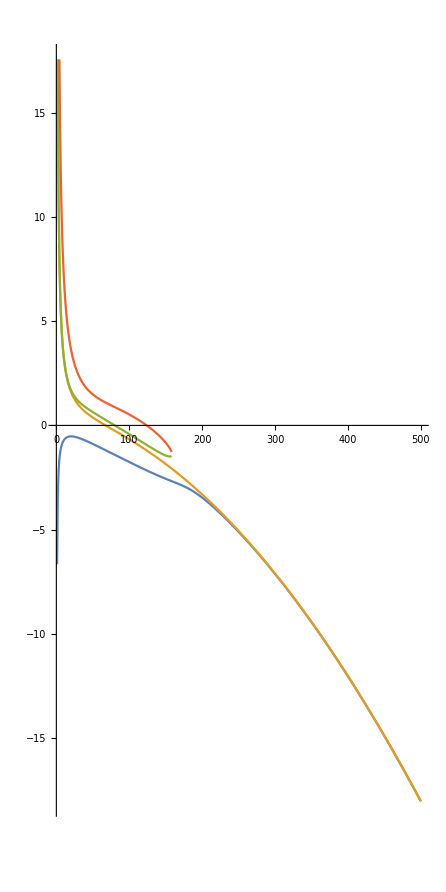

```mathematica
PlotL1=ListLinePlot[Transpose[EnergyTableL1],AspectRatio->2]
```

```mathematica
H[5,x]
```

{{-1/15+x κ^2,-ⅈ x κ,-ⅈ x κ,-x,(x κ^2)/10,-(x κ^2)/10,-(x κ^2)/10,(x κ^2)/10,-1/10 ⅈ x κ,-1/10 ⅈ x κ,(4 x κ^2)/75,(ⅈ x κ^2)/(25 √3),-(4 x κ^2)/75,(ⅈ x κ^2)/(25 √3),(x κ^2)/100,(ⅈ x κ^2)/(25 √3),-(4 x κ^2)/75,(ⅈ x κ^2)/(25 √3),(4 x κ^2)/75,-4/75 ⅈ x κ,-(2 ⅈ x κ)/(5 √165),-(2 ⅈ x κ)/(5 √165),(ⅈ x κ)/55,-4/75 ⅈ x κ,-(2 ⅈ x κ)/(5 √165),-(2 ⅈ x κ)/(5 √165),(ⅈ x κ)/55,x/55,x/55,x/55,x/55},{-ⅈ x κ,1/3,-x,0,-1/10 ⅈ x κ,(ⅈ x κ)/5,(ⅈ x κ)/5,-2/5 ⅈ x κ,0,-(2 x)/5,-4/75 ⅈ x κ,(2 x κ)/(25 √3),(2 ⅈ x κ)/25,(2 x κ)/(25 √3),-1/25 ⅈ x κ,1/25 √3 x κ,(2 ⅈ x κ)/25,1/25 √3 x κ,-3/25 ⅈ x κ,0,0,0,0,-(3 x)/25,-1/5 √(3/55) x,-1/5 √(3/55) x,x/55,0,0,0,0},{-ⅈ x κ,-x,1/3,0,-2/5 ⅈ x κ,(ⅈ x κ)/5,(ⅈ x κ)/5,-1/10 ⅈ x κ,-(2 x)/5,0,-3/25 ⅈ x κ,1/25 √3 x κ,(2 ⅈ x κ)/25,1/25 √3 x κ,-1/25 ⅈ x κ,(2 x κ)/(25 √3),(2 ⅈ x κ)/25,(2 x κ)/(25 √3),-4/75 ⅈ x κ,-(3 x)/25,-1/5 √(3/55) x,-1/5 √(3/55) x,x/55,0,0,0,0,0,0,0,0},{-x,0,0,11/15,-(2 x)/5,(2 x)/5,(2 x)/5,-(2 x)/5,0,0,-(3 x)/25,-2/25 ⅈ √3 x,(3 x)/25,-2/25 ⅈ √3 x,-(4 x)/25,-2/25 ⅈ √3 x,(3 x)/25,-2/25 ⅈ √3 x,-(3 x)/25,0,0,0,0,0,0,0,0,0,0,0,0},{(x κ^2)/10,-1/10 ⅈ x κ,-2/5 ⅈ x κ,-(2 x)/5,29/15+(4 x κ^2)/25,(x κ^2)/25,(x κ^2)/25,(x κ^2)/100,-4/25 ⅈ x κ,-1/25 ⅈ x κ,(49 x κ^2)/750,-(7 ⅈ x κ^2)/(125 √3),-(7 x κ^2)/375,-(7 ⅈ x κ^2)/(125 √3),(2 x κ^2)/125,-(2 ⅈ x κ^2)/(125 √3),-(7 x κ^2)/375,-(2 ⅈ x κ^2)/(125 √3),(2 x κ^2)/375,-49/750 ⅈ x κ,-(7 ⅈ x κ)/(50 √165),-(7 ⅈ x κ)/(50 √165),(ⅈ x κ)/550,-8/375 ⅈ x κ,-8/25 ⅈ √(3/55) x κ,-8/25 ⅈ √(3/55) x κ,(72 ⅈ x κ)/275,(72 x)/275,(12 x)/275,(12 x)/275,(2 x)/275},{-(x κ^2)/10,(ⅈ x κ)/5,(ⅈ x κ)/5,(2 x)/5,(x κ^2)/25,29/15+(4 x κ^2)/25,(x κ^2)/100,(x κ^2)/25,-2/25 ⅈ x κ,-2/25 ⅈ x κ,-(7 x κ^2)/375,(7 ⅈ x κ^2)/(125 √3),(49 x κ^2)/750,(2 ⅈ x κ^2)/(125 √3),-(2 x κ^2)/125,(7 ⅈ x κ^2)/(125 √3),(2 x κ^2)/375,(2 ⅈ x κ^2)/(125 √3),-(7 x κ^2)/375,(14 ⅈ x κ)/375,14/25 ⅈ √(3/55) x κ,(2 ⅈ x κ)/(25 √165),-6/275 ⅈ x κ,(14 ⅈ x κ)/375,(2 ⅈ x κ)/(25 √165),14/25 ⅈ √(3/55) x κ,-6/275 ⅈ x κ,-(12 x)/275,-(72 x)/275,-(2 x)/275,-(12 x)/275},{-(x κ^2)/10,(ⅈ x κ)/5,(ⅈ x κ)/5,(2 x)/5,(x κ^2)/25,(x κ^2)/100,29/15+(4 x κ^2)/25,(x κ^2)/25,-2/25 ⅈ x κ,-2/25 ⅈ x κ,-(7 x κ^2)/375,(2 ⅈ x κ^2)/(125 √3),(2 x κ^2)/375,(7 ⅈ x κ^2)/(125 √3),-(2 x κ^2)/125,(2 ⅈ x κ^2)/(125 √3),(49 x κ^2)/750,(7 ⅈ x κ^2)/(125 √3),-(7 x κ^2)/375,(14 ⅈ x κ)/375,(2 ⅈ x κ)/(25 √165),14/25 ⅈ √(3/55) x κ,-6/275 ⅈ x κ,(14 ⅈ x κ)/375,14/25 ⅈ √(3/55) x κ,(2 ⅈ x κ)/(25 √165),-6/275 ⅈ x κ,-(12 x)/275,-(2 x)/275,-(72 x)/275,-(12 x)/275},{(x κ^2)/10,-2/5 ⅈ x κ,-1/10 ⅈ x κ,-(2 x)/5,(x κ^2)/100,(x κ^2)/25,(x κ^2)/25,29/15+(4 x κ^2)/25,-1/25 ⅈ x κ,-4/25 ⅈ x κ,(2 x κ^2)/375,-(2 ⅈ x κ^2)/(125 √3),-(7 x κ^2)/375,-(2 ⅈ x κ^2)/(125 √3),(2 x κ^2)/125,-(7 ⅈ x κ^2)/(125 √3),-(7 x κ^2)/375,-(7 ⅈ x κ^2)/(125 √3),(49 x κ^2)/750,-8/375 ⅈ x κ,-8/25 ⅈ √(3/55) x κ,-8/25 ⅈ √(3/55) x κ,(72 ⅈ x κ)/275,-49/750 ⅈ x κ,-(7 ⅈ x κ)/(50 √165),-(7 ⅈ x κ)/(50 √165),(ⅈ x κ)/550,(2 x)/275,(12 x)/275,(12 x)/275,(72 x)/275},{-1/10 ⅈ x κ,0,-(2 x)/5,0,-4/25 ⅈ x κ,-2/25 ⅈ x κ,-2/25 ⅈ x κ,-1/25 ⅈ x κ,7/3,-(4 x)/25,-49/750 ⅈ x κ,-(14 x κ)/(125 √3),(7 ⅈ x κ)/250,-(14 x κ)/(125 √3),-8/125 ⅈ x κ,-2/125 √3 x κ,(7 ⅈ x κ)/250,-2/125 √3 x κ,-3/250 ⅈ x κ,0,0,0,0,-(6 x)/125,-12/25 √(3/55) x,-12/25 √(3/55) x,(72 x)/275,0,0,0,0},{-1/10 ⅈ x κ,-(2 x)/5,0,0,-1/25 ⅈ x κ,-2/25 ⅈ x κ,-2/25 ⅈ x κ,-4/25 ⅈ x κ,-(4 x)/25,7/3,-3/250 ⅈ x κ,-2/125 √3 x κ,(7 ⅈ x κ)/250,-2/125 √3 x κ,-8/125 ⅈ x κ,-(14 x κ)/(125 √3),(7 ⅈ x κ)/250,-(14 x κ)/(125 √3),-49/750 ⅈ x κ,-(6 x)/125,-12/25 √(3/55) x,-12/25 √(3/55) x,(72 x)/275,0,0,0,0,0,0,0,0},{(4 x κ^2)/75,-4/75 ⅈ x κ,-3/25 ⅈ x κ,-(3 x)/25,(49 x κ^2)/750,-(7 x κ^2)/375,-(7 x κ^2)/375,(2 x κ^2)/375,-49/750 ⅈ x κ,-3/250 ⅈ x κ,59/15+(289 x κ^2)/625,-(119 ⅈ x κ^2)/(1250 √3),(68 x κ^2)/1875,-(119 ⅈ x κ^2)/(1250 √3),(49 x κ^2)/7500,(14 ⅈ x κ^2)/(1875 √3),(68 x κ^2)/1875,(14 ⅈ x κ^2)/(1875 √3),(16 x κ^2)/5625,-289/625 ⅈ x κ,(34 ⅈ x κ)/(125 √165),(34 ⅈ x κ)/(125 √165),(4 ⅈ x κ)/4125,-4/625 ⅈ x κ,28/125 ⅈ √(3/55) x κ,28/125 ⅈ √(3/55) x κ,(588 ⅈ x κ)/1375,(588 x)/1375,-(42 x)/1375,-(42 x)/1375,(3 x)/1375},{(ⅈ x κ^2)/(25 √3),(2 x κ)/(25 √3),1/25 √3 x κ,-2/25 ⅈ √3 x,-(7 ⅈ x κ^2)/(125 √3),(7 ⅈ x κ^2)/(125 √3),(2 ⅈ x κ^2)/(125 √3),-(2 ⅈ x κ^2)/(125 √3),-(14 x κ)/(125 √3),-2/125 √3 x κ,-(119 ⅈ x κ^2)/(1250 √3),59/15+(68 x κ^2)/625,(119 ⅈ x κ^2)/(1250 √3),-(49 x κ^2)/7500,(14 ⅈ x κ^2)/(625 √3),-(49 x κ^2)/7500,-(14 ⅈ x κ^2)/(1875 √3),-(16 x κ^2)/1875,(14 ⅈ x κ^2)/(1875 √3),-(119 x κ)/(625 √3),-(102 x κ)/(125 √55),(14 x κ)/(375 √55),-(4 √3 x κ)/1375,(14 x κ)/(625 √3),(12 x κ)/(125 √55),-(98 x κ)/(125 √55),(84 √3 x κ)/1375,-(168 ⅈ √3 x)/1375,-(168 ⅈ √3 x)/1375,(12 ⅈ √3 x)/1375,(12 ⅈ √3 x)/1375},{-(4 x κ^2)/75,(2 ⅈ x κ)/25,(2 ⅈ x κ)/25,(3 x)/25,-(7 x κ^2)/375,(49 x κ^2)/750,(2 x κ^2)/375,-(7 x κ^2)/375,(7 ⅈ x κ)/250,(7 ⅈ x κ)/250,(68 x κ^2)/1875,(119 ⅈ x κ^2)/(1250 √3),59/15+(289 x κ^2)/625,-(14 ⅈ x κ^2)/(1875 √3),-(49 x κ^2)/7500,(119 ⅈ x κ^2)/(1250 √3),(16 x κ^2)/5625,-(14 ⅈ x κ^2)/(1875 √3),(68 x κ^2)/1875,-34/625 ⅈ x κ,238/125 ⅈ √(3/55) x κ,(4 ⅈ x κ)/(125 √165),(28 ⅈ x κ)/1375,-34/625 ⅈ x κ,(4 ⅈ x κ)/(125 √165),238/125 ⅈ √(3/55) x κ,(28 ⅈ x κ)/1375,(42 x)/1375,-(588 x)/1375,-(3 x)/1375,(42 x)/1375},{(ⅈ x κ^2)/(25 √3),(2 x κ)/(25 √3),1/25 √3 x κ,-2/25 ⅈ √3 x,-(7 ⅈ x κ^2)/(125 √3),(2 ⅈ x κ^2)/(125 √3),(7 ⅈ x κ^2)/(125 √3),-(2 ⅈ x κ^2)/(125 √3),-(14 x κ)/(125 √3),-2/125 √3 x κ,-(119 ⅈ x κ^2)/(1250 √3),-(49 x κ^2)/7500,-(14 ⅈ x κ^2)/(1875 √3),59/15+(68 x κ^2)/625,(14 ⅈ x κ^2)/(625 √3),-(16 x κ^2)/1875,(119 ⅈ x κ^2)/(1250 √3),-(49 x κ^2)/7500,(14 ⅈ x κ^2)/(1875 √3),-(119 x κ)/(625 √3),(14 x κ)/(375 √55),-(102 x κ)/(125 √55),-(4 √3 x κ)/1375,(14 x κ)/(625 √3),-(98 x κ)/(125 √55),(12 x κ)/(125 √55),(84 √3 x κ)/1375,-(168 ⅈ √3 x)/1375,(12 ⅈ √3 x)/1375,-(168 ⅈ √3 x)/1375,(12 ⅈ √3 x)/1375},{(x κ^2)/100,-1/25 ⅈ x κ,-1/25 ⅈ x κ,-(4 x)/25,(2 x κ^2)/125,-(2 x κ^2)/125,-(2 x κ^2)/125,(2 x κ^2)/125,-8/125 ⅈ x κ,-8/125 ⅈ x κ,(49 x κ^2)/7500,(14 ⅈ x κ^2)/(625 √3),-(49 x κ^2)/7500,(14 ⅈ x κ^2)/(625 √3),59/15+(16 x κ^2)/625,(14 ⅈ x κ^2)/(625 √3),-(49 x κ^2)/7500,(14 ⅈ x κ^2)/(625 √3),(49 x κ^2)/7500,-(49 ⅈ x κ)/1875,-14/125 ⅈ √(3/55) x κ,-14/125 ⅈ √(3/55) x κ,(36 ⅈ x κ)/1375,-(49 ⅈ x κ)/1875,-14/125 ⅈ √(3/55) x κ,-14/125 ⅈ √(3/55) x κ,(36 ⅈ x κ)/1375,(144 x)/1375,(144 x)/1375,(144 x)/1375,(144 x)/1375},{(ⅈ x κ^2)/(25 √3),1/25 √3 x κ,(2 x κ)/(25 √3),-2/25 ⅈ √3 x,-(2 ⅈ x κ^2)/(125 √3),(7 ⅈ x κ^2)/(125 √3),(2 ⅈ x κ^2)/(125 √3),-(7 ⅈ x κ^2)/(125 √3),-2/125 √3 x κ,-(14 x κ)/(125 √3),(14 ⅈ x κ^2)/(1875 √3),-(49 x κ^2)/7500,(119 ⅈ x κ^2)/(1250 √3),-(16 x κ^2)/1875,(14 ⅈ x κ^2)/(625 √3),59/15+(68 x κ^2)/625,-(14 ⅈ x κ^2)/(1875 √3),-(49 x κ^2)/7500,-(119 ⅈ x κ^2)/(1250 √3),(14 x κ)/(625 √3),-(98 x κ)/(125 √55),(12 x κ)/(125 √55),(84 √3 x κ)/1375,-(119 x κ)/(625 √3),(14 x κ)/(375 √55),-(102 x κ)/(125 √55),-(4 √3 x κ)/1375,(12 ⅈ √3 x)/1375,-(168 ⅈ √3 x)/1375,(12 ⅈ √3 x)/1375,-(168 ⅈ √3 x)/1375},{-(4 x κ^2)/75,(2 ⅈ x κ)/25,(2 ⅈ x κ)/25,(3 x)/25,-(7 x κ^2)/375,(2 x κ^2)/375,(49 x κ^2)/750,-(7 x κ^2)/375,(7 ⅈ x κ)/250,(7 ⅈ x κ)/250,(68 x κ^2)/1875,-(14 ⅈ x κ^2)/(1875 √3),(16 x κ^2)/5625,(119 ⅈ x κ^2)/(1250 √3),-(49 x κ^2)/7500,-(14 ⅈ x κ^2)/(1875 √3),59/15+(289 x κ^2)/625,(119 ⅈ x κ^2)/(1250 √3),(68 x κ^2)/1875,-34/625 ⅈ x κ,(4 ⅈ x κ)/(125 √165),238/125 ⅈ √(3/55) x κ,(28 ⅈ x κ)/1375,-34/625 ⅈ x κ,238/125 ⅈ √(3/55) x κ,(4 ⅈ x κ)/(125 √165),(28 ⅈ x κ)/1375,(42 x)/1375,-(3 x)/1375,-(588 x)/1375,(42 x)/1375},{(ⅈ x κ^2)/(25 √3),1/25 √3 x κ,(2 x κ)/(25 √3),-2/25 ⅈ √3 x,-(2 ⅈ x κ^2)/(125 √3),(2 ⅈ x κ^2)/(125 √3),(7 ⅈ x κ^2)/(125 √3),-(7 ⅈ x κ^2)/(125 √3),-2/125 √3 x κ,-(14 x κ)/(125 √3),(14 ⅈ x κ^2)/(1875 √3),-(16 x κ^2)/1875,-(14 ⅈ x κ^2)/(1875 √3),-(49 x κ^2)/7500,(14 ⅈ x κ^2)/(625 √3),-(49 x κ^2)/7500,(119 ⅈ x κ^2)/(1250 √3),59/15+(68 x κ^2)/625,-(119 ⅈ x κ^2)/(1250 √3),(14 x κ)/(625 √3),(12 x κ)/(125 √55),-(98 x κ)/(125 √55),(84 √3 x κ)/1375,-(119 x κ)/(625 √3),-(102 x κ)/(125 √55),(14 x κ)/(375 √55),-(4 √3 x κ)/1375,(12 ⅈ √3 x)/1375,(12 ⅈ √3 x)/1375,-(168 ⅈ √3 x)/1375,-(168 ⅈ √3 x)/1375},{(4 x κ^2)/75,-3/25 ⅈ x κ,-4/75 ⅈ x κ,-(3 x)/25,(2 x κ^2)/375,-(7 x κ^2)/375,-(7 x κ^2)/375,(49 x κ^2)/750,-3/250 ⅈ x κ,-49/750 ⅈ x κ,(16 x κ^2)/5625,(14 ⅈ x κ^2)/(1875 √3),(68 x κ^2)/1875,(14 ⅈ x κ^2)/(1875 √3),(49 x κ^2)/7500,-(119 ⅈ x κ^2)/(1250 √3),(68 x κ^2)/1875,-(119 ⅈ x κ^2)/(1250 √3),59/15+(289 x κ^2)/625,-4/625 ⅈ x κ,28/125 ⅈ √(3/55) x κ,28/125 ⅈ √(3/55) x κ,(588 ⅈ x κ)/1375,-289/625 ⅈ x κ,(34 ⅈ x κ)/(125 √165),(34 ⅈ x κ)/(125 √165),(4 ⅈ x κ)/4125,(3 x)/1375,-(42 x)/1375,-(42 x)/1375,(588 x)/1375},{-4/75 ⅈ x κ,0,-(3 x)/25,0,-49/750 ⅈ x κ,(14 ⅈ x κ)/375,(14 ⅈ x κ)/375,-8/375 ⅈ x κ,0,-(6 x)/125,-289/625 ⅈ x κ,-(119 x κ)/(625 √3),-34/625 ⅈ x κ,-(119 x κ)/(625 √3),-(49 ⅈ x κ)/1875,(14 x κ)/(625 √3),-34/625 ⅈ x κ,(14 x κ)/(625 √3),-4/625 ⅈ x κ,13/3,0,0,0,-(9 x)/625,42/125 √(3/55) x,42/125 √(3/55) x,(588 x)/1375,0,0,0,0},{-(2 ⅈ x κ)/(5 √165),0,-1/5 √(3/55) x,0,-(7 ⅈ x κ)/(50 √165),14/25 ⅈ √(3/55) x κ,(2 ⅈ x κ)/(25 √165),-8/25 ⅈ √(3/55) x κ,0,-12/25 √(3/55) x,(34 ⅈ x κ)/(125 √165),-(102 x κ)/(125 √55),238/125 ⅈ √(3/55) x κ,(14 x κ)/(375 √55),-14/125 ⅈ √(3/55) x κ,-(98 x κ)/(125 √55),(4 ⅈ x κ)/(125 √165),(12 x κ)/(125 √55),28/125 ⅈ √(3/55) x κ,0,13/3,0,0,42/125 √(3/55) x,-(3 x)/1375,-(588 x)/1375,-14/275 √(3/55) x,0,0,0,0},{-(2 ⅈ x κ)/(5 √165),0,-1/5 √(3/55) x,0,-(7 ⅈ x κ)/(50 √165),(2 ⅈ x κ)/(25 √165),14/25 ⅈ √(3/55) x κ,-8/25 ⅈ √(3/55) x κ,0,-12/25 √(3/55) x,(34 ⅈ x κ)/(125 √165),(14 x κ)/(375 √55),(4 ⅈ x κ)/(125 √165),-(102 x κ)/(125 √55),-14/125 ⅈ √(3/55) x κ,(12 x κ)/(125 √55),238/125 ⅈ √(3/55) x κ,-(98 x κ)/(125 √55),28/125 ⅈ √(3/55) x κ,0,0,13/3,0,42/125 √(3/55) x,-(588 x)/1375,-(3 x)/1375,-14/275 √(3/55) x,0,0,0,0},{(ⅈ x κ)/55,0,x/55,0,(ⅈ x κ)/550,-6/275 ⅈ x κ,-6/275 ⅈ x κ,(72 ⅈ x κ)/275,0,(72 x)/275,(4 ⅈ x κ)/4125,-(4 √3 x κ)/1375,(28 ⅈ x κ)/1375,-(4 √3 x κ)/1375,(36 ⅈ x κ)/1375,(84 √3 x κ)/1375,(28 ⅈ x κ)/1375,(84 √3 x κ)/1375,(588 ⅈ x κ)/1375,0,0,0,13/3,(588 x)/1375,-14/275 √(3/55) x,-14/275 √(3/55) x,-x/3025,0,0,0,0},{-4/75 ⅈ x κ,-(3 x)/25,0,0,-8/375 ⅈ x κ,(14 ⅈ x κ)/375,(14 ⅈ x κ)/375,-49/750 ⅈ x κ,-(6 x)/125,0,-4/625 ⅈ x κ,(14 x κ)/(625 √3),-34/625 ⅈ x κ,(14 x κ)/(625 √3),-(49 ⅈ x κ)/1875,-(119 x κ)/(625 √3),-34/625 ⅈ x κ,-(119 x κ)/(625 √3),-289/625 ⅈ x κ,-(9 x)/625,42/125 √(3/55) x,42/125 √(3/55) x,(588 x)/1375,13/3,0,0,0,0,0,0,0},{-(2 ⅈ x κ)/(5 √165),-1/5 √(3/55) x,0,0,-8/25 ⅈ √(3/55) x κ,(2 ⅈ x κ)/(25 √165),14/25 ⅈ √(3/55) x κ,-(7 ⅈ x κ)/(50 √165),-12/25 √(3/55) x,0,28/125 ⅈ √(3/55) x κ,(12 x κ)/(125 √55),(4 ⅈ x κ)/(125 √165),-(98 x κ)/(125 √55),-14/125 ⅈ √(3/55) x κ,(14 x κ)/(375 √55),238/125 ⅈ √(3/55) x κ,-(102 x κ)/(125 √55),(34 ⅈ x κ)/(125 √165),42/125 √(3/55) x,-(3 x)/1375,-(588 x)/1375,-14/275 √(3/55) x,0,13/3,0,0,0,0,0,0},{-(2 ⅈ x κ)/(5 √165),-1/5 √(3/55) x,0,0,-8/25 ⅈ √(3/55) x κ,14/25 ⅈ √(3/55) x κ,(2 ⅈ x κ)/(25 √165),-(7 ⅈ x κ)/(50 √165),-12/25 √(3/55) x,0,28/125 ⅈ √(3/55) x κ,-(98 x κ)/(125 √55),238/125 ⅈ √(3/55) x κ,(12 x κ)/(125 √55),-14/125 ⅈ √(3/55) x κ,-(102 x κ)/(125 √55),(4 ⅈ x κ)/(125 √165),(14 x κ)/(375 √55),(34 ⅈ x κ)/(125 √165),42/125 √(3/55) x,-(588 x)/1375,-(3 x)/1375,-14/275 √(3/55) x,0,0,13/3,0,0,0,0,0},{(ⅈ x κ)/55,x/55,0,0,(72 ⅈ x κ)/275,-6/275 ⅈ x κ,-6/275 ⅈ x κ,(ⅈ x κ)/550,(72 x)/275,0,(588 ⅈ x κ)/1375,(84 √3 x κ)/1375,(28 ⅈ x κ)/1375,(84 √3 x κ)/1375,(36 ⅈ x κ)/1375,-(4 √3 x κ)/1375,(28 ⅈ x κ)/1375,-(4 √3 x κ)/1375,(4 ⅈ x κ)/4125,(588 x)/1375,-14/275 √(3/55) x,-14/275 √(3/55) x,-x/3025,0,0,0,13/3,0,0,0,0},{x/55,0,0,0,(72 x)/275,-(12 x)/275,-(12 x)/275,(2 x)/275,0,0,(588 x)/1375,-(168 ⅈ √3 x)/1375,(42 x)/1375,-(168 ⅈ √3 x)/1375,(144 x)/1375,(12 ⅈ √3 x)/1375,(42 x)/1375,(12 ⅈ √3 x)/1375,(3 x)/1375,0,0,0,0,0,0,0,0,71/15,0,0,0},{x/55,0,0,0,(12 x)/275,-(72 x)/275,-(2 x)/275,(12 x)/275,0,0,-(42 x)/1375,-(168 ⅈ √3 x)/1375,-(588 x)/1375,(12 ⅈ √3 x)/1375,(144 x)/1375,-(168 ⅈ √3 x)/1375,-(3 x)/1375,(12 ⅈ √3 x)/1375,-(42 x)/1375,0,0,0,0,0,0,0,0,0,71/15,0,0},{x/55,0,0,0,(12 x)/275,-(2 x)/275,-(72 x)/275,(12 x)/275,0,0,-(42 x)/1375,(12 ⅈ √3 x)/1375,-(3 x)/1375,-(168 ⅈ √3 x)/1375,(144 x)/1375,(12 ⅈ √3 x)/1375,-(588 x)/1375,-(168 ⅈ √3 x)/1375,-(42 x)/1375,0,0,0,0,0,0,0,0,0,0,71/15,0},{x/55,0,0,0,(2 x)/275,-(12 x)/275,-(12 x)/275,(72 x)/275,0,0,(3 x)/1375,(12 ⅈ √3 x)/1375,(42 x)/1375,(12 ⅈ √3 x)/1375,(144 x)/1375,-(168 ⅈ √3 x)/1375,(42 x)/1375,-(168 ⅈ √3 x)/1375,(588 x)/1375,0,0,0,0,0,0,0,0,0,0,0,71/15}}

```mathematica
EnergyTableL5=Table[Sort[1/(i/100)Eigenvalues[H5[-(i/100)^(14/5)-0.]]][[1;;7]]//Chop,{i,1,300}];
```

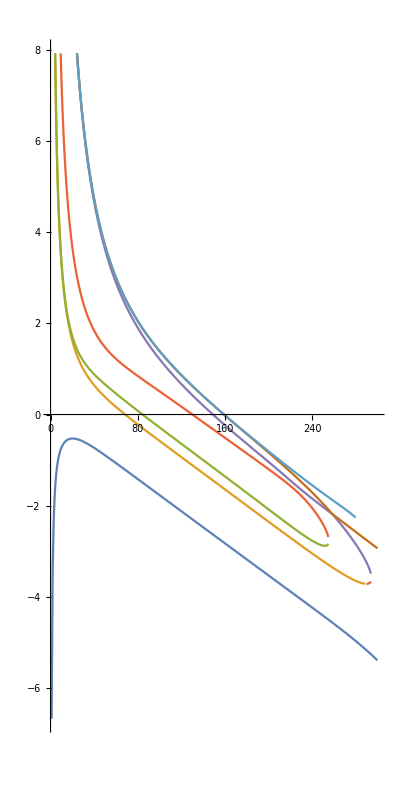

```mathematica
PlotL5=ListLinePlot[Transpose[EnergyTableL5],AspectRatio->2]
```

```mathematica
EnergyTableL5P=Table[(EnergyTableL5[[i]][[1;;7]]-EnergyTableL5[[i]][[1]])/(EnergyTableL5[[i]][[2]]-EnergyTableL5[[i]][[1]])//Chop,{i,1,270}];
```

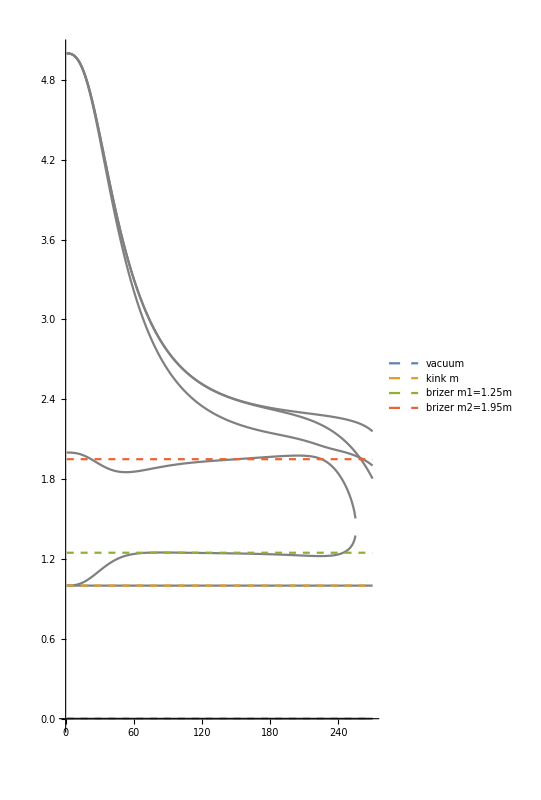

```mathematica
Show[ListLinePlot[Transpose[EnergyTableL5P],AspectRatio->2,PlotStyle->Gray],Plot[{0,1,1.247,1.95},{x,1,270},PlotStyle->Dashed,PlotLegends->{"vacuum","kink m","brizer m1=1.25m","brizer m2=1.95m"}]]
```

```mathematica
H[7,x]
```

{{-1/15+x κ^2,-ⅈ x κ,-ⅈ x κ,-x,(x κ^2)/10,-(x κ^2)/10,-(x κ^2)/10,(x κ^2)/10,-1/10 ⅈ x κ,-1/10 ⅈ x κ,(4 x κ^2)/75,(ⅈ x κ^2)/(25 √3),-(4 x κ^2)/75,(ⅈ x κ^2)/(25 √3),(x κ^2)/100,(ⅈ x κ^2)/(25 √3),-(4 x κ^2)/75,(ⅈ x κ^2)/(25 √3),(4 x κ^2)/75,-4/75 ⅈ x κ,-(2 ⅈ x κ)/(5 √165),-(2 ⅈ x κ)/(5 √165),(ⅈ x κ)/55,-4/75 ⅈ x κ,-(2 ⅈ x κ)/(5 √165),-(2 ⅈ x κ)/(5 √165),(ⅈ x κ)/55,x/55,x/55,x/55,x/55,(9 x κ^2)/250,1/125 ⅈ √3 x κ^2,1/125 ⅈ √3 x κ^2,-(9 x κ^2)/250,1/125 ⅈ √3 x κ^2,(2 x κ^2)/375,(2 x κ^2)/375,1/125 ⅈ √3 x κ^2,1/125 ⅈ √3 x κ^2,(2 x κ^2)/375,(2 x κ^2)/375,1/125 ⅈ √3 x κ^2,-(9 x κ^2)/250,1/125 ⅈ √3 x κ^2,1/125 ⅈ √3 x κ^2,(9 x κ^2)/250,-9/250 ⅈ x κ,-(3 x κ)/(50 √55),-(3 ⅈ x κ)/(25 √22),-(3 x κ)/(50 √55),-(3 ⅈ x κ)/(25 √22),(ⅈ x κ)/550,-(x κ)/(55 √10),-(x κ)/(55 √10),(ⅈ x κ)/55,-9/250 ⅈ x κ,-(3 ⅈ x κ)/(25 √22),-(3 x κ)/(50 √55),-(3 ⅈ x κ)/(25 √22),-(3 x κ)/(50 √55),(ⅈ x κ)/55,-(x κ)/(55 √10),-(x κ)/(55 √10),(ⅈ x κ)/550,x/55,x/55,x/55,x/55},{-ⅈ x κ,1/3,-x,0,-1/10 ⅈ x κ,(ⅈ x κ)/5,(ⅈ x κ)/5,-2/5 ⅈ x κ,0,-(2 x)/5,-4/75 ⅈ x κ,(2 x κ)/(25 √3),(2 ⅈ x κ)/25,(2 x κ)/(25 √3),-1/25 ⅈ x κ,1/25 √3 x κ,(2 ⅈ x κ)/25,1/25 √3 x κ,-3/25 ⅈ x κ,0,0,0,0,-(3 x)/25,-1/5 √(3/55) x,-1/5 √(3/55) x,x/55,0,0,0,0,-9/250 ⅈ x κ,2/125 √3 x κ,3/250 √3 x κ,(6 ⅈ x κ)/125,2/125 √3 x κ,-8/375 ⅈ x κ,-2/125 ⅈ x κ,(8 x κ)/(125 √3),3/250 √3 x κ,-2/125 ⅈ x κ,-3/250 ⅈ x κ,2/125 √3 x κ,(6 ⅈ x κ)/125,(8 x κ)/(125 √3),2/125 √3 x κ,-8/125 ⅈ x κ,0,0,0,0,0,0,0,0,0,-(8 x)/125,-2/25 √(2/11) x,(4 ⅈ x)/(25 √55),-2/25 √(2/11) x,(4 ⅈ x)/(25 √55),x/55,1/55 ⅈ √(2/5) x,1/55 ⅈ √(2/5) x,(2 x)/275,0,0,0,0},{-ⅈ x κ,-x,1/3,0,-2/5 ⅈ x κ,(ⅈ x κ)/5,(ⅈ x κ)/5,-1/10 ⅈ x κ,-(2 x)/5,0,-3/25 ⅈ x κ,1/25 √3 x κ,(2 ⅈ x κ)/25,1/25 √3 x κ,-1/25 ⅈ x κ,(2 x κ)/(25 √3),(2 ⅈ x κ)/25,(2 x κ)/(25 √3),-4/75 ⅈ x κ,-(3 x)/25,-1/5 √(3/55) x,-1/5 √(3/55) x,x/55,0,0,0,0,0,0,0,0,-8/125 ⅈ x κ,2/125 √3 x κ,(8 x κ)/(125 √3),(6 ⅈ x κ)/125,2/125 √3 x κ,-3/250 ⅈ x κ,-2/125 ⅈ x κ,3/250 √3 x κ,(8 x κ)/(125 √3),-2/125 ⅈ x κ,-8/375 ⅈ x κ,2/125 √3 x κ,(6 ⅈ x κ)/125,3/250 √3 x κ,2/125 √3 x κ,-9/250 ⅈ x κ,-(8 x)/125,(4 ⅈ x)/(25 √55),-2/25 √(2/11) x,(4 ⅈ x)/(25 √55),-2/25 √(2/11) x,(2 x)/275,1/55 ⅈ √(2/5) x,1/55 ⅈ √(2/5) x,x/55,0,0,0,0,0,0,0,0,0,0,0,0,0},{-x,0,0,11/15,-(2 x)/5,(2 x)/5,(2 x)/5,-(2 x)/5,0,0,-(3 x)/25,-2/25 ⅈ √3 x,(3 x)/25,-2/25 ⅈ √3 x,-(4 x)/25,-2/25 ⅈ √3 x,(3 x)/25,-2/25 ⅈ √3 x,-(3 x)/25,0,0,0,0,0,0,0,0,0,0,0,0,-(8 x)/125,-4/125 ⅈ √3 x,-4/125 ⅈ √3 x,(8 x)/125,-4/125 ⅈ √3 x,-(6 x)/125,-(6 x)/125,-4/125 ⅈ √3 x,-4/125 ⅈ √3 x,-(6 x)/125,-(6 x)/125,-4/125 ⅈ √3 x,(8 x)/125,-4/125 ⅈ √3 x,-4/125 ⅈ √3 x,-(8 x)/125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{(x κ^2)/10,-1/10 ⅈ x κ,-2/5 ⅈ x κ,-(2 x)/5,29/15+(4 x κ^2)/25,(x κ^2)/25,(x κ^2)/25,(x κ^2)/100,-4/25 ⅈ x κ,-1/25 ⅈ x κ,(49 x κ^2)/750,-(7 ⅈ x κ^2)/(125 √3),-(7 x κ^2)/375,-(7 ⅈ x κ^2)/(125 √3),(2 x κ^2)/125,-(2 ⅈ x κ^2)/(125 √3),-(7 x κ^2)/375,-(2 ⅈ x κ^2)/(125 √3),(2 x κ^2)/375,-49/750 ⅈ x κ,-(7 ⅈ x κ)/(50 √165),-(7 ⅈ x κ)/(50 √165),(ⅈ x κ)/550,-8/375 ⅈ x κ,-8/25 ⅈ √(3/55) x κ,-8/25 ⅈ √(3/55) x κ,(72 ⅈ x κ)/275,(72 x)/275,(12 x)/275,(12 x)/275,(2 x)/275,(16 x κ^2)/625,(14 ⅈ x κ^2)/(625 √3),-(16 ⅈ x κ^2)/(625 √3),-(6 x κ^2)/625,(14 ⅈ x κ^2)/(625 √3),(49 x κ^2)/7500,-(14 x κ^2)/1875,(7 ⅈ √3 x κ^2)/2500,-(16 ⅈ x κ^2)/(625 √3),-(14 x κ^2)/1875,(16 x κ^2)/1875,-2/625 ⅈ √3 x κ^2,-(6 x κ^2)/625,(7 ⅈ √3 x κ^2)/2500,-2/625 ⅈ √3 x κ^2,(9 x κ^2)/2500,-16/625 ⅈ x κ,(8 x κ)/(125 √55),-2/125 ⅈ √(2/11) x κ,(8 x κ)/(125 √55),-2/125 ⅈ √(2/11) x κ,(4 ⅈ x κ)/1375,1/275 √(2/5) x κ,1/275 √(2/5) x κ,(ⅈ x κ)/550,-9/625 ⅈ x κ,-(21 ⅈ x κ)/(125 √22),-(18 x κ)/(125 √55),-(21 ⅈ x κ)/(125 √22),-(18 x κ)/(125 √55),(49 ⅈ x κ)/550,-21/275 √(2/5) x κ,-21/275 √(2/5) x κ,(36 ⅈ x κ)/1375,(49 x)/550,(7 x)/275,(7 x)/275,(2 x)/275},{-(x κ^2)/10,(ⅈ x κ)/5,(ⅈ x κ)/5,(2 x)/5,(x κ^2)/25,29/15+(4 x κ^2)/25,(x κ^2)/100,(x κ^2)/25,-2/25 ⅈ x κ,-2/25 ⅈ x κ,-(7 x κ^2)/375,(7 ⅈ x κ^2)/(125 √3),(49 x κ^2)/750,(2 ⅈ x κ^2)/(125 √3),-(2 x κ^2)/125,(7 ⅈ x κ^2)/(125 √3),(2 x κ^2)/375,(2 ⅈ x κ^2)/(125 √3),-(7 x κ^2)/375,(14 ⅈ x κ)/375,14/25 ⅈ √(3/55) x κ,(2 ⅈ x κ)/(25 √165),-6/275 ⅈ x κ,(14 ⅈ x κ)/375,(2 ⅈ x κ)/(25 √165),14/25 ⅈ √(3/55) x κ,-6/275 ⅈ x κ,-(12 x)/275,-(72 x)/275,-(2 x)/275,-(12 x)/275,-(6 x κ^2)/625,(16 ⅈ x κ^2)/(625 √3),-(14 ⅈ x κ^2)/(625 √3),(16 x κ^2)/625,-(7 ⅈ √3 x κ^2)/2500,(14 x κ^2)/1875,-(49 x κ^2)/7500,-(14 ⅈ x κ^2)/(625 √3),2/625 ⅈ √3 x κ^2,-(16 x κ^2)/1875,(14 x κ^2)/1875,(16 ⅈ x κ^2)/(625 √3),(9 x κ^2)/2500,2/625 ⅈ √3 x κ^2,-(7 ⅈ √3 x κ^2)/2500,-(6 x κ^2)/625,(12 ⅈ x κ)/625,(24 x κ)/(125 √55),14/125 ⅈ √(2/11) x κ,-(6 x κ)/(125 √55),(3 ⅈ x κ)/(125 √22),(12 ⅈ x κ)/1375,-7/275 √(2/5) x κ,3/275 √(2/5) x κ,-7/550 ⅈ x κ,(12 ⅈ x κ)/625,(3 ⅈ x κ)/(125 √22),-(6 x κ)/(125 √55),14/125 ⅈ √(2/11) x κ,(24 x κ)/(125 √55),-7/550 ⅈ x κ,-7/275 √(2/5) x κ,3/275 √(2/5) x κ,(12 ⅈ x κ)/1375,-(7 x)/275,-(49 x)/550,-(2 x)/275,-(7 x)/275},{-(x κ^2)/10,(ⅈ x κ)/5,(ⅈ x κ)/5,(2 x)/5,(x κ^2)/25,(x κ^2)/100,29/15+(4 x κ^2)/25,(x κ^2)/25,-2/25 ⅈ x κ,-2/25 ⅈ x κ,-(7 x κ^2)/375,(2 ⅈ x κ^2)/(125 √3),(2 x κ^2)/375,(7 ⅈ x κ^2)/(125 √3),-(2 x κ^2)/125,(2 ⅈ x κ^2)/(125 √3),(49 x κ^2)/750,(7 ⅈ x κ^2)/(125 √3),-(7 x κ^2)/375,(14 ⅈ x κ)/375,(2 ⅈ x κ)/(25 √165),14/25 ⅈ √(3/55) x κ,-6/275 ⅈ x κ,(14 ⅈ x κ)/375,14/25 ⅈ √(3/55) x κ,(2 ⅈ x κ)/(25 √165),-6/275 ⅈ x κ,-(12 x)/275,-(2 x)/275,-(72 x)/275,-(12 x)/275,-(6 x κ^2)/625,-(7 ⅈ √3 x κ^2)/2500,2/625 ⅈ √3 x κ^2,(9 x κ^2)/2500,(16 ⅈ x κ^2)/(625 √3),(14 x κ^2)/1875,-(16 x κ^2)/1875,2/625 ⅈ √3 x κ^2,-(14 ⅈ x κ^2)/(625 √3),-(49 x κ^2)/7500,(14 x κ^2)/1875,-(7 ⅈ √3 x κ^2)/2500,(16 x κ^2)/625,-(14 ⅈ x κ^2)/(625 √3),(16 ⅈ x κ^2)/(625 √3),-(6 x κ^2)/625,(12 ⅈ x κ)/625,-(6 x κ)/(125 √55),(3 ⅈ x κ)/(125 √22),(24 x κ)/(125 √55),14/125 ⅈ √(2/11) x κ,(12 ⅈ x κ)/1375,3/275 √(2/5) x κ,-7/275 √(2/5) x κ,-7/550 ⅈ x κ,(12 ⅈ x κ)/625,14/125 ⅈ √(2/11) x κ,(24 x κ)/(125 √55),(3 ⅈ x κ)/(125 √22),-(6 x κ)/(125 √55),-7/550 ⅈ x κ,3/275 √(2/5) x κ,-7/275 √(2/5) x κ,(12 ⅈ x κ)/1375,-(7 x)/275,-(2 x)/275,-(49 x)/550,-(7 x)/275},{(x κ^2)/10,-2/5 ⅈ x κ,-1/10 ⅈ x κ,-(2 x)/5,(x κ^2)/100,(x κ^2)/25,(x κ^2)/25,29/15+(4 x κ^2)/25,-1/25 ⅈ x κ,-4/25 ⅈ x κ,(2 x κ^2)/375,-(2 ⅈ x κ^2)/(125 √3),-(7 x κ^2)/375,-(2 ⅈ x κ^2)/(125 √3),(2 x κ^2)/125,-(7 ⅈ x κ^2)/(125 √3),-(7 x κ^2)/375,-(7 ⅈ x κ^2)/(125 √3),(49 x κ^2)/750,-8/375 ⅈ x κ,-8/25 ⅈ √(3/55) x κ,-8/25 ⅈ √(3/55) x κ,(72 ⅈ x κ)/275,-49/750 ⅈ x κ,-(7 ⅈ x κ)/(50 √165),-(7 ⅈ x κ)/(50 √165),(ⅈ x κ)/550,(2 x)/275,(12 x)/275,(12 x)/275,(72 x)/275,(9 x κ^2)/2500,-2/625 ⅈ √3 x κ^2,(7 ⅈ √3 x κ^2)/2500,-(6 x κ^2)/625,-2/625 ⅈ √3 x κ^2,(16 x κ^2)/1875,-(14 x κ^2)/1875,-(16 ⅈ x κ^2)/(625 √3),(7 ⅈ √3 x κ^2)/2500,-(14 x κ^2)/1875,(49 x κ^2)/7500,(14 ⅈ x κ^2)/(625 √3),-(6 x κ^2)/625,-(16 ⅈ x κ^2)/(625 √3),(14 ⅈ x κ^2)/(625 √3),(16 x κ^2)/625,-9/625 ⅈ x κ,-(18 x κ)/(125 √55),-(21 ⅈ x κ)/(125 √22),-(18 x κ)/(125 √55),-(21 ⅈ x κ)/(125 √22),(36 ⅈ x κ)/1375,-21/275 √(2/5) x κ,-21/275 √(2/5) x κ,(49 ⅈ x κ)/550,-16/625 ⅈ x κ,-2/125 ⅈ √(2/11) x κ,(8 x κ)/(125 √55),-2/125 ⅈ √(2/11) x κ,(8 x κ)/(125 √55),(ⅈ x κ)/550,1/275 √(2/5) x κ,1/275 √(2/5) x κ,(4 ⅈ x κ)/1375,(2 x)/275,(7 x)/275,(7 x)/275,(49 x)/550},{-1/10 ⅈ x κ,0,-(2 x)/5,0,-4/25 ⅈ x κ,-2/25 ⅈ x κ,-2/25 ⅈ x κ,-1/25 ⅈ x κ,7/3,-(4 x)/25,-49/750 ⅈ x κ,-(14 x κ)/(125 √3),(7 ⅈ x κ)/250,-(14 x κ)/(125 √3),-8/125 ⅈ x κ,-2/125 √3 x κ,(7 ⅈ x κ)/250,-2/125 √3 x κ,-3/250 ⅈ x κ,0,0,0,0,-(6 x)/125,-12/25 √(3/55) x,-12/25 √(3/55) x,(72 x)/275,0,0,0,0,-16/625 ⅈ x κ,(28 x κ)/(625 √3),-8/625 √3 x κ,(8 ⅈ x κ)/625,(28 x κ)/(625 √3),-(49 ⅈ x κ)/1875,(14 ⅈ x κ)/625,(14 x κ)/(625 √3),-8/625 √3 x κ,(14 ⅈ x κ)/625,-12/625 ⅈ x κ,-4/625 √3 x κ,(8 ⅈ x κ)/625,(14 x κ)/(625 √3),-4/625 √3 x κ,-4/625 ⅈ x κ,0,0,0,0,0,0,0,0,0,-(16 x)/625,-14/125 √(2/11) x,(48 ⅈ x)/(125 √55),-14/125 √(2/11) x,(48 ⅈ x)/(125 √55),(49 x)/550,42/275 ⅈ √(2/5) x,42/275 ⅈ √(2/5) x,(144 x)/1375,0,0,0,0},{-1/10 ⅈ x κ,-(2 x)/5,0,0,-1/25 ⅈ x κ,-2/25 ⅈ x κ,-2/25 ⅈ x κ,-4/25 ⅈ x κ,-(4 x)/25,7/3,-3/250 ⅈ x κ,-2/125 √3 x κ,(7 ⅈ x κ)/250,-2/125 √3 x κ,-8/125 ⅈ x κ,-(14 x κ)/(125 √3),(7 ⅈ x κ)/250,-(14 x κ)/(125 √3),-49/750 ⅈ x κ,-(6 x)/125,-12/25 √(3/55) x,-12/25 √(3/55) x,(72 x)/275,0,0,0,0,0,0,0,0,-4/625 ⅈ x κ,-4/625 √3 x κ,(14 x κ)/(625 √3),(8 ⅈ x κ)/625,-4/625 √3 x κ,-12/625 ⅈ x κ,(14 ⅈ x κ)/625,-8/625 √3 x κ,(14 x κ)/(625 √3),(14 ⅈ x κ)/625,-(49 ⅈ x κ)/1875,(28 x κ)/(625 √3),(8 ⅈ x κ)/625,-8/625 √3 x κ,(28 x κ)/(625 √3),-16/625 ⅈ x κ,-(16 x)/625,(48 ⅈ x)/(125 √55),-14/125 √(2/11) x,(48 ⅈ x)/(125 √55),-14/125 √(2/11) x,(144 x)/1375,42/275 ⅈ √(2/5) x,42/275 ⅈ √(2/5) x,(49 x)/550,0,0,0,0,0,0,0,0,0,0,0,0,0},{(4 x κ^2)/75,-4/75 ⅈ x κ,-3/25 ⅈ x κ,-(3 x)/25,(49 x κ^2)/750,-(7 x κ^2)/375,-(7 x κ^2)/375,(2 x κ^2)/375,-49/750 ⅈ x κ,-3/250 ⅈ x κ,59/15+(289 x κ^2)/625,-(119 ⅈ x κ^2)/(1250 √3),(68 x κ^2)/1875,-(119 ⅈ x κ^2)/(1250 √3),(49 x κ^2)/7500,(14 ⅈ x κ^2)/(1875 √3),(68 x κ^2)/1875,(14 ⅈ x κ^2)/(1875 √3),(16 x κ^2)/5625,-289/625 ⅈ x κ,(34 ⅈ x κ)/(125 √165),(34 ⅈ x κ)/(125 √165),(4 ⅈ x κ)/4125,-4/625 ⅈ x κ,28/125 ⅈ √(3/55) x κ,28/125 ⅈ √(3/55) x κ,(588 ⅈ x κ)/1375,(588 x)/1375,-(42 x)/1375,-(42 x)/1375,(3 x)/1375,(338 x κ^2)/9375,-(221 ⅈ x κ^2)/(3125 √3),(182 ⅈ x κ^2)/(9375 √3),-(26 x κ^2)/3125,-(221 ⅈ x κ^2)/(3125 √3),(289 x κ^2)/6250,-(119 x κ^2)/9375,-(17 ⅈ √3 x κ^2)/3125,(182 ⅈ x κ^2)/(9375 √3),-(119 x κ^2)/9375,(98 x κ^2)/28125,(14 ⅈ x κ^2)/(3125 √3),-(26 x κ^2)/3125,-(17 ⅈ √3 x κ^2)/3125,(14 ⅈ x κ^2)/(3125 √3),(6 x κ^2)/3125,-(338 ⅈ x κ)/9375,-(91 x κ)/(1875 √55),-(26 ⅈ √(2/11) x κ)/1875,-(91 x κ)/(1875 √55),-(26 ⅈ √(2/11) x κ)/1875,(49 ⅈ x κ)/41250,-(7 √(2/5) x κ)/4125,-(7 √(2/5) x κ)/4125,(4 ⅈ x κ)/4125,-(27 ⅈ x κ)/6250,-27/625 ⅈ √(2/11) x κ,(63 x κ)/(625 √55),-27/625 ⅈ √(2/11) x κ,(63 x κ)/(625 √55),(108 ⅈ x κ)/1375,(126 √(2/5) x κ)/1375,(126 √(2/5) x κ)/1375,(294 ⅈ x κ)/6875,(108 x)/1375,(18 x)/1375,(18 x)/1375,(3 x)/1375},{(ⅈ x κ^2)/(25 √3),(2 x κ)/(25 √3),1/25 √3 x κ,-2/25 ⅈ √3 x,-(7 ⅈ x κ^2)/(125 √3),(7 ⅈ x κ^2)/(125 √3),(2 ⅈ x κ^2)/(125 √3),-(2 ⅈ x κ^2)/(125 √3),-(14 x κ)/(125 √3),-2/125 √3 x κ,-(119 ⅈ x κ^2)/(1250 √3),59/15+(68 x κ^2)/625,(119 ⅈ x κ^2)/(1250 √3),-(49 x κ^2)/7500,(14 ⅈ x κ^2)/(625 √3),-(49 x κ^2)/7500,-(14 ⅈ x κ^2)/(1875 √3),-(16 x κ^2)/1875,(14 ⅈ x κ^2)/(1875 √3),-(119 x κ)/(625 √3),-(102 x κ)/(125 √55),(14 x κ)/(375 √55),-(4 √3 x κ)/1375,(14 x κ)/(625 √3),(12 x κ)/(125 √55),-(98 x κ)/(125 √55),(84 √3 x κ)/1375,-(168 ⅈ √3 x)/1375,-(168 ⅈ √3 x)/1375,(12 ⅈ √3 x)/1375,(12 ⅈ √3 x)/1375,(52 ⅈ x κ^2)/(3125 √3),(182 x κ^2)/9375,(182 x κ^2)/9375,-(52 ⅈ x κ^2)/(3125 √3),(34 x κ^2)/3125,(119 ⅈ x κ^2)/(3125 √3),(119 ⅈ x κ^2)/(3125 √3),(34 x κ^2)/3125,-(28 x κ^2)/9375,-(98 ⅈ x κ^2)/(9375 √3),-(98 ⅈ x κ^2)/(9375 √3),-(28 x κ^2)/9375,-(4 ⅈ √3 x κ^2)/3125,(14 x κ^2)/3125,(14 x κ^2)/3125,(4 ⅈ √3 x κ^2)/3125,(104 x κ)/(3125 √3),104/625 ⅈ √(3/55) x κ,(91 x κ)/(625 √66),-(28 ⅈ x κ)/(625 √165),8/625 √(2/33) x κ,(28 √3 x κ)/6875,-(49 ⅈ x κ)/(2750 √30),(8 ⅈ √(6/5) x κ)/1375,-(7 x κ)/(1375 √3),(12 √3 x κ)/3125,(21 √(3/22) x κ)/1250,36/625 ⅈ √(3/55) x κ,24/625 √(6/11) x κ,56/625 ⅈ √(3/55) x κ,-(21 √3 x κ)/1375,(72 ⅈ √(6/5) x κ)/1375,(49 ⅈ √(3/10) x κ)/1375,-(168 √3 x κ)/6875,(42 ⅈ √3 x)/1375,(42 ⅈ √3 x)/1375,(7 ⅈ √3 x)/1375,(7 ⅈ √3 x)/1375},{-(4 x κ^2)/75,(2 ⅈ x κ)/25,(2 ⅈ x κ)/25,(3 x)/25,-(7 x κ^2)/375,(49 x κ^2)/750,(2 x κ^2)/375,-(7 x κ^2)/375,(7 ⅈ x κ)/250,(7 ⅈ x κ)/250,(68 x κ^2)/1875,(119 ⅈ x κ^2)/(1250 √3),59/15+(289 x κ^2)/625,-(14 ⅈ x κ^2)/(1875 √3),-(49 x κ^2)/7500,(119 ⅈ x κ^2)/(1250 √3),(16 x κ^2)/5625,-(14 ⅈ x κ^2)/(1875 √3),(68 x κ^2)/1875,-34/625 ⅈ x κ,238/125 ⅈ √(3/55) x κ,(4 ⅈ x κ)/(125 √165),(28 ⅈ x κ)/1375,-34/625 ⅈ x κ,(4 ⅈ x κ)/(125 √165),238/125 ⅈ √(3/55) x κ,(28 ⅈ x κ)/1375,(42 x)/1375,-(588 x)/1375,-(3 x)/1375,(42 x)/1375,-(26 x κ^2)/3125,-(182 ⅈ x κ^2)/(9375 √3),(221 ⅈ x κ^2)/(3125 √3),(338 x κ^2)/9375,(17 ⅈ √3 x κ^2)/3125,(119 x κ^2)/9375,-(289 x κ^2)/6250,(221 ⅈ x κ^2)/(3125 √3),-(14 ⅈ x κ^2)/(3125 √3),-(98 x κ^2)/28125,(119 x κ^2)/9375,-(182 ⅈ x κ^2)/(9375 √3),(6 x κ^2)/3125,-(14 ⅈ x κ^2)/(3125 √3),(17 ⅈ √3 x κ^2)/3125,-(26 x κ^2)/3125,(39 ⅈ x κ)/3125,-(182 x κ)/(625 √55),78/625 ⅈ √(2/11) x κ,(21 x κ)/(1250 √55),3/625 ⅈ √(2/11) x κ,(49 ⅈ x κ)/6875,(21 √(2/5) x κ)/1375,-(14 √(2/5) x κ)/1375,-(12 ⅈ x κ)/1375,(39 ⅈ x κ)/3125,3/625 ⅈ √(2/11) x κ,(21 x κ)/(1250 √55),78/625 ⅈ √(2/11) x κ,-(182 x κ)/(625 √55),-(12 ⅈ x κ)/1375,(21 √(2/5) x κ)/1375,-(14 √(2/5) x κ)/1375,(49 ⅈ x κ)/6875,-(18 x)/1375,-(108 x)/1375,-(3 x)/1375,-(18 x)/1375},{(ⅈ x κ^2)/(25 √3),(2 x κ)/(25 √3),1/25 √3 x κ,-2/25 ⅈ √3 x,-(7 ⅈ x κ^2)/(125 √3),(2 ⅈ x κ^2)/(125 √3),(7 ⅈ x κ^2)/(125 √3),-(2 ⅈ x κ^2)/(125 √3),-(14 x κ)/(125 √3),-2/125 √3 x κ,-(119 ⅈ x κ^2)/(1250 √3),-(49 x κ^2)/7500,-(14 ⅈ x κ^2)/(1875 √3),59/15+(68 x κ^2)/625,(14 ⅈ x κ^2)/(625 √3),-(16 x κ^2)/1875,(119 ⅈ x κ^2)/(1250 √3),-(49 x κ^2)/7500,(14 ⅈ x κ^2)/(1875 √3),-(119 x κ)/(625 √3),(14 x κ)/(375 √55),-(102 x κ)/(125 √55),-(4 √3 x κ)/1375,(14 x κ)/(625 √3),-(98 x κ)/(125 √55),(12 x κ)/(125 √55),(84 √3 x κ)/1375,-(168 ⅈ √3 x)/1375,(12 ⅈ √3 x)/1375,-(168 ⅈ √3 x)/1375,(12 ⅈ √3 x)/1375,(52 ⅈ x κ^2)/(3125 √3),(34 x κ^2)/3125,-(28 x κ^2)/9375,-(4 ⅈ √3 x κ^2)/3125,(182 x κ^2)/9375,(119 ⅈ x κ^2)/(3125 √3),-(98 ⅈ x κ^2)/(9375 √3),(14 x κ^2)/3125,(182 x κ^2)/9375,(119 ⅈ x κ^2)/(3125 √3),-(98 ⅈ x κ^2)/(9375 √3),(14 x κ^2)/3125,-(52 ⅈ x κ^2)/(3125 √3),(34 x κ^2)/3125,-(28 x κ^2)/9375,(4 ⅈ √3 x κ^2)/3125,(104 x κ)/(3125 √3),-(28 ⅈ x κ)/(625 √165),8/625 √(2/33) x κ,104/625 ⅈ √(3/55) x κ,(91 x κ)/(625 √66),(28 √3 x κ)/6875,(8 ⅈ √(6/5) x κ)/1375,-(49 ⅈ x κ)/(2750 √30),-(7 x κ)/(1375 √3),(12 √3 x κ)/3125,24/625 √(6/11) x κ,56/625 ⅈ √(3/55) x κ,(21 √(3/22) x κ)/1250,36/625 ⅈ √(3/55) x κ,-(21 √3 x κ)/1375,(49 ⅈ √(3/10) x κ)/1375,(72 ⅈ √(6/5) x κ)/1375,-(168 √3 x κ)/6875,(42 ⅈ √3 x)/1375,(7 ⅈ √3 x)/1375,(42 ⅈ √3 x)/1375,(7 ⅈ √3 x)/1375},{(x κ^2)/100,-1/25 ⅈ x κ,-1/25 ⅈ x κ,-(4 x)/25,(2 x κ^2)/125,-(2 x κ^2)/125,-(2 x κ^2)/125,(2 x κ^2)/125,-8/125 ⅈ x κ,-8/125 ⅈ x κ,(49 x κ^2)/7500,(14 ⅈ x κ^2)/(625 √3),-(49 x κ^2)/7500,(14 ⅈ x κ^2)/(625 √3),59/15+(16 x κ^2)/625,(14 ⅈ x κ^2)/(625 √3),-(49 x κ^2)/7500,(14 ⅈ x κ^2)/(625 √3),(49 x κ^2)/7500,-(49 ⅈ x κ)/1875,-14/125 ⅈ √(3/55) x κ,-14/125 ⅈ √(3/55) x κ,(36 ⅈ x κ)/1375,-(49 ⅈ x κ)/1875,-14/125 ⅈ √(3/55) x κ,-14/125 ⅈ √(3/55) x κ,(36 ⅈ x κ)/1375,(144 x)/1375,(144 x)/1375,(144 x)/1375,(144 x)/1375,(8 x κ^2)/3125,-(28 ⅈ x κ^2)/(3125 √3),-(28 ⅈ x κ^2)/(3125 √3),-(8 x κ^2)/3125,-(28 ⅈ x κ^2)/(3125 √3),(98 x κ^2)/9375,(98 x κ^2)/9375,-(28 ⅈ x κ^2)/(3125 √3),-(28 ⅈ x κ^2)/(3125 √3),(98 x κ^2)/9375,(98 x κ^2)/9375,-(28 ⅈ x κ^2)/(3125 √3),-(8 x κ^2)/3125,-(28 ⅈ x κ^2)/(3125 √3),-(28 ⅈ x κ^2)/(3125 √3),(8 x κ^2)/3125,-(32 ⅈ x κ)/3125,(96 x κ)/(625 √55),-14/625 ⅈ √(2/11) x κ,(96 x κ)/(625 √55),-14/625 ⅈ √(2/11) x κ,(288 ⅈ x κ)/6875,(42 √(2/5) x κ)/1375,(42 √(2/5) x κ)/1375,(49 ⅈ x κ)/5500,-(32 ⅈ x κ)/3125,-14/625 ⅈ √(2/11) x κ,(96 x κ)/(625 √55),-14/625 ⅈ √(2/11) x κ,(96 x κ)/(625 √55),(49 ⅈ x κ)/5500,(42 √(2/5) x κ)/1375,(42 √(2/5) x κ)/1375,(288 ⅈ x κ)/6875,(49 x)/1375,(49 x)/1375,(49 x)/1375,(49 x)/1375},{(ⅈ x κ^2)/(25 √3),1/25 √3 x κ,(2 x κ)/(25 √3),-2/25 ⅈ √3 x,-(2 ⅈ x κ^2)/(125 √3),(7 ⅈ x κ^2)/(125 √3),(2 ⅈ x κ^2)/(125 √3),-(7 ⅈ x κ^2)/(125 √3),-2/125 √3 x κ,-(14 x κ)/(125 √3),(14 ⅈ x κ^2)/(1875 √3),-(49 x κ^2)/7500,(119 ⅈ x κ^2)/(1250 √3),-(16 x κ^2)/1875,(14 ⅈ x κ^2)/(625 √3),59/15+(68 x κ^2)/625,-(14 ⅈ x κ^2)/(1875 √3),-(49 x κ^2)/7500,-(119 ⅈ x κ^2)/(1250 √3),(14 x κ)/(625 √3),-(98 x κ)/(125 √55),(12 x κ)/(125 √55),(84 √3 x κ)/1375,-(119 x κ)/(625 √3),(14 x κ)/(375 √55),-(102 x κ)/(125 √55),-(4 √3 x κ)/1375,(12 ⅈ √3 x)/1375,-(168 ⅈ √3 x)/1375,(12 ⅈ √3 x)/1375,-(168 ⅈ √3 x)/1375,(4 ⅈ √3 x κ^2)/3125,-(28 x κ^2)/9375,(34 x κ^2)/3125,-(52 ⅈ x κ^2)/(3125 √3),(14 x κ^2)/3125,-(98 ⅈ x κ^2)/(9375 √3),(119 ⅈ x κ^2)/(3125 √3),(182 x κ^2)/9375,(14 x κ^2)/3125,-(98 ⅈ x κ^2)/(9375 √3),(119 ⅈ x κ^2)/(3125 √3),(182 x κ^2)/9375,-(4 ⅈ √3 x κ^2)/3125,-(28 x κ^2)/9375,(34 x κ^2)/3125,(52 ⅈ x κ^2)/(3125 √3),(12 √3 x κ)/3125,56/625 ⅈ √(3/55) x κ,24/625 √(6/11) x κ,36/625 ⅈ √(3/55) x κ,(21 √(3/22) x κ)/1250,-(168 √3 x κ)/6875,(72 ⅈ √(6/5) x κ)/1375,(49 ⅈ √(3/10) x κ)/1375,-(21 √3 x κ)/1375,(104 x κ)/(3125 √3),8/625 √(2/33) x κ,-(28 ⅈ x κ)/(625 √165),(91 x κ)/(625 √66),104/625 ⅈ √(3/55) x κ,-(7 x κ)/(1375 √3),-(49 ⅈ x κ)/(2750 √30),(8 ⅈ √(6/5) x κ)/1375,(28 √3 x κ)/6875,(7 ⅈ √3 x)/1375,(42 ⅈ √3 x)/1375,(7 ⅈ √3 x)/1375,(42 ⅈ √3 x)/1375},{-(4 x κ^2)/75,(2 ⅈ x κ)/25,(2 ⅈ x κ)/25,(3 x)/25,-(7 x κ^2)/375,(2 x κ^2)/375,(49 x κ^2)/750,-(7 x κ^2)/375,(7 ⅈ x κ)/250,(7 ⅈ x κ)/250,(68 x κ^2)/1875,-(14 ⅈ x κ^2)/(1875 √3),(16 x κ^2)/5625,(119 ⅈ x κ^2)/(1250 √3),-(49 x κ^2)/7500,-(14 ⅈ x κ^2)/(1875 √3),59/15+(289 x κ^2)/625,(119 ⅈ x κ^2)/(1250 √3),(68 x κ^2)/1875,-34/625 ⅈ x κ,(4 ⅈ x κ)/(125 √165),238/125 ⅈ √(3/55) x κ,(28 ⅈ x κ)/1375,-34/625 ⅈ x κ,238/125 ⅈ √(3/55) x κ,(4 ⅈ x κ)/(125 √165),(28 ⅈ x κ)/1375,(42 x)/1375,-(3 x)/1375,-(588 x)/1375,(42 x)/1375,-(26 x κ^2)/3125,(17 ⅈ √3 x κ^2)/3125,-(14 ⅈ x κ^2)/(3125 √3),(6 x κ^2)/3125,-(182 ⅈ x κ^2)/(9375 √3),(119 x κ^2)/9375,-(98 x κ^2)/28125,-(14 ⅈ x κ^2)/(3125 √3),(221 ⅈ x κ^2)/(3125 √3),-(289 x κ^2)/6250,(119 x κ^2)/9375,(17 ⅈ √3 x κ^2)/3125,(338 x κ^2)/9375,(221 ⅈ x κ^2)/(3125 √3),-(182 ⅈ x κ^2)/(9375 √3),-(26 x κ^2)/3125,(39 ⅈ x κ)/3125,(21 x κ)/(1250 √55),3/625 ⅈ √(2/11) x κ,-(182 x κ)/(625 √55),78/625 ⅈ √(2/11) x κ,(49 ⅈ x κ)/6875,-(14 √(2/5) x κ)/1375,(21 √(2/5) x κ)/1375,-(12 ⅈ x κ)/1375,(39 ⅈ x κ)/3125,78/625 ⅈ √(2/11) x κ,-(182 x κ)/(625 √55),3/625 ⅈ √(2/11) x κ,(21 x κ)/(1250 √55),-(12 ⅈ x κ)/1375,-(14 √(2/5) x κ)/1375,(21 √(2/5) x κ)/1375,(49 ⅈ x κ)/6875,-(18 x)/1375,-(3 x)/1375,-(108 x)/1375,-(18 x)/1375},{(ⅈ x κ^2)/(25 √3),1/25 √3 x κ,(2 x κ)/(25 √3),-2/25 ⅈ √3 x,-(2 ⅈ x κ^2)/(125 √3),(2 ⅈ x κ^2)/(125 √3),(7 ⅈ x κ^2)/(125 √3),-(7 ⅈ x κ^2)/(125 √3),-2/125 √3 x κ,-(14 x κ)/(125 √3),(14 ⅈ x κ^2)/(1875 √3),-(16 x κ^2)/1875,-(14 ⅈ x κ^2)/(1875 √3),-(49 x κ^2)/7500,(14 ⅈ x κ^2)/(625 √3),-(49 x κ^2)/7500,(119 ⅈ x κ^2)/(1250 √3),59/15+(68 x κ^2)/625,-(119 ⅈ x κ^2)/(1250 √3),(14 x κ)/(625 √3),(12 x κ)/(125 √55),-(98 x κ)/(125 √55),(84 √3 x κ)/1375,-(119 x κ)/(625 √3),-(102 x κ)/(125 √55),(14 x κ)/(375 √55),-(4 √3 x κ)/1375,(12 ⅈ √3 x)/1375,(12 ⅈ √3 x)/1375,-(168 ⅈ √3 x)/1375,-(168 ⅈ √3 x)/1375,(4 ⅈ √3 x κ^2)/3125,(14 x κ^2)/3125,(14 x κ^2)/3125,-(4 ⅈ √3 x κ^2)/3125,-(28 x κ^2)/9375,-(98 ⅈ x κ^2)/(9375 √3),-(98 ⅈ x κ^2)/(9375 √3),-(28 x κ^2)/9375,(34 x κ^2)/3125,(119 ⅈ x κ^2)/(3125 √3),(119 ⅈ x κ^2)/(3125 √3),(34 x κ^2)/3125,-(52 ⅈ x κ^2)/(3125 √3),(182 x κ^2)/9375,(182 x κ^2)/9375,(52 ⅈ x κ^2)/(3125 √3),(12 √3 x κ)/3125,36/625 ⅈ √(3/55) x κ,(21 √(3/22) x κ)/1250,56/625 ⅈ √(3/55) x κ,24/625 √(6/11) x κ,-(168 √3 x κ)/6875,(49 ⅈ √(3/10) x κ)/1375,(72 ⅈ √(6/5) x κ)/1375,-(21 √3 x κ)/1375,(104 x κ)/(3125 √3),(91 x κ)/(625 √66),104/625 ⅈ √(3/55) x κ,8/625 √(2/33) x κ,-(28 ⅈ x κ)/(625 √165),-(7 x κ)/(1375 √3),(8 ⅈ √(6/5) x κ)/1375,-(49 ⅈ x κ)/(2750 √30),(28 √3 x κ)/6875,(7 ⅈ √3 x)/1375,(7 ⅈ √3 x)/1375,(42 ⅈ √3 x)/1375,(42 ⅈ √3 x)/1375},{(4 x κ^2)/75,-3/25 ⅈ x κ,-4/75 ⅈ x κ,-(3 x)/25,(2 x κ^2)/375,-(7 x κ^2)/375,-(7 x κ^2)/375,(49 x κ^2)/750,-3/250 ⅈ x κ,-49/750 ⅈ x κ,(16 x κ^2)/5625,(14 ⅈ x κ^2)/(1875 √3),(68 x κ^2)/1875,(14 ⅈ x κ^2)/(1875 √3),(49 x κ^2)/7500,-(119 ⅈ x κ^2)/(1250 √3),(68 x κ^2)/1875,-(119 ⅈ x κ^2)/(1250 √3),59/15+(289 x κ^2)/625,-4/625 ⅈ x κ,28/125 ⅈ √(3/55) x κ,28/125 ⅈ √(3/55) x κ,(588 ⅈ x κ)/1375,-289/625 ⅈ x κ,(34 ⅈ x κ)/(125 √165),(34 ⅈ x κ)/(125 √165),(4 ⅈ x κ)/4125,(3 x)/1375,-(42 x)/1375,-(42 x)/1375,(588 x)/1375,(6 x κ^2)/3125,(14 ⅈ x κ^2)/(3125 √3),-(17 ⅈ √3 x κ^2)/3125,-(26 x κ^2)/3125,(14 ⅈ x κ^2)/(3125 √3),(98 x κ^2)/28125,-(119 x κ^2)/9375,(182 ⅈ x κ^2)/(9375 √3),-(17 ⅈ √3 x κ^2)/3125,-(119 x κ^2)/9375,(289 x κ^2)/6250,-(221 ⅈ x κ^2)/(3125 √3),-(26 x κ^2)/3125,(182 ⅈ x κ^2)/(9375 √3),-(221 ⅈ x κ^2)/(3125 √3),(338 x κ^2)/9375,-(27 ⅈ x κ)/6250,(63 x κ)/(625 √55),-27/625 ⅈ √(2/11) x κ,(63 x κ)/(625 √55),-27/625 ⅈ √(2/11) x κ,(294 ⅈ x κ)/6875,(126 √(2/5) x κ)/1375,(126 √(2/5) x κ)/1375,(108 ⅈ x κ)/1375,-(338 ⅈ x κ)/9375,-(26 ⅈ √(2/11) x κ)/1875,-(91 x κ)/(1875 √55),-(26 ⅈ √(2/11) x κ)/1875,-(91 x κ)/(1875 √55),(4 ⅈ x κ)/4125,-(7 √(2/5) x κ)/4125,-(7 √(2/5) x κ)/4125,(49 ⅈ x κ)/41250,(3 x)/1375,(18 x)/1375,(18 x)/1375,(108 x)/1375},{-4/75 ⅈ x κ,0,-(3 x)/25,0,-49/750 ⅈ x κ,(14 ⅈ x κ)/375,(14 ⅈ x κ)/375,-8/375 ⅈ x κ,0,-(6 x)/125,-289/625 ⅈ x κ,-(119 x κ)/(625 √3),-34/625 ⅈ x κ,-(119 x κ)/(625 √3),-(49 ⅈ x κ)/1875,(14 x κ)/(625 √3),-34/625 ⅈ x κ,(14 x κ)/(625 √3),-4/625 ⅈ x κ,13/3,0,0,0,-(9 x)/625,42/125 √(3/55) x,42/125 √(3/55) x,(588 x)/1375,0,0,0,0,-(338 ⅈ x κ)/9375,-(442 x κ)/(3125 √3),(91 x κ)/(3125 √3),(104 ⅈ x κ)/9375,-(442 x κ)/(3125 √3),-(578 ⅈ x κ)/3125,(119 ⅈ x κ)/3125,-(136 x κ)/(3125 √3),(91 x κ)/(3125 √3),(119 ⅈ x κ)/3125,-(49 ⅈ x κ)/6250,(28 x κ)/(3125 √3),(104 ⅈ x κ)/9375,-(136 x κ)/(3125 √3),(28 x κ)/(3125 √3),-(32 ⅈ x κ)/9375,0,0,0,0,0,0,0,0,0,-(24 x)/3125,-36/625 √(2/11) x,-(168 ⅈ x)/(625 √55),-36/625 √(2/11) x,-(168 ⅈ x)/(625 √55),(108 x)/1375,-(252 ⅈ √(2/5) x)/1375,-(252 ⅈ √(2/5) x)/1375,(1176 x)/6875,0,0,0,0},{-(2 ⅈ x κ)/(5 √165),0,-1/5 √(3/55) x,0,-(7 ⅈ x κ)/(50 √165),14/25 ⅈ √(3/55) x κ,(2 ⅈ x κ)/(25 √165),-8/25 ⅈ √(3/55) x κ,0,-12/25 √(3/55) x,(34 ⅈ x κ)/(125 √165),-(102 x κ)/(125 √55),238/125 ⅈ √(3/55) x κ,(14 x κ)/(375 √55),-14/125 ⅈ √(3/55) x κ,-(98 x κ)/(125 √55),(4 ⅈ x κ)/(125 √165),(12 x κ)/(125 √55),28/125 ⅈ √(3/55) x κ,0,13/3,0,0,42/125 √(3/55) x,-(3 x)/1375,-(588 x)/1375,-14/275 √(3/55) x,0,0,0,0,-13/625 ⅈ √(3/55) x κ,(104 x κ)/(625 √55),-(182 x κ)/(625 √55),(182 ⅈ x κ)/(625 √165),-(51 x κ)/(625 √55),136/625 ⅈ √(3/55) x κ,-238/625 ⅈ √(3/55) x κ,-(238 x κ)/(625 √55),(21 x κ)/(1250 √55),-28/625 ⅈ √(3/55) x κ,49/625 ⅈ √(3/55) x κ,(49 x κ)/(625 √55),4/625 ⅈ √(3/55) x κ,(32 x κ)/(625 √55),-(56 x κ)/(625 √55),-(56 ⅈ x κ)/(625 √165),0,0,0,0,0,0,0,0,0,-28/625 √(3/55) x,-(2 √(6/5) x)/1375,(24 ⅈ √3 x)/6875,-(42 √(6/5) x)/1375,-(196 ⅈ √3 x)/6875,6/275 √(3/55) x,(36 ⅈ √(6/11) x)/1375,-(14 ⅈ √(6/11) x)/1375,-(168 √(3/55) x)/1375,0,0,0,0},{-(2 ⅈ x κ)/(5 √165),0,-1/5 √(3/55) x,0,-(7 ⅈ x κ)/(50 √165),(2 ⅈ x κ)/(25 √165),14/25 ⅈ √(3/55) x κ,-8/25 ⅈ √(3/55) x κ,0,-12/25 √(3/55) x,(34 ⅈ x κ)/(125 √165),(14 x κ)/(375 √55),(4 ⅈ x κ)/(125 √165),-(102 x κ)/(125 √55),-14/125 ⅈ √(3/55) x κ,(12 x κ)/(125 √55),238/125 ⅈ √(3/55) x κ,-(98 x κ)/(125 √55),28/125 ⅈ √(3/55) x κ,0,0,13/3,0,42/125 √(3/55) x,-(588 x)/1375,-(3 x)/1375,-14/275 √(3/55) x,0,0,0,0,-13/625 ⅈ √(3/55) x κ,-(51 x κ)/(625 √55),(21 x κ)/(1250 √55),4/625 ⅈ √(3/55) x κ,(104 x κ)/(625 √55),136/625 ⅈ √(3/55) x κ,-28/625 ⅈ √(3/55) x κ,(32 x κ)/(625 √55),-(182 x κ)/(625 √55),-238/625 ⅈ √(3/55) x κ,49/625 ⅈ √(3/55) x κ,-(56 x κ)/(625 √55),(182 ⅈ x κ)/(625 √165),-(238 x κ)/(625 √55),(49 x κ)/(625 √55),-(56 ⅈ x κ)/(625 √165),0,0,0,0,0,0,0,0,0,-28/625 √(3/55) x,-(42 √(6/5) x)/1375,-(196 ⅈ √3 x)/6875,-(2 √(6/5) x)/1375,(24 ⅈ √3 x)/6875,6/275 √(3/55) x,-(14 ⅈ √(6/11) x)/1375,(36 ⅈ √(6/11) x)/1375,-(168 √(3/55) x)/1375,0,0,0,0},{(ⅈ x κ)/55,0,x/55,0,(ⅈ x κ)/550,-6/275 ⅈ x κ,-6/275 ⅈ x κ,(72 ⅈ x κ)/275,0,(72 x)/275,(4 ⅈ x κ)/4125,-(4 √3 x κ)/1375,(28 ⅈ x κ)/1375,-(4 √3 x κ)/1375,(36 ⅈ x κ)/1375,(84 √3 x κ)/1375,(28 ⅈ x κ)/1375,(84 √3 x κ)/1375,(588 ⅈ x κ)/1375,0,0,0,13/3,(588 x)/1375,-14/275 √(3/55) x,-14/275 √(3/55) x,-x/3025,0,0,0,0,(9 ⅈ x κ)/13750,-(12 √3 x κ)/6875,(21 √3 x κ)/6875,-(21 ⅈ x κ)/6875,-(12 √3 x κ)/6875,(96 ⅈ x κ)/6875,-(168 ⅈ x κ)/6875,-(56 √3 x κ)/6875,(21 √3 x κ)/6875,-(168 ⅈ x κ)/6875,(294 ⅈ x κ)/6875,(98 √3 x κ)/6875,-(21 ⅈ x κ)/6875,-(56 √3 x κ)/6875,(98 √3 x κ)/6875,(98 ⅈ x κ)/6875,0,0,0,0,0,0,0,0,0,(98 x)/6875,(7 √(2/11) x)/1375,-(84 ⅈ x)/(1375 √55),(7 √(2/11) x)/1375,-(84 ⅈ x)/(1375 √55),-x/3025,-(6 ⅈ √(2/5) x)/3025,-(6 ⅈ √(2/5) x)/3025,-(72 x)/15125,0,0,0,0},{-4/75 ⅈ x κ,-(3 x)/25,0,0,-8/375 ⅈ x κ,(14 ⅈ x κ)/375,(14 ⅈ x κ)/375,-49/750 ⅈ x κ,-(6 x)/125,0,-4/625 ⅈ x κ,(14 x κ)/(625 √3),-34/625 ⅈ x κ,(14 x κ)/(625 √3),-(49 ⅈ x κ)/1875,-(119 x κ)/(625 √3),-34/625 ⅈ x κ,-(119 x κ)/(625 √3),-289/625 ⅈ x κ,-(9 x)/625,42/125 √(3/55) x,42/125 √(3/55) x,(588 x)/1375,13/3,0,0,0,0,0,0,0,-(32 ⅈ x κ)/9375,(28 x κ)/(3125 √3),-(136 x κ)/(3125 √3),(104 ⅈ x κ)/9375,(28 x κ)/(3125 √3),-(49 ⅈ x κ)/6250,(119 ⅈ x κ)/3125,(91 x κ)/(3125 √3),-(136 x κ)/(3125 √3),(119 ⅈ x κ)/3125,-(578 ⅈ x κ)/3125,-(442 x κ)/(3125 √3),(104 ⅈ x κ)/9375,(91 x κ)/(3125 √3),-(442 x κ)/(3125 √3),-(338 ⅈ x κ)/9375,-(24 x)/3125,-(168 ⅈ x)/(625 √55),-36/625 √(2/11) x,-(168 ⅈ x)/(625 √55),-36/625 √(2/11) x,(1176 x)/6875,-(252 ⅈ √(2/5) x)/1375,-(252 ⅈ √(2/5) x)/1375,(108 x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,0},{-(2 ⅈ x κ)/(5 √165),-1/5 √(3/55) x,0,0,-8/25 ⅈ √(3/55) x κ,(2 ⅈ x κ)/(25 √165),14/25 ⅈ √(3/55) x κ,-(7 ⅈ x κ)/(50 √165),-12/25 √(3/55) x,0,28/125 ⅈ √(3/55) x κ,(12 x κ)/(125 √55),(4 ⅈ x κ)/(125 √165),-(98 x κ)/(125 √55),-14/125 ⅈ √(3/55) x κ,(14 x κ)/(375 √55),238/125 ⅈ √(3/55) x κ,-(102 x κ)/(125 √55),(34 ⅈ x κ)/(125 √165),42/125 √(3/55) x,-(3 x)/1375,-(588 x)/1375,-14/275 √(3/55) x,0,13/3,0,0,0,0,0,0,-(56 ⅈ x κ)/(625 √165),-(56 x κ)/(625 √55),(32 x κ)/(625 √55),4/625 ⅈ √(3/55) x κ,(49 x κ)/(625 √55),49/625 ⅈ √(3/55) x κ,-28/625 ⅈ √(3/55) x κ,(21 x κ)/(1250 √55),-(238 x κ)/(625 √55),-238/625 ⅈ √(3/55) x κ,136/625 ⅈ √(3/55) x κ,-(51 x κ)/(625 √55),(182 ⅈ x κ)/(625 √165),-(182 x κ)/(625 √55),(104 x κ)/(625 √55),-13/625 ⅈ √(3/55) x κ,-28/625 √(3/55) x,(24 ⅈ √3 x)/6875,-(2 √(6/5) x)/1375,-(196 ⅈ √3 x)/6875,-(42 √(6/5) x)/1375,-(168 √(3/55) x)/1375,-(14 ⅈ √(6/11) x)/1375,(36 ⅈ √(6/11) x)/1375,6/275 √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0},{-(2 ⅈ x κ)/(5 √165),-1/5 √(3/55) x,0,0,-8/25 ⅈ √(3/55) x κ,14/25 ⅈ √(3/55) x κ,(2 ⅈ x κ)/(25 √165),-(7 ⅈ x κ)/(50 √165),-12/25 √(3/55) x,0,28/125 ⅈ √(3/55) x κ,-(98 x κ)/(125 √55),238/125 ⅈ √(3/55) x κ,(12 x κ)/(125 √55),-14/125 ⅈ √(3/55) x κ,-(102 x κ)/(125 √55),(4 ⅈ x κ)/(125 √165),(14 x κ)/(375 √55),(34 ⅈ x κ)/(125 √165),42/125 √(3/55) x,-(588 x)/1375,-(3 x)/1375,-14/275 √(3/55) x,0,0,13/3,0,0,0,0,0,-(56 ⅈ x κ)/(625 √165),(49 x κ)/(625 √55),-(238 x κ)/(625 √55),(182 ⅈ x κ)/(625 √165),-(56 x κ)/(625 √55),49/625 ⅈ √(3/55) x κ,-238/625 ⅈ √(3/55) x κ,-(182 x κ)/(625 √55),(32 x κ)/(625 √55),-28/625 ⅈ √(3/55) x κ,136/625 ⅈ √(3/55) x κ,(104 x κ)/(625 √55),4/625 ⅈ √(3/55) x κ,(21 x κ)/(1250 √55),-(51 x κ)/(625 √55),-13/625 ⅈ √(3/55) x κ,-28/625 √(3/55) x,-(196 ⅈ √3 x)/6875,-(42 √(6/5) x)/1375,(24 ⅈ √3 x)/6875,-(2 √(6/5) x)/1375,-(168 √(3/55) x)/1375,(36 ⅈ √(6/11) x)/1375,-(14 ⅈ √(6/11) x)/1375,6/275 √(3/55) x,0,0,0,0,0,0,0,0,0,0,0,0,0},{(ⅈ x κ)/55,x/55,0,0,(72 ⅈ x κ)/275,-6/275 ⅈ x κ,-6/275 ⅈ x κ,(ⅈ x κ)/550,(72 x)/275,0,(588 ⅈ x κ)/1375,(84 √3 x κ)/1375,(28 ⅈ x κ)/1375,(84 √3 x κ)/1375,(36 ⅈ x κ)/1375,-(4 √3 x κ)/1375,(28 ⅈ x κ)/1375,-(4 √3 x κ)/1375,(4 ⅈ x κ)/4125,(588 x)/1375,-14/275 √(3/55) x,-14/275 √(3/55) x,-x/3025,0,0,0,13/3,0,0,0,0,(98 ⅈ x κ)/6875,(98 √3 x κ)/6875,-(56 √3 x κ)/6875,-(21 ⅈ x κ)/6875,(98 √3 x κ)/6875,(294 ⅈ x κ)/6875,-(168 ⅈ x κ)/6875,(21 √3 x κ)/6875,-(56 √3 x κ)/6875,-(168 ⅈ x κ)/6875,(96 ⅈ x κ)/6875,-(12 √3 x κ)/6875,-(21 ⅈ x κ)/6875,(21 √3 x κ)/6875,-(12 √3 x κ)/6875,(9 ⅈ x κ)/13750,(98 x)/6875,-(84 ⅈ x)/(1375 √55),(7 √(2/11) x)/1375,-(84 ⅈ x)/(1375 √55),(7 √(2/11) x)/1375,-(72 x)/15125,-(6 ⅈ √(2/5) x)/3025,-(6 ⅈ √(2/5) x)/3025,-x/3025,0,0,0,0,0,0,0,0,0,0,0,0,0},{x/55,0,0,0,(72 x)/275,-(12 x)/275,-(12 x)/275,(2 x)/275,0,0,(588 x)/1375,-(168 ⅈ √3 x)/1375,(42 x)/1375,-(168 ⅈ √3 x)/1375,(144 x)/1375,(12 ⅈ √3 x)/1375,(42 x)/1375,(12 ⅈ √3 x)/1375,(3 x)/1375,0,0,0,0,0,0,0,0,71/15,0,0,0,(98 x)/6875,-(196 ⅈ √3 x)/6875,(84 ⅈ √3 x)/6875,-(28 x)/6875,-(196 ⅈ √3 x)/6875,(1176 x)/6875,-(504 x)/6875,-(56 ⅈ √3 x)/6875,(84 ⅈ √3 x)/6875,-(504 x)/6875,(216 x)/6875,(24 ⅈ √3 x)/6875,-(28 x)/6875,-(56 ⅈ √3 x)/6875,(24 ⅈ √3 x)/6875,(8 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{x/55,0,0,0,(12 x)/275,-(72 x)/275,-(2 x)/275,(12 x)/275,0,0,-(42 x)/1375,-(168 ⅈ √3 x)/1375,-(588 x)/1375,(12 ⅈ √3 x)/1375,(144 x)/1375,-(168 ⅈ √3 x)/1375,-(3 x)/1375,(12 ⅈ √3 x)/1375,-(42 x)/1375,0,0,0,0,0,0,0,0,0,71/15,0,0,(28 x)/6875,(84 ⅈ √3 x)/6875,-(196 ⅈ √3 x)/6875,-(98 x)/6875,-(56 ⅈ √3 x)/6875,-(504 x)/6875,(1176 x)/6875,-(196 ⅈ √3 x)/6875,(24 ⅈ √3 x)/6875,(216 x)/6875,-(504 x)/6875,(84 ⅈ √3 x)/6875,-(8 x)/6875,(24 ⅈ √3 x)/6875,-(56 ⅈ √3 x)/6875,(28 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{x/55,0,0,0,(12 x)/275,-(2 x)/275,-(72 x)/275,(12 x)/275,0,0,-(42 x)/1375,(12 ⅈ √3 x)/1375,-(3 x)/1375,-(168 ⅈ √3 x)/1375,(144 x)/1375,(12 ⅈ √3 x)/1375,-(588 x)/1375,-(168 ⅈ √3 x)/1375,-(42 x)/1375,0,0,0,0,0,0,0,0,0,0,71/15,0,(28 x)/6875,-(56 ⅈ √3 x)/6875,(24 ⅈ √3 x)/6875,-(8 x)/6875,(84 ⅈ √3 x)/6875,-(504 x)/6875,(216 x)/6875,(24 ⅈ √3 x)/6875,-(196 ⅈ √3 x)/6875,(1176 x)/6875,-(504 x)/6875,-(56 ⅈ √3 x)/6875,-(98 x)/6875,-(196 ⅈ √3 x)/6875,(84 ⅈ √3 x)/6875,(28 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{x/55,0,0,0,(2 x)/275,-(12 x)/275,-(12 x)/275,(72 x)/275,0,0,(3 x)/1375,(12 ⅈ √3 x)/1375,(42 x)/1375,(12 ⅈ √3 x)/1375,(144 x)/1375,-(168 ⅈ √3 x)/1375,(42 x)/1375,-(168 ⅈ √3 x)/1375,(588 x)/1375,0,0,0,0,0,0,0,0,0,0,0,71/15,(8 x)/6875,(24 ⅈ √3 x)/6875,-(56 ⅈ √3 x)/6875,-(28 x)/6875,(24 ⅈ √3 x)/6875,(216 x)/6875,-(504 x)/6875,(84 ⅈ √3 x)/6875,-(56 ⅈ √3 x)/6875,-(504 x)/6875,(1176 x)/6875,-(196 ⅈ √3 x)/6875,-(28 x)/6875,(84 ⅈ √3 x)/6875,-(196 ⅈ √3 x)/6875,(98 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{(9 x κ^2)/250,-9/250 ⅈ x κ,-8/125 ⅈ x κ,-(8 x)/125,(16 x κ^2)/625,-(6 x κ^2)/625,-(6 x κ^2)/625,(9 x κ^2)/2500,-16/625 ⅈ x κ,-4/625 ⅈ x κ,(338 x κ^2)/9375,(52 ⅈ x κ^2)/(3125 √3),-(26 x κ^2)/3125,(52 ⅈ x κ^2)/(3125 √3),(8 x κ^2)/3125,(4 ⅈ √3 x κ^2)/3125,-(26 x κ^2)/3125,(4 ⅈ √3 x κ^2)/3125,(6 x κ^2)/3125,-(338 ⅈ x κ)/9375,-13/625 ⅈ √(3/55) x κ,-13/625 ⅈ √(3/55) x κ,(9 ⅈ x κ)/13750,-(32 ⅈ x κ)/9375,-(56 ⅈ x κ)/(625 √165),-(56 ⅈ x κ)/(625 √165),(98 ⅈ x κ)/6875,(98 x)/6875,(28 x)/6875,(28 x)/6875,(8 x)/6875,89/15+(9604 x κ^2)/15625,-(1274 ⅈ x κ^2)/(15625 √3),-(784 ⅈ x κ^2)/(15625 √3),(441 x κ^2)/15625,-(1274 ⅈ x κ^2)/(15625 √3),(169 x κ^2)/46875,(104 x κ^2)/46875,(39 ⅈ √3 x κ^2)/31250,-(784 ⅈ x κ^2)/(15625 √3),(104 x κ^2)/46875,(64 x κ^2)/46875,(12 ⅈ √3 x κ^2)/15625,(441 x κ^2)/15625,(39 ⅈ √3 x κ^2)/31250,(12 ⅈ √3 x κ^2)/15625,(81 x κ^2)/62500,-(9604 ⅈ x κ)/15625,(392 x κ)/(3125 √55),(147 ⅈ √(2/11) x κ)/3125,(392 x κ)/(3125 √55),(147 ⅈ √(2/11) x κ)/3125,(16 ⅈ x κ)/34375,-(6 √(2/5) x κ)/6875,-(6 √(2/5) x κ)/6875,(9 ⅈ x κ)/13750,-(36 ⅈ x κ)/15625,(273 ⅈ √(2/11) x κ)/3125,-(42 x κ)/(3125 √55),(273 ⅈ √(2/11) x κ)/3125,-(42 x κ)/(3125 √55),(8281 ⅈ x κ)/13750,(637 x κ)/(6875 √10),(637 x κ)/(6875 √10),(49 ⅈ x κ)/34375,(8281 x)/13750,-(182 x)/6875,-(182 x)/6875,(8 x)/6875},{1/125 ⅈ √3 x κ^2,2/125 √3 x κ,2/125 √3 x κ,-4/125 ⅈ √3 x,(14 ⅈ x κ^2)/(625 √3),(16 ⅈ x κ^2)/(625 √3),-(7 ⅈ √3 x κ^2)/2500,-2/625 ⅈ √3 x κ^2,(28 x κ)/(625 √3),-4/625 √3 x κ,-(221 ⅈ x κ^2)/(3125 √3),(182 x κ^2)/9375,-(182 ⅈ x κ^2)/(9375 √3),(34 x κ^2)/3125,-(28 ⅈ x κ^2)/(3125 √3),-(28 x κ^2)/9375,(17 ⅈ √3 x κ^2)/3125,(14 x κ^2)/3125,(14 ⅈ x κ^2)/(3125 √3),-(442 x κ)/(3125 √3),(104 x κ)/(625 √55),-(51 x κ)/(625 √55),-(12 √3 x κ)/6875,(28 x κ)/(3125 √3),-(56 x κ)/(625 √55),(49 x κ)/(625 √55),(98 √3 x κ)/6875,-(196 ⅈ √3 x)/6875,(84 ⅈ √3 x)/6875,-(56 ⅈ √3 x)/6875,(24 ⅈ √3 x)/6875,-(1274 ⅈ x κ^2)/(15625 √3),89/15+(3332 x κ^2)/15625,(2401 x κ^2)/46875,(784 ⅈ x κ^2)/(15625 √3),-(169 x κ^2)/46875,(442 ⅈ x κ^2)/(15625 √3),(637 ⅈ x κ^2)/(93750 √3),-(104 x κ^2)/46875,-(104 x κ^2)/46875,(272 ⅈ x κ^2)/(15625 √3),(196 ⅈ x κ^2)/(46875 √3),-(64 x κ^2)/46875,-(39 ⅈ √3 x κ^2)/31250,-(153 x κ^2)/15625,-(147 x κ^2)/62500,(12 ⅈ √3 x κ^2)/15625,-(2548 x κ)/(15625 √3),(1372 ⅈ √(3/55) x κ)/3125,-(686 √(2/33) x κ)/3125,-(104 ⅈ x κ)/(3125 √165),(13 √(6/11) x κ)/3125,-(56 √3 x κ)/34375,-(28 ⅈ √(2/15) x κ)/6875,-(21 ⅈ √(6/5) x κ)/6875,-(7 √3 x κ)/6875,(24 √3 x κ)/15625,(18 √(6/11) x κ)/3125,-(168 ⅈ √(3/55) x κ)/3125,-(182 √(6/11) x κ)/3125,-(28 ⅈ √(3/55) x κ)/3125,(273 √3 x κ)/6875,(1274 ⅈ √(6/5) x κ)/6875,-(21 ⅈ √(6/5) x κ)/6875,-(196 √3 x κ)/34375,-(546 ⅈ √3 x)/6875,-(637 ⅈ √3 x)/13750,(24 ⅈ √3 x)/6875,(14 ⅈ √3 x)/6875},{1/125 ⅈ √3 x κ^2,3/250 √3 x κ,(8 x κ)/(125 √3),-4/125 ⅈ √3 x,-(16 ⅈ x κ^2)/(625 √3),-(14 ⅈ x κ^2)/(625 √3),2/625 ⅈ √3 x κ^2,(7 ⅈ √3 x κ^2)/2500,-8/625 √3 x κ,(14 x κ)/(625 √3),(182 ⅈ x κ^2)/(9375 √3),(182 x κ^2)/9375,(221 ⅈ x κ^2)/(3125 √3),-(28 x κ^2)/9375,-(28 ⅈ x κ^2)/(3125 √3),(34 x κ^2)/3125,-(14 ⅈ x κ^2)/(3125 √3),(14 x κ^2)/3125,-(17 ⅈ √3 x κ^2)/3125,(91 x κ)/(3125 √3),-(182 x κ)/(625 √55),(21 x κ)/(1250 √55),(21 √3 x κ)/6875,-(136 x κ)/(3125 √3),(32 x κ)/(625 √55),-(238 x κ)/(625 √55),-(56 √3 x κ)/6875,(84 ⅈ √3 x)/6875,-(196 ⅈ √3 x)/6875,(24 ⅈ √3 x)/6875,-(56 ⅈ √3 x)/6875,-(784 ⅈ x κ^2)/(15625 √3),(2401 x κ^2)/46875,89/15+(3332 x κ^2)/15625,(1274 ⅈ x κ^2)/(15625 √3),-(104 x κ^2)/46875,(637 ⅈ x κ^2)/(93750 √3),(442 ⅈ x κ^2)/(15625 √3),-(169 x κ^2)/46875,-(64 x κ^2)/46875,(196 ⅈ x κ^2)/(46875 √3),(272 ⅈ x κ^2)/(15625 √3),-(104 x κ^2)/46875,-(12 ⅈ √3 x κ^2)/15625,-(147 x κ^2)/62500,-(153 x κ^2)/15625,(39 ⅈ √3 x κ^2)/31250,-(392 √3 x κ)/15625,(2744 ⅈ √(3/55) x κ)/3125,-(294 √(6/11) x κ)/3125,-(16 ⅈ √(3/55) x κ)/3125,(6 √(6/11) x κ)/3125,-(112 √3 x κ)/34375,-(12 ⅈ √(6/5) x κ)/6875,-(42 ⅈ √(6/5) x κ)/6875,-(9 √3 x κ)/6875,(52 √3 x κ)/15625,(14 √(6/11) x κ)/3125,-(84 ⅈ √(3/55) x κ)/3125,-(1183 √(2/33) x κ)/3125,-(182 ⅈ x κ)/(3125 √165),(637 x κ)/(6875 √3),(637 ⅈ √(6/5) x κ)/6875,-(49 ⅈ √(2/15) x κ)/6875,-(98 √3 x κ)/34375,-(637 ⅈ √3 x)/13750,-(546 ⅈ √3 x)/6875,(14 ⅈ √3 x)/6875,(24 ⅈ √3 x)/6875},{-(9 x κ^2)/250,(6 ⅈ x κ)/125,(6 ⅈ x κ)/125,(8 x)/125,-(6 x κ^2)/625,(16 x κ^2)/625,(9 x κ^2)/2500,-(6 x κ^2)/625,(8 ⅈ x κ)/625,(8 ⅈ x κ)/625,-(26 x κ^2)/3125,-(52 ⅈ x κ^2)/(3125 √3),(338 x κ^2)/9375,-(4 ⅈ √3 x κ^2)/3125,-(8 x κ^2)/3125,-(52 ⅈ x κ^2)/(3125 √3),(6 x κ^2)/3125,-(4 ⅈ √3 x κ^2)/3125,-(26 x κ^2)/3125,(104 ⅈ x κ)/9375,(182 ⅈ x κ)/(625 √165),4/625 ⅈ √(3/55) x κ,-(21 ⅈ x κ)/6875,(104 ⅈ x κ)/9375,4/625 ⅈ √(3/55) x κ,(182 ⅈ x κ)/(625 √165),-(21 ⅈ x κ)/6875,-(28 x)/6875,-(98 x)/6875,-(8 x)/6875,-(28 x)/6875,(441 x κ^2)/15625,(784 ⅈ x κ^2)/(15625 √3),(1274 ⅈ x κ^2)/(15625 √3),89/15+(9604 x κ^2)/15625,-(39 ⅈ √3 x κ^2)/31250,-(104 x κ^2)/46875,-(169 x κ^2)/46875,(1274 ⅈ x κ^2)/(15625 √3),-(12 ⅈ √3 x κ^2)/15625,-(64 x κ^2)/46875,-(104 x κ^2)/46875,(784 ⅈ x κ^2)/(15625 √3),(81 x κ^2)/62500,-(12 ⅈ √3 x κ^2)/15625,-(39 ⅈ √3 x κ^2)/31250,(441 x κ^2)/15625,-(588 ⅈ x κ)/15625,-(686 x κ)/(3125 √55),(4459 ⅈ √(2/11) x κ)/3125,(24 x κ)/(3125 √55),(9 ⅈ √(2/11) x κ)/3125,-(28 ⅈ x κ)/34375,-(182 √(2/5) x κ)/6875,(21 x κ)/(6875 √10),(273 ⅈ x κ)/13750,-(588 ⅈ x κ)/15625,(9 ⅈ √(2/11) x κ)/3125,(24 x κ)/(3125 √55),(4459 ⅈ √(2/11) x κ)/3125,-(686 x κ)/(3125 √55),(273 ⅈ x κ)/13750,-(182 √(2/5) x κ)/6875,(21 x κ)/(6875 √10),-(28 ⅈ x κ)/34375,(182 x)/6875,-(8281 x)/13750,-(8 x)/6875,(182 x)/6875},{1/125 ⅈ √3 x κ^2,2/125 √3 x κ,2/125 √3 x κ,-4/125 ⅈ √3 x,(14 ⅈ x κ^2)/(625 √3),-(7 ⅈ √3 x κ^2)/2500,(16 ⅈ x κ^2)/(625 √3),-2/625 ⅈ √3 x κ^2,(28 x κ)/(625 √3),-4/625 √3 x κ,-(221 ⅈ x κ^2)/(3125 √3),(34 x κ^2)/3125,(17 ⅈ √3 x κ^2)/3125,(182 x κ^2)/9375,-(28 ⅈ x κ^2)/(3125 √3),(14 x κ^2)/3125,-(182 ⅈ x κ^2)/(9375 √3),-(28 x κ^2)/9375,(14 ⅈ x κ^2)/(3125 √3),-(442 x κ)/(3125 √3),-(51 x κ)/(625 √55),(104 x κ)/(625 √55),-(12 √3 x κ)/6875,(28 x κ)/(3125 √3),(49 x κ)/(625 √55),-(56 x κ)/(625 √55),(98 √3 x κ)/6875,-(196 ⅈ √3 x)/6875,-(56 ⅈ √3 x)/6875,(84 ⅈ √3 x)/6875,(24 ⅈ √3 x)/6875,-(1274 ⅈ x κ^2)/(15625 √3),-(169 x κ^2)/46875,-(104 x κ^2)/46875,-(39 ⅈ √3 x κ^2)/31250,89/15+(3332 x κ^2)/15625,(442 ⅈ x κ^2)/(15625 √3),(272 ⅈ x κ^2)/(15625 √3),-(153 x κ^2)/15625,(2401 x κ^2)/46875,(637 ⅈ x κ^2)/(93750 √3),(196 ⅈ x κ^2)/(46875 √3),-(147 x κ^2)/62500,(784 ⅈ x κ^2)/(15625 √3),-(104 x κ^2)/46875,-(64 x κ^2)/46875,(12 ⅈ √3 x κ^2)/15625,-(2548 x κ)/(15625 √3),-(104 ⅈ x κ)/(3125 √165),(13 √(6/11) x κ)/3125,(1372 ⅈ √(3/55) x κ)/3125,-(686 √(2/33) x κ)/3125,-(56 √3 x κ)/34375,-(21 ⅈ √(6/5) x κ)/6875,-(28 ⅈ √(2/15) x κ)/6875,-(7 √3 x κ)/6875,(24 √3 x κ)/15625,-(182 √(6/11) x κ)/3125,-(28 ⅈ √(3/55) x κ)/3125,(18 √(6/11) x κ)/3125,-(168 ⅈ √(3/55) x κ)/3125,(273 √3 x κ)/6875,-(21 ⅈ √(6/5) x κ)/6875,(1274 ⅈ √(6/5) x κ)/6875,-(196 √3 x κ)/34375,-(546 ⅈ √3 x)/6875,(24 ⅈ √3 x)/6875,-(637 ⅈ √3 x)/13750,(14 ⅈ √3 x)/6875},{(2 x κ^2)/375,-8/375 ⅈ x κ,-3/250 ⅈ x κ,-(6 x)/125,(49 x κ^2)/7500,(14 x κ^2)/1875,(14 x κ^2)/1875,(16 x κ^2)/1875,-(49 ⅈ x κ)/1875,-12/625 ⅈ x κ,(289 x κ^2)/6250,(119 ⅈ x κ^2)/(3125 √3),(119 x κ^2)/9375,(119 ⅈ x κ^2)/(3125 √3),(98 x κ^2)/9375,-(98 ⅈ x κ^2)/(9375 √3),(119 x κ^2)/9375,-(98 ⅈ x κ^2)/(9375 √3),(98 x κ^2)/28125,-(578 ⅈ x κ)/3125,136/625 ⅈ √(3/55) x κ,136/625 ⅈ √(3/55) x κ,(96 ⅈ x κ)/6875,-(49 ⅈ x κ)/6250,49/625 ⅈ √(3/55) x κ,49/625 ⅈ √(3/55) x κ,(294 ⅈ x κ)/6875,(1176 x)/6875,-(504 x)/6875,-(504 x)/6875,(216 x)/6875,(169 x κ^2)/46875,(442 ⅈ x κ^2)/(15625 √3),(637 ⅈ x κ^2)/(93750 √3),-(104 x κ^2)/46875,(442 ⅈ x κ^2)/(15625 √3),89/15+(1156 x κ^2)/15625,(833 x κ^2)/46875,(272 ⅈ x κ^2)/(15625 √3),(637 ⅈ x κ^2)/(93750 √3),(833 x κ^2)/46875,(2401 x κ^2)/562500,(196 ⅈ x κ^2)/(46875 √3),-(104 x κ^2)/46875,(272 ⅈ x κ^2)/(15625 √3),(196 ⅈ x κ^2)/(46875 √3),(64 x κ^2)/46875,-(676 ⅈ x κ)/46875,-(364 x κ)/(3125 √55),-(182 ⅈ √(2/11) x κ)/9375,-(364 x κ)/(3125 √55),-(182 ⅈ √(2/11) x κ)/9375,(588 ⅈ x κ)/34375,-(98 √(2/5) x κ)/6875,-(98 √(2/5) x κ)/6875,(98 ⅈ x κ)/20625,-(48 ⅈ x κ)/15625,-(36 ⅈ √(2/11) x κ)/3125,-(336 x κ)/(3125 √55),-(36 ⅈ √(2/11) x κ)/3125,-(336 x κ)/(3125 √55),(54 ⅈ x κ)/6875,-(252 √(2/5) x κ)/6875,-(252 √(2/5) x κ)/6875,(2352 ⅈ x κ)/34375,(216 x)/6875,(126 x)/6875,(126 x)/6875,(147 x)/13750},{(2 x κ^2)/375,-2/125 ⅈ x κ,-2/125 ⅈ x κ,-(6 x)/125,-(14 x κ^2)/1875,-(49 x κ^2)/7500,-(16 x κ^2)/1875,-(14 x κ^2)/1875,(14 ⅈ x κ)/625,(14 ⅈ x κ)/625,-(119 x κ^2)/9375,(119 ⅈ x κ^2)/(3125 √3),-(289 x κ^2)/6250,-(98 ⅈ x κ^2)/(9375 √3),(98 x κ^2)/9375,(119 ⅈ x κ^2)/(3125 √3),-(98 x κ^2)/28125,-(98 ⅈ x κ^2)/(9375 √3),-(119 x κ^2)/9375,(119 ⅈ x κ)/3125,-238/625 ⅈ √(3/55) x κ,-28/625 ⅈ √(3/55) x κ,-(168 ⅈ x κ)/6875,(119 ⅈ x κ)/3125,-28/625 ⅈ √(3/55) x κ,-238/625 ⅈ √(3/55) x κ,-(168 ⅈ x κ)/6875,-(504 x)/6875,(1176 x)/6875,(216 x)/6875,-(504 x)/6875,(104 x κ^2)/46875,(637 ⅈ x κ^2)/(93750 √3),(442 ⅈ x κ^2)/(15625 √3),-(169 x κ^2)/46875,(272 ⅈ x κ^2)/(15625 √3),(833 x κ^2)/46875,89/15+(1156 x κ^2)/15625,(442 ⅈ x κ^2)/(15625 √3),(196 ⅈ x κ^2)/(46875 √3),(2401 x κ^2)/562500,(833 x κ^2)/46875,(637 ⅈ x κ^2)/(93750 √3),-(64 x κ^2)/46875,(196 ⅈ x κ^2)/(46875 √3),(272 ⅈ x κ^2)/(15625 √3),(104 x κ^2)/46875,-(104 ⅈ x κ)/15625,-(728 x κ)/(3125 √55),-(78 ⅈ √(2/11) x κ)/3125,-(168 x κ)/(3125 √55),-(28 ⅈ √(2/11) x κ)/3125,(1176 ⅈ x κ)/34375,-(126 √(2/5) x κ)/6875,-(196 √(2/5) x κ)/6875,(42 ⅈ x κ)/6875,-(104 ⅈ x κ)/15625,-(28 ⅈ √(2/11) x κ)/3125,-(168 x κ)/(3125 √55),-(78 ⅈ √(2/11) x κ)/3125,-(728 x κ)/(3125 √55),(42 ⅈ x κ)/6875,-(126 √(2/5) x κ)/6875,-(196 √(2/5) x κ)/6875,(1176 ⅈ x κ)/34375,(126 x)/6875,(216 x)/6875,(147 x)/13750,(126 x)/6875},{1/125 ⅈ √3 x κ^2,(8 x κ)/(125 √3),3/250 √3 x κ,-4/125 ⅈ √3 x,(7 ⅈ √3 x κ^2)/2500,-(14 ⅈ x κ^2)/(625 √3),2/625 ⅈ √3 x κ^2,-(16 ⅈ x κ^2)/(625 √3),(14 x κ)/(625 √3),-8/625 √3 x κ,-(17 ⅈ √3 x κ^2)/3125,(34 x κ^2)/3125,(221 ⅈ x κ^2)/(3125 √3),(14 x κ^2)/3125,-(28 ⅈ x κ^2)/(3125 √3),(182 x κ^2)/9375,-(14 ⅈ x κ^2)/(3125 √3),-(28 x κ^2)/9375,(182 ⅈ x κ^2)/(9375 √3),-(136 x κ)/(3125 √3),-(238 x κ)/(625 √55),(32 x κ)/(625 √55),-(56 √3 x κ)/6875,(91 x κ)/(3125 √3),(21 x κ)/(1250 √55),-(182 x κ)/(625 √55),(21 √3 x κ)/6875,-(56 ⅈ √3 x)/6875,-(196 ⅈ √3 x)/6875,(24 ⅈ √3 x)/6875,(84 ⅈ √3 x)/6875,(39 ⅈ √3 x κ^2)/31250,-(104 x κ^2)/46875,-(169 x κ^2)/46875,(1274 ⅈ x κ^2)/(15625 √3),-(153 x κ^2)/15625,(272 ⅈ x κ^2)/(15625 √3),(442 ⅈ x κ^2)/(15625 √3),89/15+(3332 x κ^2)/15625,-(147 x κ^2)/62500,(196 ⅈ x κ^2)/(46875 √3),(637 ⅈ x κ^2)/(93750 √3),(2401 x κ^2)/46875,-(12 ⅈ √3 x κ^2)/15625,-(64 x κ^2)/46875,-(104 x κ^2)/46875,-(784 ⅈ x κ^2)/(15625 √3),(52 √3 x κ)/15625,-(182 ⅈ x κ)/(3125 √165),-(1183 √(2/33) x κ)/3125,-(84 ⅈ √(3/55) x κ)/3125,(14 √(6/11) x κ)/3125,-(98 √3 x κ)/34375,(637 ⅈ √(6/5) x κ)/6875,-(49 ⅈ √(2/15) x κ)/6875,(637 x κ)/(6875 √3),-(392 √3 x κ)/15625,(6 √(6/11) x κ)/3125,-(16 ⅈ √(3/55) x κ)/3125,-(294 √(6/11) x κ)/3125,(2744 ⅈ √(3/55) x κ)/3125,-(9 √3 x κ)/6875,-(12 ⅈ √(6/5) x κ)/6875,-(42 ⅈ √(6/5) x κ)/6875,-(112 √3 x κ)/34375,(24 ⅈ √3 x)/6875,-(546 ⅈ √3 x)/6875,(14 ⅈ √3 x)/6875,-(637 ⅈ √3 x)/13750},{1/125 ⅈ √3 x κ^2,3/250 √3 x κ,(8 x κ)/(125 √3),-4/125 ⅈ √3 x,-(16 ⅈ x κ^2)/(625 √3),2/625 ⅈ √3 x κ^2,-(14 ⅈ x κ^2)/(625 √3),(7 ⅈ √3 x κ^2)/2500,-8/625 √3 x κ,(14 x κ)/(625 √3),(182 ⅈ x κ^2)/(9375 √3),-(28 x κ^2)/9375,-(14 ⅈ x κ^2)/(3125 √3),(182 x κ^2)/9375,-(28 ⅈ x κ^2)/(3125 √3),(14 x κ^2)/3125,(221 ⅈ x κ^2)/(3125 √3),(34 x κ^2)/3125,-(17 ⅈ √3 x κ^2)/3125,(91 x κ)/(3125 √3),(21 x κ)/(1250 √55),-(182 x κ)/(625 √55),(21 √3 x κ)/6875,-(136 x κ)/(3125 √3),-(238 x κ)/(625 √55),(32 x κ)/(625 √55),-(56 √3 x κ)/6875,(84 ⅈ √3 x)/6875,(24 ⅈ √3 x)/6875,-(196 ⅈ √3 x)/6875,-(56 ⅈ √3 x)/6875,-(784 ⅈ x κ^2)/(15625 √3),-(104 x κ^2)/46875,-(64 x κ^2)/46875,-(12 ⅈ √3 x κ^2)/15625,(2401 x κ^2)/46875,(637 ⅈ x κ^2)/(93750 √3),(196 ⅈ x κ^2)/(46875 √3),-(147 x κ^2)/62500,89/15+(3332 x κ^2)/15625,(442 ⅈ x κ^2)/(15625 √3),(272 ⅈ x κ^2)/(15625 √3),-(153 x κ^2)/15625,(1274 ⅈ x κ^2)/(15625 √3),-(169 x κ^2)/46875,-(104 x κ^2)/46875,(39 ⅈ √3 x κ^2)/31250,-(392 √3 x κ)/15625,-(16 ⅈ √(3/55) x κ)/3125,(6 √(6/11) x κ)/3125,(2744 ⅈ √(3/55) x κ)/3125,-(294 √(6/11) x κ)/3125,-(112 √3 x κ)/34375,-(42 ⅈ √(6/5) x κ)/6875,-(12 ⅈ √(6/5) x κ)/6875,-(9 √3 x κ)/6875,(52 √3 x κ)/15625,-(1183 √(2/33) x κ)/3125,-(182 ⅈ x κ)/(3125 √165),(14 √(6/11) x κ)/3125,-(84 ⅈ √(3/55) x κ)/3125,(637 x κ)/(6875 √3),-(49 ⅈ √(2/15) x κ)/6875,(637 ⅈ √(6/5) x κ)/6875,-(98 √3 x κ)/34375,-(637 ⅈ √3 x)/13750,(14 ⅈ √3 x)/6875,-(546 ⅈ √3 x)/6875,(24 ⅈ √3 x)/6875},{(2 x κ^2)/375,-2/125 ⅈ x κ,-2/125 ⅈ x κ,-(6 x)/125,-(14 x κ^2)/1875,-(16 x κ^2)/1875,-(49 x κ^2)/7500,-(14 x κ^2)/1875,(14 ⅈ x κ)/625,(14 ⅈ x κ)/625,-(119 x κ^2)/9375,-(98 ⅈ x κ^2)/(9375 √3),-(98 x κ^2)/28125,(119 ⅈ x κ^2)/(3125 √3),(98 x κ^2)/9375,-(98 ⅈ x κ^2)/(9375 √3),-(289 x κ^2)/6250,(119 ⅈ x κ^2)/(3125 √3),-(119 x κ^2)/9375,(119 ⅈ x κ)/3125,-28/625 ⅈ √(3/55) x κ,-238/625 ⅈ √(3/55) x κ,-(168 ⅈ x κ)/6875,(119 ⅈ x κ)/3125,-238/625 ⅈ √(3/55) x κ,-28/625 ⅈ √(3/55) x κ,-(168 ⅈ x κ)/6875,-(504 x)/6875,(216 x)/6875,(1176 x)/6875,-(504 x)/6875,(104 x κ^2)/46875,(272 ⅈ x κ^2)/(15625 √3),(196 ⅈ x κ^2)/(46875 √3),-(64 x κ^2)/46875,(637 ⅈ x κ^2)/(93750 √3),(833 x κ^2)/46875,(2401 x κ^2)/562500,(196 ⅈ x κ^2)/(46875 √3),(442 ⅈ x κ^2)/(15625 √3),89/15+(1156 x κ^2)/15625,(833 x κ^2)/46875,(272 ⅈ x κ^2)/(15625 √3),-(169 x κ^2)/46875,(442 ⅈ x κ^2)/(15625 √3),(637 ⅈ x κ^2)/(93750 √3),(104 x κ^2)/46875,-(104 ⅈ x κ)/15625,-(168 x κ)/(3125 √55),-(28 ⅈ √(2/11) x κ)/3125,-(728 x κ)/(3125 √55),-(78 ⅈ √(2/11) x κ)/3125,(1176 ⅈ x κ)/34375,-(196 √(2/5) x κ)/6875,-(126 √(2/5) x κ)/6875,(42 ⅈ x κ)/6875,-(104 ⅈ x κ)/15625,-(78 ⅈ √(2/11) x κ)/3125,-(728 x κ)/(3125 √55),-(28 ⅈ √(2/11) x κ)/3125,-(168 x κ)/(3125 √55),(42 ⅈ x κ)/6875,-(196 √(2/5) x κ)/6875,-(126 √(2/5) x κ)/6875,(1176 ⅈ x κ)/34375,(126 x)/6875,(147 x)/13750,(216 x)/6875,(126 x)/6875},{(2 x κ^2)/375,-3/250 ⅈ x κ,-8/375 ⅈ x κ,-(6 x)/125,(16 x κ^2)/1875,(14 x κ^2)/1875,(14 x κ^2)/1875,(49 x κ^2)/7500,-12/625 ⅈ x κ,-(49 ⅈ x κ)/1875,(98 x κ^2)/28125,-(98 ⅈ x κ^2)/(9375 √3),(119 x κ^2)/9375,-(98 ⅈ x κ^2)/(9375 √3),(98 x κ^2)/9375,(119 ⅈ x κ^2)/(3125 √3),(119 x κ^2)/9375,(119 ⅈ x κ^2)/(3125 √3),(289 x κ^2)/6250,-(49 ⅈ x κ)/6250,49/625 ⅈ √(3/55) x κ,49/625 ⅈ √(3/55) x κ,(294 ⅈ x κ)/6875,-(578 ⅈ x κ)/3125,136/625 ⅈ √(3/55) x κ,136/625 ⅈ √(3/55) x κ,(96 ⅈ x κ)/6875,(216 x)/6875,-(504 x)/6875,-(504 x)/6875,(1176 x)/6875,(64 x κ^2)/46875,(196 ⅈ x κ^2)/(46875 √3),(272 ⅈ x κ^2)/(15625 √3),-(104 x κ^2)/46875,(196 ⅈ x κ^2)/(46875 √3),(2401 x κ^2)/562500,(833 x κ^2)/46875,(637 ⅈ x κ^2)/(93750 √3),(272 ⅈ x κ^2)/(15625 √3),(833 x κ^2)/46875,89/15+(1156 x κ^2)/15625,(442 ⅈ x κ^2)/(15625 √3),-(104 x κ^2)/46875,(637 ⅈ x κ^2)/(93750 √3),(442 ⅈ x κ^2)/(15625 √3),(169 x κ^2)/46875,-(48 ⅈ x κ)/15625,-(336 x κ)/(3125 √55),-(36 ⅈ √(2/11) x κ)/3125,-(336 x κ)/(3125 √55),-(36 ⅈ √(2/11) x κ)/3125,(2352 ⅈ x κ)/34375,-(252 √(2/5) x κ)/6875,-(252 √(2/5) x κ)/6875,(54 ⅈ x κ)/6875,-(676 ⅈ x κ)/46875,-(182 ⅈ √(2/11) x κ)/9375,-(364 x κ)/(3125 √55),-(182 ⅈ √(2/11) x κ)/9375,-(364 x κ)/(3125 √55),(98 ⅈ x κ)/20625,-(98 √(2/5) x κ)/6875,-(98 √(2/5) x κ)/6875,(588 ⅈ x κ)/34375,(147 x)/13750,(126 x)/6875,(126 x)/6875,(216 x)/6875},{1/125 ⅈ √3 x κ^2,2/125 √3 x κ,2/125 √3 x κ,-4/125 ⅈ √3 x,-2/625 ⅈ √3 x κ^2,(16 ⅈ x κ^2)/(625 √3),-(7 ⅈ √3 x κ^2)/2500,(14 ⅈ x κ^2)/(625 √3),-4/625 √3 x κ,(28 x κ)/(625 √3),(14 ⅈ x κ^2)/(3125 √3),-(28 x κ^2)/9375,-(182 ⅈ x κ^2)/(9375 √3),(14 x κ^2)/3125,-(28 ⅈ x κ^2)/(3125 √3),(182 x κ^2)/9375,(17 ⅈ √3 x κ^2)/3125,(34 x κ^2)/3125,-(221 ⅈ x κ^2)/(3125 √3),(28 x κ)/(3125 √3),(49 x κ)/(625 √55),-(56 x κ)/(625 √55),(98 √3 x κ)/6875,-(442 x κ)/(3125 √3),-(51 x κ)/(625 √55),(104 x κ)/(625 √55),-(12 √3 x κ)/6875,(24 ⅈ √3 x)/6875,(84 ⅈ √3 x)/6875,-(56 ⅈ √3 x)/6875,-(196 ⅈ √3 x)/6875,(12 ⅈ √3 x κ^2)/15625,-(64 x κ^2)/46875,-(104 x κ^2)/46875,(784 ⅈ x κ^2)/(15625 √3),-(147 x κ^2)/62500,(196 ⅈ x κ^2)/(46875 √3),(637 ⅈ x κ^2)/(93750 √3),(2401 x κ^2)/46875,-(153 x κ^2)/15625,(272 ⅈ x κ^2)/(15625 √3),(442 ⅈ x κ^2)/(15625 √3),89/15+(3332 x κ^2)/15625,-(39 ⅈ √3 x κ^2)/31250,-(104 x κ^2)/46875,-(169 x κ^2)/46875,-(1274 ⅈ x κ^2)/(15625 √3),(24 √3 x κ)/15625,-(28 ⅈ √(3/55) x κ)/3125,-(182 √(6/11) x κ)/3125,-(168 ⅈ √(3/55) x κ)/3125,(18 √(6/11) x κ)/3125,-(196 √3 x κ)/34375,(1274 ⅈ √(6/5) x κ)/6875,-(21 ⅈ √(6/5) x κ)/6875,(273 √3 x κ)/6875,-(2548 x κ)/(15625 √3),(13 √(6/11) x κ)/3125,-(104 ⅈ x κ)/(3125 √165),-(686 √(2/33) x κ)/3125,(1372 ⅈ √(3/55) x κ)/3125,-(7 √3 x κ)/6875,-(28 ⅈ √(2/15) x κ)/6875,-(21 ⅈ √(6/5) x κ)/6875,-(56 √3 x κ)/34375,(14 ⅈ √3 x)/6875,-(637 ⅈ √3 x)/13750,(24 ⅈ √3 x)/6875,-(546 ⅈ √3 x)/6875},{-(9 x κ^2)/250,(6 ⅈ x κ)/125,(6 ⅈ x κ)/125,(8 x)/125,-(6 x κ^2)/625,(9 x κ^2)/2500,(16 x κ^2)/625,-(6 x κ^2)/625,(8 ⅈ x κ)/625,(8 ⅈ x κ)/625,-(26 x κ^2)/3125,-(4 ⅈ √3 x κ^2)/3125,(6 x κ^2)/3125,-(52 ⅈ x κ^2)/(3125 √3),-(8 x κ^2)/3125,-(4 ⅈ √3 x κ^2)/3125,(338 x κ^2)/9375,-(52 ⅈ x κ^2)/(3125 √3),-(26 x κ^2)/3125,(104 ⅈ x κ)/9375,4/625 ⅈ √(3/55) x κ,(182 ⅈ x κ)/(625 √165),-(21 ⅈ x κ)/6875,(104 ⅈ x κ)/9375,(182 ⅈ x κ)/(625 √165),4/625 ⅈ √(3/55) x κ,-(21 ⅈ x κ)/6875,-(28 x)/6875,-(8 x)/6875,-(98 x)/6875,-(28 x)/6875,(441 x κ^2)/15625,-(39 ⅈ √3 x κ^2)/31250,-(12 ⅈ √3 x κ^2)/15625,(81 x κ^2)/62500,(784 ⅈ x κ^2)/(15625 √3),-(104 x κ^2)/46875,-(64 x κ^2)/46875,-(12 ⅈ √3 x κ^2)/15625,(1274 ⅈ x κ^2)/(15625 √3),-(169 x κ^2)/46875,-(104 x κ^2)/46875,-(39 ⅈ √3 x κ^2)/31250,89/15+(9604 x κ^2)/15625,(1274 ⅈ x κ^2)/(15625 √3),(784 ⅈ x κ^2)/(15625 √3),(441 x κ^2)/15625,-(588 ⅈ x κ)/15625,(24 x κ)/(3125 √55),(9 ⅈ √(2/11) x κ)/3125,-(686 x κ)/(3125 √55),(4459 ⅈ √(2/11) x κ)/3125,-(28 ⅈ x κ)/34375,(21 x κ)/(6875 √10),-(182 √(2/5) x κ)/6875,(273 ⅈ x κ)/13750,-(588 ⅈ x κ)/15625,(4459 ⅈ √(2/11) x κ)/3125,-(686 x κ)/(3125 √55),(9 ⅈ √(2/11) x κ)/3125,(24 x κ)/(3125 √55),(273 ⅈ x κ)/13750,(21 x κ)/(6875 √10),-(182 √(2/5) x κ)/6875,-(28 ⅈ x κ)/34375,(182 x)/6875,-(8 x)/6875,-(8281 x)/13750,(182 x)/6875},{1/125 ⅈ √3 x κ^2,(8 x κ)/(125 √3),3/250 √3 x κ,-4/125 ⅈ √3 x,(7 ⅈ √3 x κ^2)/2500,2/625 ⅈ √3 x κ^2,-(14 ⅈ x κ^2)/(625 √3),-(16 ⅈ x κ^2)/(625 √3),(14 x κ)/(625 √3),-8/625 √3 x κ,-(17 ⅈ √3 x κ^2)/3125,(14 x κ^2)/3125,-(14 ⅈ x κ^2)/(3125 √3),(34 x κ^2)/3125,-(28 ⅈ x κ^2)/(3125 √3),-(28 x κ^2)/9375,(221 ⅈ x κ^2)/(3125 √3),(182 x κ^2)/9375,(182 ⅈ x κ^2)/(9375 √3),-(136 x κ)/(3125 √3),(32 x κ)/(625 √55),-(238 x κ)/(625 √55),-(56 √3 x κ)/6875,(91 x κ)/(3125 √3),-(182 x κ)/(625 √55),(21 x κ)/(1250 √55),(21 √3 x κ)/6875,-(56 ⅈ √3 x)/6875,(24 ⅈ √3 x)/6875,-(196 ⅈ √3 x)/6875,(84 ⅈ √3 x)/6875,(39 ⅈ √3 x κ^2)/31250,-(153 x κ^2)/15625,-(147 x κ^2)/62500,-(12 ⅈ √3 x κ^2)/15625,-(104 x κ^2)/46875,(272 ⅈ x κ^2)/(15625 √3),(196 ⅈ x κ^2)/(46875 √3),-(64 x κ^2)/46875,-(169 x κ^2)/46875,(442 ⅈ x κ^2)/(15625 √3),(637 ⅈ x κ^2)/(93750 √3),-(104 x κ^2)/46875,(1274 ⅈ x κ^2)/(15625 √3),89/15+(3332 x κ^2)/15625,(2401 x κ^2)/46875,-(784 ⅈ x κ^2)/(15625 √3),(52 √3 x κ)/15625,-(84 ⅈ √(3/55) x κ)/3125,(14 √(6/11) x κ)/3125,-(182 ⅈ x κ)/(3125 √165),-(1183 √(2/33) x κ)/3125,-(98 √3 x κ)/34375,-(49 ⅈ √(2/15) x κ)/6875,(637 ⅈ √(6/5) x κ)/6875,(637 x κ)/(6875 √3),-(392 √3 x κ)/15625,-(294 √(6/11) x κ)/3125,(2744 ⅈ √(3/55) x κ)/3125,(6 √(6/11) x κ)/3125,-(16 ⅈ √(3/55) x κ)/3125,-(9 √3 x κ)/6875,-(42 ⅈ √(6/5) x κ)/6875,-(12 ⅈ √(6/5) x κ)/6875,-(112 √3 x κ)/34375,(24 ⅈ √3 x)/6875,(14 ⅈ √3 x)/6875,-(546 ⅈ √3 x)/6875,-(637 ⅈ √3 x)/13750},{1/125 ⅈ √3 x κ^2,2/125 √3 x κ,2/125 √3 x κ,-4/125 ⅈ √3 x,-2/625 ⅈ √3 x κ^2,-(7 ⅈ √3 x κ^2)/2500,(16 ⅈ x κ^2)/(625 √3),(14 ⅈ x κ^2)/(625 √3),-4/625 √3 x κ,(28 x κ)/(625 √3),(14 ⅈ x κ^2)/(3125 √3),(14 x κ^2)/3125,(17 ⅈ √3 x κ^2)/3125,-(28 x κ^2)/9375,-(28 ⅈ x κ^2)/(3125 √3),(34 x κ^2)/3125,-(182 ⅈ x κ^2)/(9375 √3),(182 x κ^2)/9375,-(221 ⅈ x κ^2)/(3125 √3),(28 x κ)/(3125 √3),-(56 x κ)/(625 √55),(49 x κ)/(625 √55),(98 √3 x κ)/6875,-(442 x κ)/(3125 √3),(104 x κ)/(625 √55),-(51 x κ)/(625 √55),-(12 √3 x κ)/6875,(24 ⅈ √3 x)/6875,-(56 ⅈ √3 x)/6875,(84 ⅈ √3 x)/6875,-(196 ⅈ √3 x)/6875,(12 ⅈ √3 x κ^2)/15625,-(147 x κ^2)/62500,-(153 x κ^2)/15625,-(39 ⅈ √3 x κ^2)/31250,-(64 x κ^2)/46875,(196 ⅈ x κ^2)/(46875 √3),(272 ⅈ x κ^2)/(15625 √3),-(104 x κ^2)/46875,-(104 x κ^2)/46875,(637 ⅈ x κ^2)/(93750 √3),(442 ⅈ x κ^2)/(15625 √3),-(169 x κ^2)/46875,(784 ⅈ x κ^2)/(15625 √3),(2401 x κ^2)/46875,89/15+(3332 x κ^2)/15625,-(1274 ⅈ x κ^2)/(15625 √3),(24 √3 x κ)/15625,-(168 ⅈ √(3/55) x κ)/3125,(18 √(6/11) x κ)/3125,-(28 ⅈ √(3/55) x κ)/3125,-(182 √(6/11) x κ)/3125,-(196 √3 x κ)/34375,-(21 ⅈ √(6/5) x κ)/6875,(1274 ⅈ √(6/5) x κ)/6875,(273 √3 x κ)/6875,-(2548 x κ)/(15625 √3),-(686 √(2/33) x κ)/3125,(1372 ⅈ √(3/55) x κ)/3125,(13 √(6/11) x κ)/3125,-(104 ⅈ x κ)/(3125 √165),-(7 √3 x κ)/6875,-(21 ⅈ √(6/5) x κ)/6875,-(28 ⅈ √(2/15) x κ)/6875,-(56 √3 x κ)/34375,(14 ⅈ √3 x)/6875,(24 ⅈ √3 x)/6875,-(637 ⅈ √3 x)/13750,-(546 ⅈ √3 x)/6875},{(9 x κ^2)/250,-8/125 ⅈ x κ,-9/250 ⅈ x κ,-(8 x)/125,(9 x κ^2)/2500,-(6 x κ^2)/625,-(6 x κ^2)/625,(16 x κ^2)/625,-4/625 ⅈ x κ,-16/625 ⅈ x κ,(6 x κ^2)/3125,(4 ⅈ √3 x κ^2)/3125,-(26 x κ^2)/3125,(4 ⅈ √3 x κ^2)/3125,(8 x κ^2)/3125,(52 ⅈ x κ^2)/(3125 √3),-(26 x κ^2)/3125,(52 ⅈ x κ^2)/(3125 √3),(338 x κ^2)/9375,-(32 ⅈ x κ)/9375,-(56 ⅈ x κ)/(625 √165),-(56 ⅈ x κ)/(625 √165),(98 ⅈ x κ)/6875,-(338 ⅈ x κ)/9375,-13/625 ⅈ √(3/55) x κ,-13/625 ⅈ √(3/55) x κ,(9 ⅈ x κ)/13750,(8 x)/6875,(28 x)/6875,(28 x)/6875,(98 x)/6875,(81 x κ^2)/62500,(12 ⅈ √3 x κ^2)/15625,(39 ⅈ √3 x κ^2)/31250,(441 x κ^2)/15625,(12 ⅈ √3 x κ^2)/15625,(64 x κ^2)/46875,(104 x κ^2)/46875,-(784 ⅈ x κ^2)/(15625 √3),(39 ⅈ √3 x κ^2)/31250,(104 x κ^2)/46875,(169 x κ^2)/46875,-(1274 ⅈ x κ^2)/(15625 √3),(441 x κ^2)/15625,-(784 ⅈ x κ^2)/(15625 √3),-(1274 ⅈ x κ^2)/(15625 √3),89/15+(9604 x κ^2)/15625,-(36 ⅈ x κ)/15625,-(42 x κ)/(3125 √55),(273 ⅈ √(2/11) x κ)/3125,-(42 x κ)/(3125 √55),(273 ⅈ √(2/11) x κ)/3125,(49 ⅈ x κ)/34375,(637 x κ)/(6875 √10),(637 x κ)/(6875 √10),(8281 ⅈ x κ)/13750,-(9604 ⅈ x κ)/15625,(147 ⅈ √(2/11) x κ)/3125,(392 x κ)/(3125 √55),(147 ⅈ √(2/11) x κ)/3125,(392 x κ)/(3125 √55),(9 ⅈ x κ)/13750,-(6 √(2/5) x κ)/6875,-(6 √(2/5) x κ)/6875,(16 ⅈ x κ)/34375,(8 x)/6875,-(182 x)/6875,-(182 x)/6875,(8281 x)/13750},{-9/250 ⅈ x κ,0,-(8 x)/125,0,-16/625 ⅈ x κ,(12 ⅈ x κ)/625,(12 ⅈ x κ)/625,-9/625 ⅈ x κ,0,-(16 x)/625,-(338 ⅈ x κ)/9375,(104 x κ)/(3125 √3),(39 ⅈ x κ)/3125,(104 x κ)/(3125 √3),-(32 ⅈ x κ)/3125,(12 √3 x κ)/3125,(39 ⅈ x κ)/3125,(12 √3 x κ)/3125,-(27 ⅈ x κ)/6250,0,0,0,0,-(24 x)/3125,-28/625 √(3/55) x,-28/625 √(3/55) x,(98 x)/6875,0,0,0,0,-(9604 ⅈ x κ)/15625,-(2548 x κ)/(15625 √3),-(392 √3 x κ)/15625,-(588 ⅈ x κ)/15625,-(2548 x κ)/(15625 √3),-(676 ⅈ x κ)/46875,-(104 ⅈ x κ)/15625,(52 √3 x κ)/15625,-(392 √3 x κ)/15625,-(104 ⅈ x κ)/15625,-(48 ⅈ x κ)/15625,(24 √3 x κ)/15625,-(588 ⅈ x κ)/15625,(52 √3 x κ)/15625,(24 √3 x κ)/15625,-(36 ⅈ x κ)/15625,19/3,0,0,0,0,0,0,0,0,-(64 x)/15625,(364 √(2/11) x)/3125,(112 ⅈ x)/(3125 √55),(364 √(2/11) x)/3125,(112 ⅈ x)/(3125 √55),(8281 x)/13750,-(637 ⅈ √(2/5) x)/6875,-(637 ⅈ √(2/5) x)/6875,(196 x)/34375,0,0,0,0},{-(3 x κ)/(50 √55),0,(4 ⅈ x)/(25 √55),0,(8 x κ)/(125 √55),(24 x κ)/(125 √55),-(6 x κ)/(125 √55),-(18 x κ)/(125 √55),0,(48 ⅈ x)/(125 √55),-(91 x κ)/(1875 √55),104/625 ⅈ √(3/55) x κ,-(182 x κ)/(625 √55),-(28 ⅈ x κ)/(625 √165),(96 x κ)/(625 √55),56/625 ⅈ √(3/55) x κ,(21 x κ)/(1250 √55),36/625 ⅈ √(3/55) x κ,(63 x κ)/(625 √55),0,0,0,0,-(168 ⅈ x)/(625 √55),(24 ⅈ √3 x)/6875,-(196 ⅈ √3 x)/6875,-(84 ⅈ x)/(1375 √55),0,0,0,0,(392 x κ)/(3125 √55),(1372 ⅈ √(3/55) x κ)/3125,(2744 ⅈ √(3/55) x κ)/3125,-(686 x κ)/(3125 √55),-(104 ⅈ x κ)/(3125 √165),-(364 x κ)/(3125 √55),-(728 x κ)/(3125 √55),-(182 ⅈ x κ)/(3125 √165),-(16 ⅈ √(3/55) x κ)/3125,-(168 x κ)/(3125 √55),-(336 x κ)/(3125 √55),-(28 ⅈ √(3/55) x κ)/3125,(24 x κ)/(3125 √55),-(84 ⅈ √(3/55) x κ)/3125,-(168 ⅈ √(3/55) x κ)/3125,-(42 x κ)/(3125 √55),0,19/3,0,0,0,0,0,0,0,(112 ⅈ x)/(3125 √55),(28 ⅈ √(2/5) x)/6875,(576 x)/34375,-(637 ⅈ √(2/5) x)/6875,(196 x)/34375,(637 ⅈ x)/(2750 √55),-(3276 √(2/11) x)/6875,(49 √(2/11) x)/6875,-(1008 ⅈ x)/(6875 √55),0,0,0,0},{-(3 ⅈ x κ)/(25 √22),0,-2/25 √(2/11) x,0,-2/125 ⅈ √(2/11) x κ,14/125 ⅈ √(2/11) x κ,(3 ⅈ x κ)/(125 √22),-(21 ⅈ x κ)/(125 √22),0,-14/125 √(2/11) x,-(26 ⅈ √(2/11) x κ)/1875,(91 x κ)/(625 √66),78/625 ⅈ √(2/11) x κ,8/625 √(2/33) x κ,-14/625 ⅈ √(2/11) x κ,24/625 √(6/11) x κ,3/625 ⅈ √(2/11) x κ,(21 √(3/22) x κ)/1250,-27/625 ⅈ √(2/11) x κ,0,0,0,0,-36/625 √(2/11) x,-(2 √(6/5) x)/1375,-(42 √(6/5) x)/1375,(7 √(2/11) x)/1375,0,0,0,0,(147 ⅈ √(2/11) x κ)/3125,-(686 √(2/33) x κ)/3125,-(294 √(6/11) x κ)/3125,(4459 ⅈ √(2/11) x κ)/3125,(13 √(6/11) x κ)/3125,-(182 ⅈ √(2/11) x κ)/9375,-(78 ⅈ √(2/11) x κ)/3125,-(1183 √(2/33) x κ)/3125,(6 √(6/11) x κ)/3125,-(28 ⅈ √(2/11) x κ)/3125,-(36 ⅈ √(2/11) x κ)/3125,-(182 √(6/11) x κ)/3125,(9 ⅈ √(2/11) x κ)/3125,(14 √(6/11) x κ)/3125,(18 √(6/11) x κ)/3125,(273 ⅈ √(2/11) x κ)/3125,0,0,19/3,0,0,0,0,0,0,(364 √(2/11) x)/3125,-(8 x)/6875,(28 ⅈ √(2/5) x)/6875,-(8281 x)/13750,-(637 ⅈ √(2/5) x)/6875,-(91 x)/(1375 √22),-(637 ⅈ x)/(2750 √55),(14 ⅈ x)/(1375 √55),(49 √(2/11) x)/6875,0,0,0,0},{-(3 x κ)/(50 √55),0,(4 ⅈ x)/(25 √55),0,(8 x κ)/(125 √55),-(6 x κ)/(125 √55),(24 x κ)/(125 √55),-(18 x κ)/(125 √55),0,(48 ⅈ x)/(125 √55),-(91 x κ)/(1875 √55),-(28 ⅈ x κ)/(625 √165),(21 x κ)/(1250 √55),104/625 ⅈ √(3/55) x κ,(96 x κ)/(625 √55),36/625 ⅈ √(3/55) x κ,-(182 x κ)/(625 √55),56/625 ⅈ √(3/55) x κ,(63 x κ)/(625 √55),0,0,0,0,-(168 ⅈ x)/(625 √55),-(196 ⅈ √3 x)/6875,(24 ⅈ √3 x)/6875,-(84 ⅈ x)/(1375 √55),0,0,0,0,(392 x κ)/(3125 √55),-(104 ⅈ x κ)/(3125 √165),-(16 ⅈ √(3/55) x κ)/3125,(24 x κ)/(3125 √55),(1372 ⅈ √(3/55) x κ)/3125,-(364 x κ)/(3125 √55),-(168 x κ)/(3125 √55),-(84 ⅈ √(3/55) x κ)/3125,(2744 ⅈ √(3/55) x κ)/3125,-(728 x κ)/(3125 √55),-(336 x κ)/(3125 √55),-(168 ⅈ √(3/55) x κ)/3125,-(686 x κ)/(3125 √55),-(182 ⅈ x κ)/(3125 √165),-(28 ⅈ √(3/55) x κ)/3125,-(42 x κ)/(3125 √55),0,0,0,19/3,0,0,0,0,0,(112 ⅈ x)/(3125 √55),-(637 ⅈ √(2/5) x)/6875,(196 x)/34375,(28 ⅈ √(2/5) x)/6875,(576 x)/34375,(637 ⅈ x)/(2750 √55),(49 √(2/11) x)/6875,-(3276 √(2/11) x)/6875,-(1008 ⅈ x)/(6875 √55),0,0,0,0},{-(3 ⅈ x κ)/(25 √22),0,-2/25 √(2/11) x,0,-2/125 ⅈ √(2/11) x κ,(3 ⅈ x κ)/(125 √22),14/125 ⅈ √(2/11) x κ,-(21 ⅈ x κ)/(125 √22),0,-14/125 √(2/11) x,-(26 ⅈ √(2/11) x κ)/1875,8/625 √(2/33) x κ,3/625 ⅈ √(2/11) x κ,(91 x κ)/(625 √66),-14/625 ⅈ √(2/11) x κ,(21 √(3/22) x κ)/1250,78/625 ⅈ √(2/11) x κ,24/625 √(6/11) x κ,-27/625 ⅈ √(2/11) x κ,0,0,0,0,-36/625 √(2/11) x,-(42 √(6/5) x)/1375,-(2 √(6/5) x)/1375,(7 √(2/11) x)/1375,0,0,0,0,(147 ⅈ √(2/11) x κ)/3125,(13 √(6/11) x κ)/3125,(6 √(6/11) x κ)/3125,(9 ⅈ √(2/11) x κ)/3125,-(686 √(2/33) x κ)/3125,-(182 ⅈ √(2/11) x κ)/9375,-(28 ⅈ √(2/11) x κ)/3125,(14 √(6/11) x κ)/3125,-(294 √(6/11) x κ)/3125,-(78 ⅈ √(2/11) x κ)/3125,-(36 ⅈ √(2/11) x κ)/3125,(18 √(6/11) x κ)/3125,(4459 ⅈ √(2/11) x κ)/3125,-(1183 √(2/33) x κ)/3125,-(182 √(6/11) x κ)/3125,(273 ⅈ √(2/11) x κ)/3125,0,0,0,0,19/3,0,0,0,0,(364 √(2/11) x)/3125,-(8281 x)/13750,-(637 ⅈ √(2/5) x)/6875,-(8 x)/6875,(28 ⅈ √(2/5) x)/6875,-(91 x)/(1375 √22),(14 ⅈ x)/(1375 √55),-(637 ⅈ x)/(2750 √55),(49 √(2/11) x)/6875,0,0,0,0},{(ⅈ x κ)/550,0,(2 x)/275,0,(4 ⅈ x κ)/1375,(12 ⅈ x κ)/1375,(12 ⅈ x κ)/1375,(36 ⅈ x κ)/1375,0,(144 x)/1375,(49 ⅈ x κ)/41250,(28 √3 x κ)/6875,(49 ⅈ x κ)/6875,(28 √3 x κ)/6875,(288 ⅈ x κ)/6875,-(168 √3 x κ)/6875,(49 ⅈ x κ)/6875,-(168 √3 x κ)/6875,(294 ⅈ x κ)/6875,0,0,0,0,(1176 x)/6875,-(168 √(3/55) x)/1375,-(168 √(3/55) x)/1375,-(72 x)/15125,0,0,0,0,(16 ⅈ x κ)/34375,-(56 √3 x κ)/34375,-(112 √3 x κ)/34375,-(28 ⅈ x κ)/34375,-(56 √3 x κ)/34375,(588 ⅈ x κ)/34375,(1176 ⅈ x κ)/34375,-(98 √3 x κ)/34375,-(112 √3 x κ)/34375,(1176 ⅈ x κ)/34375,(2352 ⅈ x κ)/34375,-(196 √3 x κ)/34375,-(28 ⅈ x κ)/34375,-(98 √3 x κ)/34375,-(196 √3 x κ)/34375,(49 ⅈ x κ)/34375,0,0,0,0,0,19/3,0,0,0,(196 x)/34375,(49 √(2/11) x)/6875,-(1008 ⅈ x)/(6875 √55),(49 √(2/11) x)/6875,-(1008 ⅈ x)/(6875 √55),-(49 x)/30250,-(252 ⅈ √(2/5) x)/15125,-(252 ⅈ √(2/5) x)/15125,-(5184 x)/75625,0,0,0,0},{-(x κ)/(55 √10),0,1/55 ⅈ √(2/5) x,0,1/275 √(2/5) x κ,-7/275 √(2/5) x κ,3/275 √(2/5) x κ,-21/275 √(2/5) x κ,0,42/275 ⅈ √(2/5) x,-(7 √(2/5) x κ)/4125,-(49 ⅈ x κ)/(2750 √30),(21 √(2/5) x κ)/1375,(8 ⅈ √(6/5) x κ)/1375,(42 √(2/5) x κ)/1375,(72 ⅈ √(6/5) x κ)/1375,-(14 √(2/5) x κ)/1375,(49 ⅈ √(3/10) x κ)/1375,(126 √(2/5) x κ)/1375,0,0,0,0,-(252 ⅈ √(2/5) x)/1375,-(14 ⅈ √(6/11) x)/1375,(36 ⅈ √(6/11) x)/1375,-(6 ⅈ √(2/5) x)/3025,0,0,0,0,-(6 √(2/5) x κ)/6875,-(28 ⅈ √(2/15) x κ)/6875,-(12 ⅈ √(6/5) x κ)/6875,-(182 √(2/5) x κ)/6875,-(21 ⅈ √(6/5) x κ)/6875,-(98 √(2/5) x κ)/6875,-(126 √(2/5) x κ)/6875,(637 ⅈ √(6/5) x κ)/6875,-(42 ⅈ √(6/5) x κ)/6875,-(196 √(2/5) x κ)/6875,-(252 √(2/5) x κ)/6875,(1274 ⅈ √(6/5) x κ)/6875,(21 x κ)/(6875 √10),-(49 ⅈ √(2/15) x κ)/6875,-(21 ⅈ √(6/5) x κ)/6875,(637 x κ)/(6875 √10),0,0,0,0,0,0,19/3,0,0,-(637 ⅈ √(2/5) x)/6875,(14 ⅈ x)/(1375 √55),(49 √(2/11) x)/6875,-(637 ⅈ x)/(2750 √55),-(3276 √(2/11) x)/6875,-(7 ⅈ x)/(3025 √10),(49 x)/30250,(72 x)/15125,-(252 ⅈ √(2/5) x)/15125,0,0,0,0},{-(x κ)/(55 √10),0,1/55 ⅈ √(2/5) x,0,1/275 √(2/5) x κ,3/275 √(2/5) x κ,-7/275 √(2/5) x κ,-21/275 √(2/5) x κ,0,42/275 ⅈ √(2/5) x,-(7 √(2/5) x κ)/4125,(8 ⅈ √(6/5) x κ)/1375,-(14 √(2/5) x κ)/1375,-(49 ⅈ x κ)/(2750 √30),(42 √(2/5) x κ)/1375,(49 ⅈ √(3/10) x κ)/1375,(21 √(2/5) x κ)/1375,(72 ⅈ √(6/5) x κ)/1375,(126 √(2/5) x κ)/1375,0,0,0,0,-(252 ⅈ √(2/5) x)/1375,(36 ⅈ √(6/11) x)/1375,-(14 ⅈ √(6/11) x)/1375,-(6 ⅈ √(2/5) x)/3025,0,0,0,0,-(6 √(2/5) x κ)/6875,-(21 ⅈ √(6/5) x κ)/6875,-(42 ⅈ √(6/5) x κ)/6875,(21 x κ)/(6875 √10),-(28 ⅈ √(2/15) x κ)/6875,-(98 √(2/5) x κ)/6875,-(196 √(2/5) x κ)/6875,-(49 ⅈ √(2/15) x κ)/6875,-(12 ⅈ √(6/5) x κ)/6875,-(126 √(2/5) x κ)/6875,-(252 √(2/5) x κ)/6875,-(21 ⅈ √(6/5) x κ)/6875,-(182 √(2/5) x κ)/6875,(637 ⅈ √(6/5) x κ)/6875,(1274 ⅈ √(6/5) x κ)/6875,(637 x κ)/(6875 √10),0,0,0,0,0,0,0,19/3,0,-(637 ⅈ √(2/5) x)/6875,-(637 ⅈ x)/(2750 √55),-(3276 √(2/11) x)/6875,(14 ⅈ x)/(1375 √55),(49 √(2/11) x)/6875,-(7 ⅈ x)/(3025 √10),(72 x)/15125,(49 x)/30250,-(252 ⅈ √(2/5) x)/15125,0,0,0,0},{(ⅈ x κ)/55,0,x/55,0,(ⅈ x κ)/550,-7/550 ⅈ x κ,-7/550 ⅈ x κ,(49 ⅈ x κ)/550,0,(49 x)/550,(4 ⅈ x κ)/4125,-(7 x κ)/(1375 √3),-(12 ⅈ x κ)/1375,-(7 x κ)/(1375 √3),(49 ⅈ x κ)/5500,-(21 √3 x κ)/1375,-(12 ⅈ x κ)/1375,-(21 √3 x κ)/1375,(108 ⅈ x κ)/1375,0,0,0,0,(108 x)/1375,6/275 √(3/55) x,6/275 √(3/55) x,-x/3025,0,0,0,0,(9 ⅈ x κ)/13750,-(7 √3 x κ)/6875,-(9 √3 x κ)/6875,(273 ⅈ x κ)/13750,-(7 √3 x κ)/6875,(98 ⅈ x κ)/20625,(42 ⅈ x κ)/6875,(637 x κ)/(6875 √3),-(9 √3 x κ)/6875,(42 ⅈ x κ)/6875,(54 ⅈ x κ)/6875,(273 √3 x κ)/6875,(273 ⅈ x κ)/13750,(637 x κ)/(6875 √3),(273 √3 x κ)/6875,(8281 ⅈ x κ)/13750,0,0,0,0,0,0,0,0,19/3,(8281 x)/13750,-(91 x)/(1375 √22),(637 ⅈ x)/(2750 √55),-(91 x)/(1375 √22),(637 ⅈ x)/(2750 √55),-x/3025,-(7 ⅈ x)/(3025 √10),-(7 ⅈ x)/(3025 √10),-(49 x)/30250,0,0,0,0},{-9/250 ⅈ x κ,-(8 x)/125,0,0,-9/625 ⅈ x κ,(12 ⅈ x κ)/625,(12 ⅈ x κ)/625,-16/625 ⅈ x κ,-(16 x)/625,0,-(27 ⅈ x κ)/6250,(12 √3 x κ)/3125,(39 ⅈ x κ)/3125,(12 √3 x κ)/3125,-(32 ⅈ x κ)/3125,(104 x κ)/(3125 √3),(39 ⅈ x κ)/3125,(104 x κ)/(3125 √3),-(338 ⅈ x κ)/9375,-(24 x)/3125,-28/625 √(3/55) x,-28/625 √(3/55) x,(98 x)/6875,0,0,0,0,0,0,0,0,-(36 ⅈ x κ)/15625,(24 √3 x κ)/15625,(52 √3 x κ)/15625,-(588 ⅈ x κ)/15625,(24 √3 x κ)/15625,-(48 ⅈ x κ)/15625,-(104 ⅈ x κ)/15625,-(392 √3 x κ)/15625,(52 √3 x κ)/15625,-(104 ⅈ x κ)/15625,-(676 ⅈ x κ)/46875,-(2548 x κ)/(15625 √3),-(588 ⅈ x κ)/15625,-(392 √3 x κ)/15625,-(2548 x κ)/(15625 √3),-(9604 ⅈ x κ)/15625,-(64 x)/15625,(112 ⅈ x)/(3125 √55),(364 √(2/11) x)/3125,(112 ⅈ x)/(3125 √55),(364 √(2/11) x)/3125,(196 x)/34375,-(637 ⅈ √(2/5) x)/6875,-(637 ⅈ √(2/5) x)/6875,(8281 x)/13750,19/3,0,0,0,0,0,0,0,0,0,0,0,0},{-(3 ⅈ x κ)/(25 √22),-2/25 √(2/11) x,0,0,-(21 ⅈ x κ)/(125 √22),(3 ⅈ x κ)/(125 √22),14/125 ⅈ √(2/11) x κ,-2/125 ⅈ √(2/11) x κ,-14/125 √(2/11) x,0,-27/625 ⅈ √(2/11) x κ,(21 √(3/22) x κ)/1250,3/625 ⅈ √(2/11) x κ,24/625 √(6/11) x κ,-14/625 ⅈ √(2/11) x κ,8/625 √(2/33) x κ,78/625 ⅈ √(2/11) x κ,(91 x κ)/(625 √66),-(26 ⅈ √(2/11) x κ)/1875,-36/625 √(2/11) x,-(2 √(6/5) x)/1375,-(42 √(6/5) x)/1375,(7 √(2/11) x)/1375,0,0,0,0,0,0,0,0,(273 ⅈ √(2/11) x κ)/3125,(18 √(6/11) x κ)/3125,(14 √(6/11) x κ)/3125,(9 ⅈ √(2/11) x κ)/3125,-(182 √(6/11) x κ)/3125,-(36 ⅈ √(2/11) x κ)/3125,-(28 ⅈ √(2/11) x κ)/3125,(6 √(6/11) x κ)/3125,-(1183 √(2/33) x κ)/3125,-(78 ⅈ √(2/11) x κ)/3125,-(182 ⅈ √(2/11) x κ)/9375,(13 √(6/11) x κ)/3125,(4459 ⅈ √(2/11) x κ)/3125,-(294 √(6/11) x κ)/3125,-(686 √(2/33) x κ)/3125,(147 ⅈ √(2/11) x κ)/3125,(364 √(2/11) x)/3125,(28 ⅈ √(2/5) x)/6875,-(8 x)/6875,-(637 ⅈ √(2/5) x)/6875,-(8281 x)/13750,(49 √(2/11) x)/6875,(14 ⅈ x)/(1375 √55),-(637 ⅈ x)/(2750 √55),-(91 x)/(1375 √22),0,19/3,0,0,0,0,0,0,0,0,0,0,0},{-(3 x κ)/(50 √55),(4 ⅈ x)/(25 √55),0,0,-(18 x κ)/(125 √55),-(6 x κ)/(125 √55),(24 x κ)/(125 √55),(8 x κ)/(125 √55),(48 ⅈ x)/(125 √55),0,(63 x κ)/(625 √55),36/625 ⅈ √(3/55) x κ,(21 x κ)/(1250 √55),56/625 ⅈ √(3/55) x κ,(96 x κ)/(625 √55),-(28 ⅈ x κ)/(625 √165),-(182 x κ)/(625 √55),104/625 ⅈ √(3/55) x κ,-(91 x κ)/(1875 √55),-(168 ⅈ x)/(625 √55),(24 ⅈ √3 x)/6875,-(196 ⅈ √3 x)/6875,-(84 ⅈ x)/(1375 √55),0,0,0,0,0,0,0,0,-(42 x κ)/(3125 √55),-(168 ⅈ √(3/55) x κ)/3125,-(84 ⅈ √(3/55) x κ)/3125,(24 x κ)/(3125 √55),-(28 ⅈ √(3/55) x κ)/3125,-(336 x κ)/(3125 √55),-(168 x κ)/(3125 √55),-(16 ⅈ √(3/55) x κ)/3125,-(182 ⅈ x κ)/(3125 √165),-(728 x κ)/(3125 √55),-(364 x κ)/(3125 √55),-(104 ⅈ x κ)/(3125 √165),-(686 x κ)/(3125 √55),(2744 ⅈ √(3/55) x κ)/3125,(1372 ⅈ √(3/55) x κ)/3125,(392 x κ)/(3125 √55),(112 ⅈ x)/(3125 √55),(576 x)/34375,(28 ⅈ √(2/5) x)/6875,(196 x)/34375,-(637 ⅈ √(2/5) x)/6875,-(1008 ⅈ x)/(6875 √55),(49 √(2/11) x)/6875,-(3276 √(2/11) x)/6875,(637 ⅈ x)/(2750 √55),0,0,19/3,0,0,0,0,0,0,0,0,0,0},{-(3 ⅈ x κ)/(25 √22),-2/25 √(2/11) x,0,0,-(21 ⅈ x κ)/(125 √22),14/125 ⅈ √(2/11) x κ,(3 ⅈ x κ)/(125 √22),-2/125 ⅈ √(2/11) x κ,-14/125 √(2/11) x,0,-27/625 ⅈ √(2/11) x κ,24/625 √(6/11) x κ,78/625 ⅈ √(2/11) x κ,(21 √(3/22) x κ)/1250,-14/625 ⅈ √(2/11) x κ,(91 x κ)/(625 √66),3/625 ⅈ √(2/11) x κ,8/625 √(2/33) x κ,-(26 ⅈ √(2/11) x κ)/1875,-36/625 √(2/11) x,-(42 √(6/5) x)/1375,-(2 √(6/5) x)/1375,(7 √(2/11) x)/1375,0,0,0,0,0,0,0,0,(273 ⅈ √(2/11) x κ)/3125,-(182 √(6/11) x κ)/3125,-(1183 √(2/33) x κ)/3125,(4459 ⅈ √(2/11) x κ)/3125,(18 √(6/11) x κ)/3125,-(36 ⅈ √(2/11) x κ)/3125,-(78 ⅈ √(2/11) x κ)/3125,-(294 √(6/11) x κ)/3125,(14 √(6/11) x κ)/3125,-(28 ⅈ √(2/11) x κ)/3125,-(182 ⅈ √(2/11) x κ)/9375,-(686 √(2/33) x κ)/3125,(9 ⅈ √(2/11) x κ)/3125,(6 √(6/11) x κ)/3125,(13 √(6/11) x κ)/3125,(147 ⅈ √(2/11) x κ)/3125,(364 √(2/11) x)/3125,-(637 ⅈ √(2/5) x)/6875,-(8281 x)/13750,(28 ⅈ √(2/5) x)/6875,-(8 x)/6875,(49 √(2/11) x)/6875,-(637 ⅈ x)/(2750 √55),(14 ⅈ x)/(1375 √55),-(91 x)/(1375 √22),0,0,0,19/3,0,0,0,0,0,0,0,0,0},{-(3 x κ)/(50 √55),(4 ⅈ x)/(25 √55),0,0,-(18 x κ)/(125 √55),(24 x κ)/(125 √55),-(6 x κ)/(125 √55),(8 x κ)/(125 √55),(48 ⅈ x)/(125 √55),0,(63 x κ)/(625 √55),56/625 ⅈ √(3/55) x κ,-(182 x κ)/(625 √55),36/625 ⅈ √(3/55) x κ,(96 x κ)/(625 √55),104/625 ⅈ √(3/55) x κ,(21 x κ)/(1250 √55),-(28 ⅈ x κ)/(625 √165),-(91 x κ)/(1875 √55),-(168 ⅈ x)/(625 √55),-(196 ⅈ √3 x)/6875,(24 ⅈ √3 x)/6875,-(84 ⅈ x)/(1375 √55),0,0,0,0,0,0,0,0,-(42 x κ)/(3125 √55),-(28 ⅈ √(3/55) x κ)/3125,-(182 ⅈ x κ)/(3125 √165),-(686 x κ)/(3125 √55),-(168 ⅈ √(3/55) x κ)/3125,-(336 x κ)/(3125 √55),-(728 x κ)/(3125 √55),(2744 ⅈ √(3/55) x κ)/3125,-(84 ⅈ √(3/55) x κ)/3125,-(168 x κ)/(3125 √55),-(364 x κ)/(3125 √55),(1372 ⅈ √(3/55) x κ)/3125,(24 x κ)/(3125 √55),-(16 ⅈ √(3/55) x κ)/3125,-(104 ⅈ x κ)/(3125 √165),(392 x κ)/(3125 √55),(112 ⅈ x)/(3125 √55),(196 x)/34375,-(637 ⅈ √(2/5) x)/6875,(576 x)/34375,(28 ⅈ √(2/5) x)/6875,-(1008 ⅈ x)/(6875 √55),-(3276 √(2/11) x)/6875,(49 √(2/11) x)/6875,(637 ⅈ x)/(2750 √55),0,0,0,0,19/3,0,0,0,0,0,0,0,0},{(ⅈ x κ)/55,x/55,0,0,(49 ⅈ x κ)/550,-7/550 ⅈ x κ,-7/550 ⅈ x κ,(ⅈ x κ)/550,(49 x)/550,0,(108 ⅈ x κ)/1375,-(21 √3 x κ)/1375,-(12 ⅈ x κ)/1375,-(21 √3 x κ)/1375,(49 ⅈ x κ)/5500,-(7 x κ)/(1375 √3),-(12 ⅈ x κ)/1375,-(7 x κ)/(1375 √3),(4 ⅈ x κ)/4125,(108 x)/1375,6/275 √(3/55) x,6/275 √(3/55) x,-x/3025,0,0,0,0,0,0,0,0,(8281 ⅈ x κ)/13750,(273 √3 x κ)/6875,(637 x κ)/(6875 √3),(273 ⅈ x κ)/13750,(273 √3 x κ)/6875,(54 ⅈ x κ)/6875,(42 ⅈ x κ)/6875,-(9 √3 x κ)/6875,(637 x κ)/(6875 √3),(42 ⅈ x κ)/6875,(98 ⅈ x κ)/20625,-(7 √3 x κ)/6875,(273 ⅈ x κ)/13750,-(9 √3 x κ)/6875,-(7 √3 x κ)/6875,(9 ⅈ x κ)/13750,(8281 x)/13750,(637 ⅈ x)/(2750 √55),-(91 x)/(1375 √22),(637 ⅈ x)/(2750 √55),-(91 x)/(1375 √22),-(49 x)/30250,-(7 ⅈ x)/(3025 √10),-(7 ⅈ x)/(3025 √10),-x/3025,0,0,0,0,0,19/3,0,0,0,0,0,0,0},{-(x κ)/(55 √10),1/55 ⅈ √(2/5) x,0,0,-21/275 √(2/5) x κ,-7/275 √(2/5) x κ,3/275 √(2/5) x κ,1/275 √(2/5) x κ,42/275 ⅈ √(2/5) x,0,(126 √(2/5) x κ)/1375,(72 ⅈ √(6/5) x κ)/1375,(21 √(2/5) x κ)/1375,(49 ⅈ √(3/10) x κ)/1375,(42 √(2/5) x κ)/1375,-(49 ⅈ x κ)/(2750 √30),-(14 √(2/5) x κ)/1375,(8 ⅈ √(6/5) x κ)/1375,-(7 √(2/5) x κ)/4125,-(252 ⅈ √(2/5) x)/1375,(36 ⅈ √(6/11) x)/1375,-(14 ⅈ √(6/11) x)/1375,-(6 ⅈ √(2/5) x)/3025,0,0,0,0,0,0,0,0,(637 x κ)/(6875 √10),(1274 ⅈ √(6/5) x κ)/6875,(637 ⅈ √(6/5) x κ)/6875,-(182 √(2/5) x κ)/6875,-(21 ⅈ √(6/5) x κ)/6875,-(252 √(2/5) x κ)/6875,-(126 √(2/5) x κ)/6875,-(12 ⅈ √(6/5) x κ)/6875,-(49 ⅈ √(2/15) x κ)/6875,-(196 √(2/5) x κ)/6875,-(98 √(2/5) x κ)/6875,-(28 ⅈ √(2/15) x κ)/6875,(21 x κ)/(6875 √10),-(42 ⅈ √(6/5) x κ)/6875,-(21 ⅈ √(6/5) x κ)/6875,-(6 √(2/5) x κ)/6875,-(637 ⅈ √(2/5) x)/6875,-(3276 √(2/11) x)/6875,-(637 ⅈ x)/(2750 √55),(49 √(2/11) x)/6875,(14 ⅈ x)/(1375 √55),-(252 ⅈ √(2/5) x)/15125,(49 x)/30250,(72 x)/15125,-(7 ⅈ x)/(3025 √10),0,0,0,0,0,0,19/3,0,0,0,0,0,0},{-(x κ)/(55 √10),1/55 ⅈ √(2/5) x,0,0,-21/275 √(2/5) x κ,3/275 √(2/5) x κ,-7/275 √(2/5) x κ,1/275 √(2/5) x κ,42/275 ⅈ √(2/5) x,0,(126 √(2/5) x κ)/1375,(49 ⅈ √(3/10) x κ)/1375,-(14 √(2/5) x κ)/1375,(72 ⅈ √(6/5) x κ)/1375,(42 √(2/5) x κ)/1375,(8 ⅈ √(6/5) x κ)/1375,(21 √(2/5) x κ)/1375,-(49 ⅈ x κ)/(2750 √30),-(7 √(2/5) x κ)/4125,-(252 ⅈ √(2/5) x)/1375,-(14 ⅈ √(6/11) x)/1375,(36 ⅈ √(6/11) x)/1375,-(6 ⅈ √(2/5) x)/3025,0,0,0,0,0,0,0,0,(637 x κ)/(6875 √10),-(21 ⅈ √(6/5) x κ)/6875,-(49 ⅈ √(2/15) x κ)/6875,(21 x κ)/(6875 √10),(1274 ⅈ √(6/5) x κ)/6875,-(252 √(2/5) x κ)/6875,-(196 √(2/5) x κ)/6875,-(42 ⅈ √(6/5) x κ)/6875,(637 ⅈ √(6/5) x κ)/6875,-(126 √(2/5) x κ)/6875,-(98 √(2/5) x κ)/6875,-(21 ⅈ √(6/5) x κ)/6875,-(182 √(2/5) x κ)/6875,-(12 ⅈ √(6/5) x κ)/6875,-(28 ⅈ √(2/15) x κ)/6875,-(6 √(2/5) x κ)/6875,-(637 ⅈ √(2/5) x)/6875,(49 √(2/11) x)/6875,(14 ⅈ x)/(1375 √55),-(3276 √(2/11) x)/6875,-(637 ⅈ x)/(2750 √55),-(252 ⅈ √(2/5) x)/15125,(72 x)/15125,(49 x)/30250,-(7 ⅈ x)/(3025 √10),0,0,0,0,0,0,0,19/3,0,0,0,0,0},{(ⅈ x κ)/550,(2 x)/275,0,0,(36 ⅈ x κ)/1375,(12 ⅈ x κ)/1375,(12 ⅈ x κ)/1375,(4 ⅈ x κ)/1375,(144 x)/1375,0,(294 ⅈ x κ)/6875,-(168 √3 x κ)/6875,(49 ⅈ x κ)/6875,-(168 √3 x κ)/6875,(288 ⅈ x κ)/6875,(28 √3 x κ)/6875,(49 ⅈ x κ)/6875,(28 √3 x κ)/6875,(49 ⅈ x κ)/41250,(1176 x)/6875,-(168 √(3/55) x)/1375,-(168 √(3/55) x)/1375,-(72 x)/15125,0,0,0,0,0,0,0,0,(49 ⅈ x κ)/34375,-(196 √3 x κ)/34375,-(98 √3 x κ)/34375,-(28 ⅈ x κ)/34375,-(196 √3 x κ)/34375,(2352 ⅈ x κ)/34375,(1176 ⅈ x κ)/34375,-(112 √3 x κ)/34375,-(98 √3 x κ)/34375,(1176 ⅈ x κ)/34375,(588 ⅈ x κ)/34375,-(56 √3 x κ)/34375,-(28 ⅈ x κ)/34375,-(112 √3 x κ)/34375,-(56 √3 x κ)/34375,(16 ⅈ x κ)/34375,(196 x)/34375,-(1008 ⅈ x)/(6875 √55),(49 √(2/11) x)/6875,-(1008 ⅈ x)/(6875 √55),(49 √(2/11) x)/6875,-(5184 x)/75625,-(252 ⅈ √(2/5) x)/15125,-(252 ⅈ √(2/5) x)/15125,-(49 x)/30250,0,0,0,0,0,0,0,0,19/3,0,0,0,0},{x/55,0,0,0,(49 x)/550,-(7 x)/275,-(7 x)/275,(2 x)/275,0,0,(108 x)/1375,(42 ⅈ √3 x)/1375,-(18 x)/1375,(42 ⅈ √3 x)/1375,(49 x)/1375,(7 ⅈ √3 x)/1375,-(18 x)/1375,(7 ⅈ √3 x)/1375,(3 x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,(8281 x)/13750,-(546 ⅈ √3 x)/6875,-(637 ⅈ √3 x)/13750,(182 x)/6875,-(546 ⅈ √3 x)/6875,(216 x)/6875,(126 x)/6875,(24 ⅈ √3 x)/6875,-(637 ⅈ √3 x)/13750,(126 x)/6875,(147 x)/13750,(14 ⅈ √3 x)/6875,(182 x)/6875,(24 ⅈ √3 x)/6875,(14 ⅈ √3 x)/6875,(8 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,101/15,0,0,0},{x/55,0,0,0,(7 x)/275,-(49 x)/550,-(2 x)/275,(7 x)/275,0,0,(18 x)/1375,(42 ⅈ √3 x)/1375,-(108 x)/1375,(7 ⅈ √3 x)/1375,(49 x)/1375,(42 ⅈ √3 x)/1375,-(3 x)/1375,(7 ⅈ √3 x)/1375,(18 x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,-(182 x)/6875,-(637 ⅈ √3 x)/13750,-(546 ⅈ √3 x)/6875,-(8281 x)/13750,(24 ⅈ √3 x)/6875,(126 x)/6875,(216 x)/6875,-(546 ⅈ √3 x)/6875,(14 ⅈ √3 x)/6875,(147 x)/13750,(126 x)/6875,-(637 ⅈ √3 x)/13750,-(8 x)/6875,(14 ⅈ √3 x)/6875,(24 ⅈ √3 x)/6875,-(182 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,101/15,0,0},{x/55,0,0,0,(7 x)/275,-(2 x)/275,-(49 x)/550,(7 x)/275,0,0,(18 x)/1375,(7 ⅈ √3 x)/1375,-(3 x)/1375,(42 ⅈ √3 x)/1375,(49 x)/1375,(7 ⅈ √3 x)/1375,-(108 x)/1375,(42 ⅈ √3 x)/1375,(18 x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,-(182 x)/6875,(24 ⅈ √3 x)/6875,(14 ⅈ √3 x)/6875,-(8 x)/6875,-(637 ⅈ √3 x)/13750,(126 x)/6875,(147 x)/13750,(14 ⅈ √3 x)/6875,-(546 ⅈ √3 x)/6875,(216 x)/6875,(126 x)/6875,(24 ⅈ √3 x)/6875,-(8281 x)/13750,-(546 ⅈ √3 x)/6875,-(637 ⅈ √3 x)/13750,-(182 x)/6875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,101/15,0},{x/55,0,0,0,(2 x)/275,-(7 x)/275,-(7 x)/275,(49 x)/550,0,0,(3 x)/1375,(7 ⅈ √3 x)/1375,-(18 x)/1375,(7 ⅈ √3 x)/1375,(49 x)/1375,(42 ⅈ √3 x)/1375,-(18 x)/1375,(42 ⅈ √3 x)/1375,(108 x)/1375,0,0,0,0,0,0,0,0,0,0,0,0,(8 x)/6875,(14 ⅈ √3 x)/6875,(24 ⅈ √3 x)/6875,(182 x)/6875,(14 ⅈ √3 x)/6875,(147 x)/13750,(126 x)/6875,-(637 ⅈ √3 x)/13750,(24 ⅈ √3 x)/6875,(126 x)/6875,(216 x)/6875,-(546 ⅈ √3 x)/6875,(182 x)/6875,-(637 ⅈ √3 x)/13750,-(546 ⅈ √3 x)/6875,(8281 x)/13750,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,101/15}}

```mathematica
EnergyTableL7=Table[Sort[1/(i/100)Eigenvalues[H7[-(i/100)^(14/5)-0.]]][[1;;7]]//Chop,{i,1,300}];
```

```mathematica
PlotL7=ListLinePlot[Transpose[EnergyTableL7],AspectRatio->2]
```

-Graphics-

```mathematica
EnergyTableL7P=Table[(EnergyTableL7[[i]][[1;;7]]-EnergyTableL7[[i]][[1]])/(EnergyTableL7[[i]][[2]]-EnergyTableL7[[i]][[1]])//Chop,{i,1,270}];
```

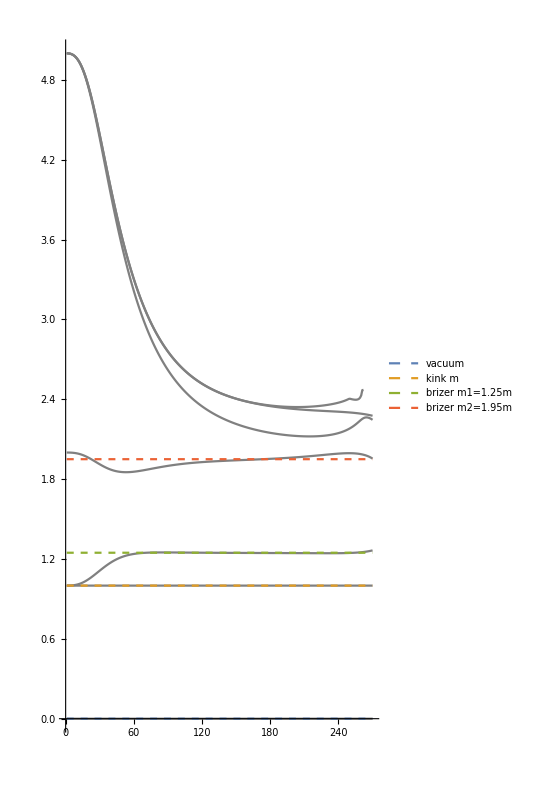

```mathematica
Show[ListLinePlot[Transpose[EnergyTableL7P],AspectRatio->2,PlotStyle->Gray],Plot[{0,1,1.247,1.95},{x,1,270},PlotStyle->Dashed,PlotLegends->{"vacuum","kink m","brizer m1=1.25m","brizer m2=1.95m"}]]
```

```mathematica
EnergyTableL9=Table[Sort[1/(i/100)Eigenvalues[H9[-(i/100)^(14/5)-0.]]][[1;;7]]//Chop,{i,1,300}];
```

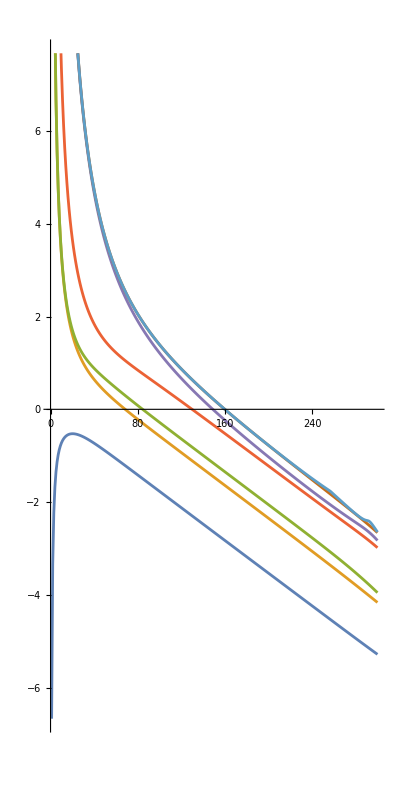

```mathematica
PlotL9=ListLinePlot[Transpose[EnergyTableL9],AspectRatio->2]
```

```mathematica
EnergyTableL9P=Table[(EnergyTableL9[[i]][[1;;7]]-EnergyTableL9[[i]][[1]])/(EnergyTableL9[[i]][[2]]-EnergyTableL9[[i]][[1]])//Chop,{i,1,270}];
```

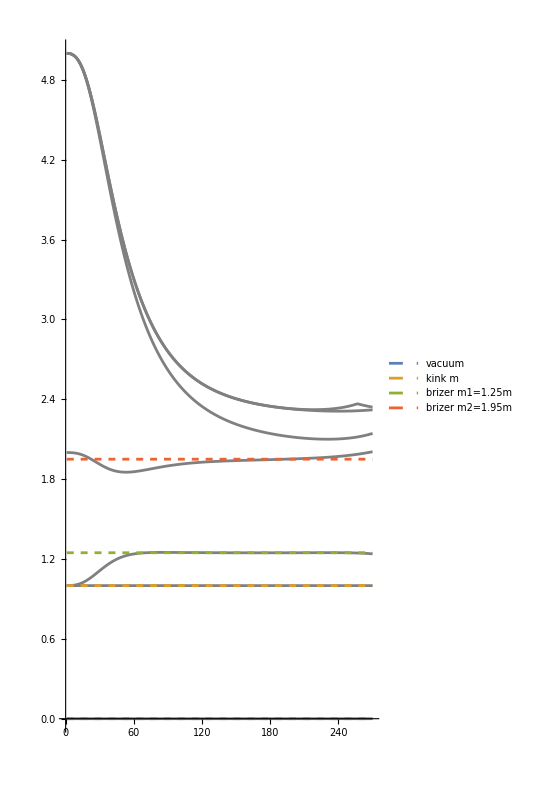

```mathematica
Show[ListLinePlot[Transpose[EnergyTableL9P],AspectRatio->2,PlotStyle->Gray],Plot[{0,1,1.247,1.95},{x,1,270},PlotStyle->Dashed,PlotLegends->{"vacuum","kink m","brizer m1=1.25m","brizer m2=1.95m"}]]
```

```mathematica
EnergyTableL11=Table[Sort[(1/i/100)Eigenvalues[H11[-(i/100)^(14/5)-0.]]][[1;;7]]//Chop,{i,1,350}];
```

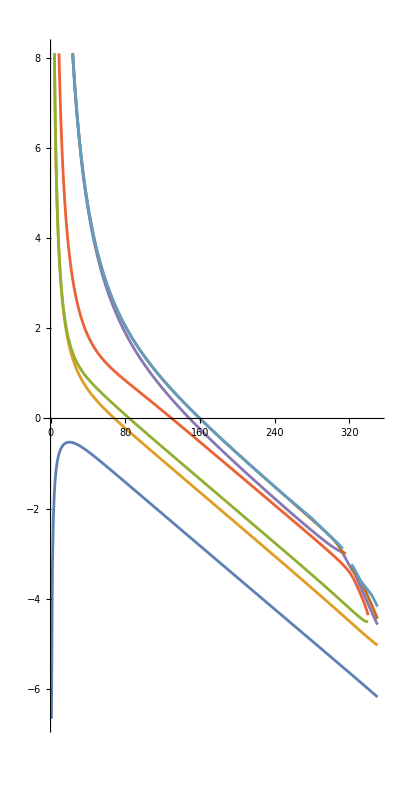

```mathematica
PlotL11=ListLinePlot[Transpose[EnergyTableL11],AspectRatio->2]
```

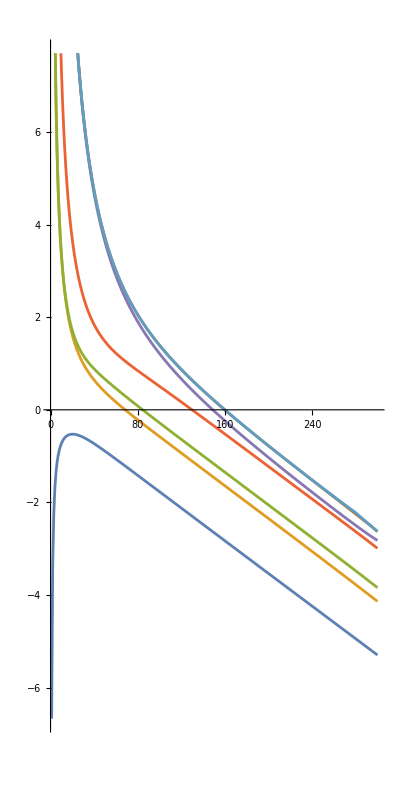

```mathematica
EnergyTableL11P=Table[(EnergyTableL11[[i]][[1;;7]]-EnergyTableL11[[i]][[1]])/(EnergyTableL11[[i]][[2]]-EnergyTableL11[[i]][[1]])//Chop,{i,1,300}];
```

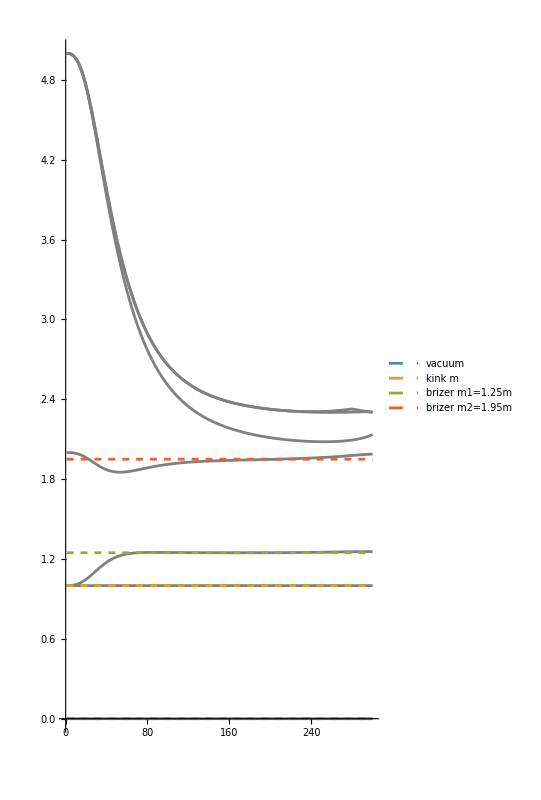

```mathematica
Show[ListLinePlot[Transpose[EnergyTableL11P],AspectRatio->2,PlotStyle->Gray],Plot[{0,1,1.247,1.95},{x,1,300},PlotStyle->Dashed,PlotLegends->{"vacuum","kink m","brizer m1=1.25m","brizer m2=1.95m"}]]
```

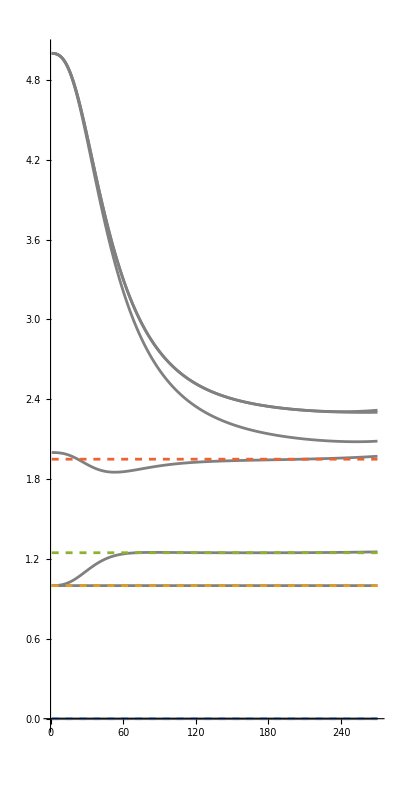

```mathematica
H[12,x]
```

```mathematica
EnergyTableL12=Table[Sort[1/(i/100)Eigenvalues[H12[-(i/100)^(14/5)-0.]]][[1;;7]]//Chop,{i,1,350}];
```

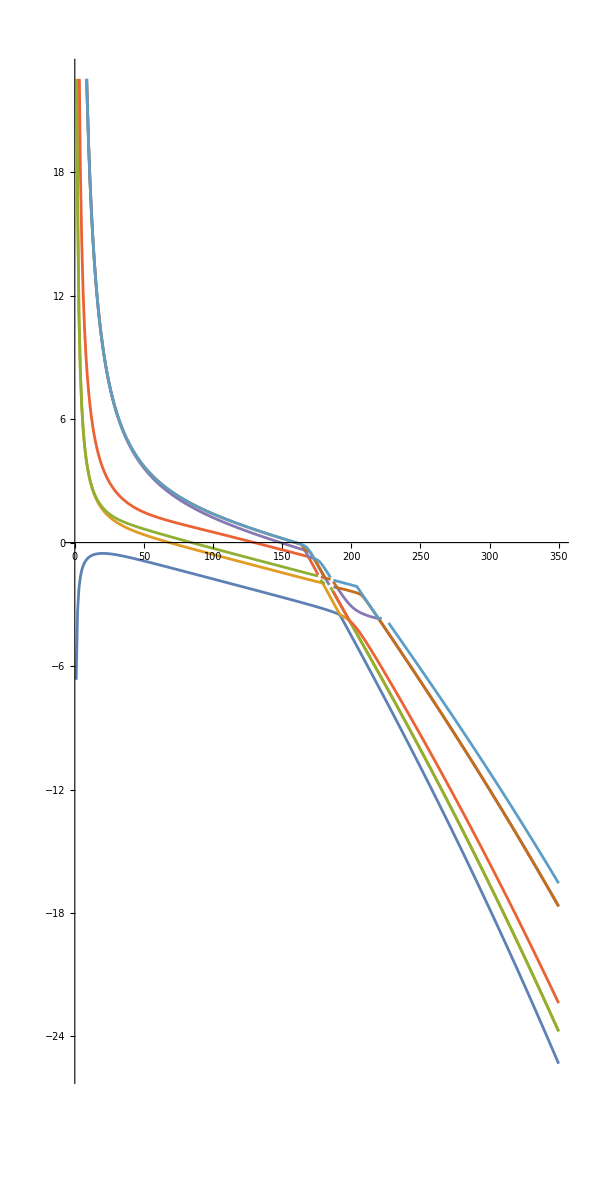

```mathematica
PlotL12=ListLinePlot[Transpose[EnergyTableL12],AspectRatio->2]
```

```mathematica
EnergyTableL12P=Table[(EnergyTableL12[[i]][[1;;7]]-EnergyTableL12[[i]][[1]])/(EnergyTableL12[[i]][[2]]-EnergyTableL12[[i]][[1]])//Chop,{i,1,270}];
```

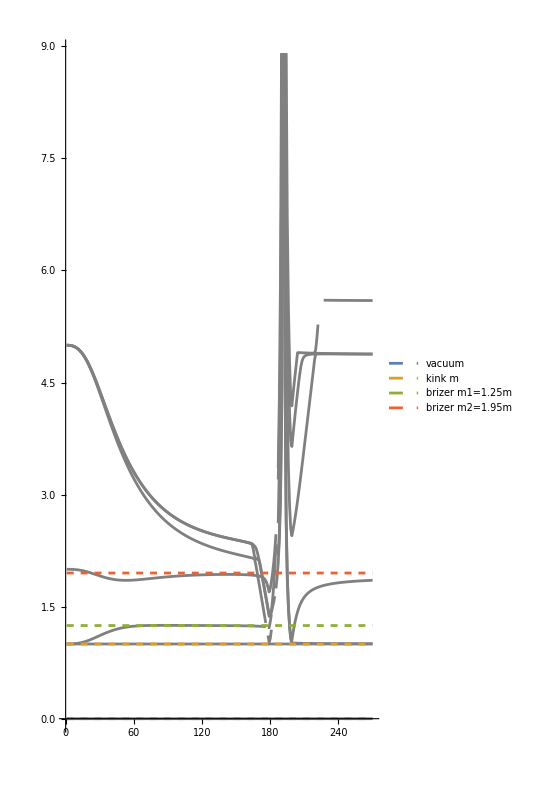

```mathematica
Show[ListLinePlot[Transpose[EnergyTableL12P],AspectRatio->2,PlotStyle->Gray],Plot[{0,1,1.247,1.95},{x,1,270},PlotStyle->Dashed,PlotLegends->{"vacuum","kink m","brizer m1=1.25m","brizer m2=1.95m"}]]
```

```mathematica
H[13,x]
```

```mathematica
EnergyTableL13=Table[Sort[1/(i/100)Eigenvalues[H13[-(i/100)^(14/5)-0.]]][[1;;7]]//Chop,{i,1,300}];
```

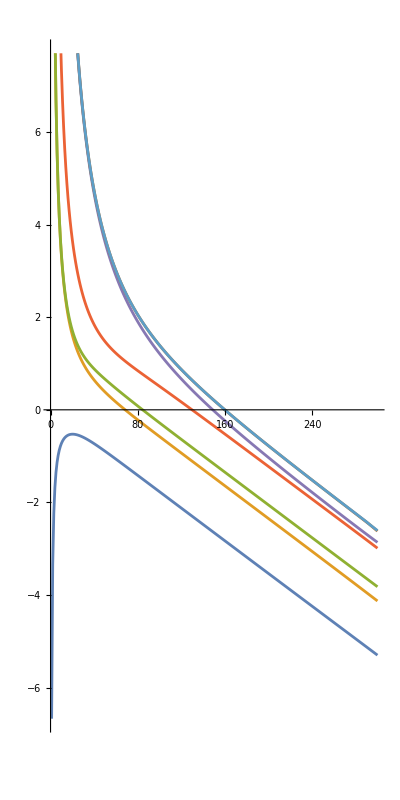

```mathematica
PlotL13=ListLinePlot[Transpose[EnergyTableL13],AspectRatio->2]
```

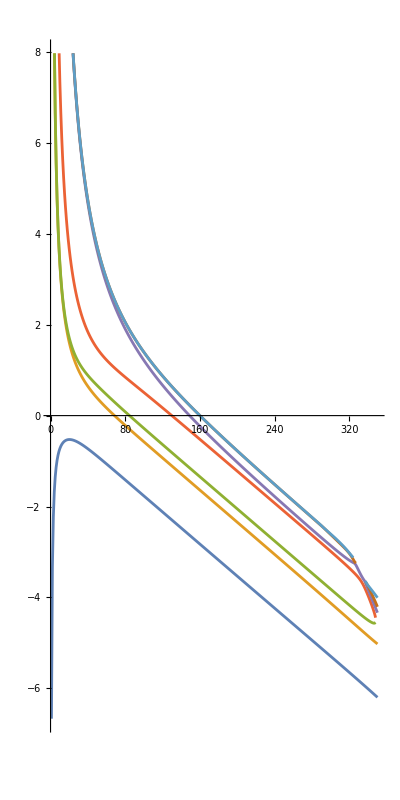

```mathematica
EnergyTableL13P=Table[(EnergyTableL13[[i]][[1;;7]]-EnergyTableL13[[i]][[1]])/(EnergyTableL13[[i]][[2]]-EnergyTableL13[[i]][[1]])//Chop,{i,1,320}];
```

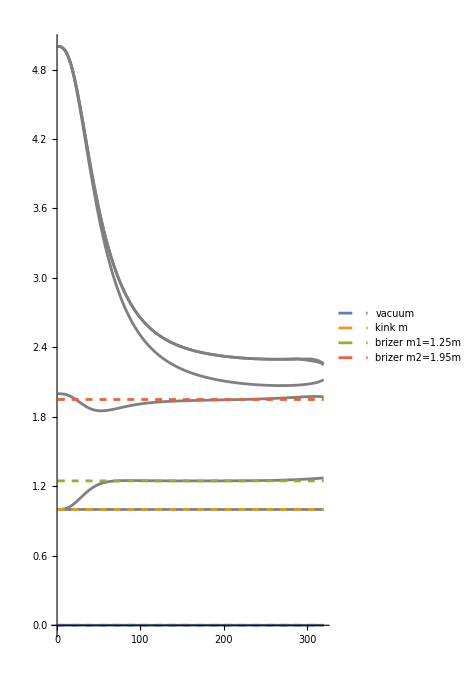

```mathematica
Show[ListLinePlot[Transpose[EnergyTableL13P],AspectRatio->2,PlotStyle->Gray],Plot[{0,1,1.247,1.95},{x,1,320},PlotStyle->Dashed,PlotLegends->{"vacuum","kink m","brizer m1=1.25m","brizer m2=1.95m"}]]
```

```mathematica
Length[Basis[13]]
```

839